```mathematica
$PlotTheme = "Classic"
```

Classic

## Setup

```mathematica
ScrollingOptions->{"VerticalScrollRange"->FitAll}
```

ScrollingOptions→{VerticalScrollRange→FitAll}

```mathematica
x1 = 0;
x2 = 1;
Clear[m,b]
m = 2/(x2 - x1)
Solve[m x1 + b == -1,b];
b = b/.%[[1]]
Num =240;(* 240 for gaussianR, 60 for linear*)
T[n_,u_]:=ChebyshevT[n,m u + b]
dT[n_,u_]:=m*Derivative[0,1][ChebyshevT][n,m u+b]
d2T[n_,u_]:=m^2* Derivative[0,2][ChebyshevT][n,m u+b]
c[j_]:= Piecewise[{{2,Abs[j]==Num},{2,j==0},{1,Abs[j]<Num}}]
p[j_]:= Piecewise[{{2,j==0},{2,j==Num},{1,0<j<Num}}]
Gridlist = ConstantArray[0,{Num+1}];
Gridlist =N [1/m(Cos[π#/Num]-b)&/@Range[0,Num],15]
Card[j_,u_]:= If[u==Gridlist[[j+1]],1,(-1)^(j+1)(1-(m u + b)^2)/(c[j] Num^2((m u+b)-(m Gridlist[[j+1]]+b)))1/m dT[Num,u]]
dCardM  =
 ConstantArray[0,{Num+1,Num+1}];
Module[
{i,j},
For[i=1,i≤Num+1,i++,For[j=1,j≤Num+1 ,j++,dCardM[[i,j]]=(-1)^(i+j)(m)p[i-1]/(p[j-1](m Gridlist[[i]]-m Gridlist[[j]]))]];
For[i=2,i≤Num,i++, dCardM[[i,i]]=-(m)(m*Gridlist[[i]]+b)/(2(1-(m*Gridlist[[i]]+b)^2))];
]
dCardM[[1,1]] =(m) (1+2 Num^2)/6;
dCardM[[Num+1,Num+1]] = -dCardM[[1,1]];
d2CardM = dCardM.dCardM;
```

2

-1

{1.,0.999957163787004,0.999828662487779,0.999614518120361,0.999314767377287,0.998929461619302,0.998458666866564,0.997902463787331,0.997260947684137,0.996534228477463,0.995722430686905,0.994825693409835,0.993844170297569,0.992778029529039,0.991627453781977,0.990392640201615,0.989073800366903,0.987671160254256,0.986184960198838,0.984615454853377,0.982962913144534,0.981227618226824,0.979409867434097,0.977509972228593,0.975528258147577,0.973465064747553,0.971320745546089,0.969095667961242,0.966790213248601,0.964404776435962,0.961939766255643,0.959395605074449,0.9567727288213,0.954071586912541,0.95129264217493,0.948436370766344,0.945503262094184,0.942493818731521,0.939408556330983,0.936248003536399,0.933012701892219,0.929703205750726,0.926320082177046,0.922863910851987,0.919335283972712,0.915734806151273,0.912063094311008,0.908320777580839,0.904508497187474,0.90062690634553,0.896676670145618,0.892658465440372,0.888572980728485,0.88442091603673,0.880202982800015,0.875919903739489,0.871572412738697,0.867161254717843,0.862687185506144,0.858150971712327,0.853553390593274,0.84889522992084,0.844177287846877,0.839400372766471,0.834565303179429,0.829672907550034,0.824724024165092,0.819719500990292,0.814660195524919,0.809546974654917,0.80438071450436,0.79916230028533,0.793892626146237,0.788572595018617,0.783203118462416,0.777785116509801,0.772319517507514,0.766807257957806,0.761249282357974,0.755646543038526,0.75,0.744310620748477,0.738579380129804,0.732807260162556,0.726995249869773,0.721144345109501,0.715255548404148,0.709329868768714,0.7033683215379,0.697371928192134,0.691341716182545,0.685278718754918,0.67918397477265,0.673058528538746,0.666903429616885,0.660719732651581,0.654508497187474,0.648270787487785,0.642007672351961,0.635720224932537,0.62940952255126,0.623076646514497,0.616722681927953,0.610348717510751,0.60395584540888,0.597545161008064,0.591117762746074,0.584674751924512,0.578217232520115,0.57174631099559,0.565263096110026,0.558768698728919,0.552264231633827,0.545750809331701,0.539229547863922,0.532701564615072,0.526167978121472,0.519629907879534,0.513088474153937,0.506544797785672,0.5,0.493455202214328,0.486911525846063,0.480370092120466,0.473832021878528,0.467298435384928,0.460770452136078,0.454249190668299,0.447735768366173,0.441231301271081,0.434736903889974,0.42825368900441,0.421782767479885,0.415325248075488,0.408882237253926,0.402454838991936,0.39604415459112,0.389651282489249,0.383277318072047,0.376923353485503,0.37059047744874,0.364279775067463,0.357992327648039,0.351729212512215,0.345491502812526,0.339280267348419,0.333096570383115,0.326941471461254,0.32081602522735,0.314721281245082,0.308658283817455,0.302628071807866,0.2966316784621,0.290670131231286,0.284744451595852,0.278855654890499,0.273004750130227,0.267192739837444,0.261420619870196,0.255689379251523,0.25,0.244353456961474,0.238750717642026,0.233192742042194,0.227680482492486,0.222214883490199,0.216796881537584,0.211427404981383,0.206107373853763,0.20083769971467,0.19561928549564,0.190453025345083,0.185339804475081,0.180280499009708,0.175275975834908,0.170327092449966,0.165434696820571,0.160599627233529,0.155822712153123,0.15110477007916,0.146446609406726,0.141849028287673,0.137312814493856,0.132838745282157,0.128427587261303,0.124080096260511,0.119797017199985,0.11557908396327,0.111427019271515,0.107341534559628,0.103323329854382,0.0993730936544697,0.0954915028125263,0.0916792224191605,0.0879369056889922,0.0842651938487274,0.080664716027288,0.0771360891480134,0.0736799178229539,0.0702967942492737,0.0669872981077807,0.0637519964636014,0.0605914436690173,0.0575061812684791,0.0544967379058161,0.0515636292336558,0.0487073578250697,0.0459284130874594,0.0432272711786996,0.0406043949255509,0.0380602337443566,0.0355952235640379,0.0332097867513991,0.0309043320387579,0.0286792544539108,0.0265349352524472,0.0244717418524232,0.0224900277714067,0.0205901325659035,0.0187723817731764,0.0170370868554659,0.0153845451466228,0.0138150398011617,0.0123288397457437,0.0109261996330972,0.00960735979838478,0.00837254621802271,0.00722197047096114,0.00615582970243114,0.00517430659016489,0.00427756931309479,0.00346577152253685,0.00273905231586333,0.00209753621266914,0.00154133313343601,0.00107053838069825,0.000685232622713063,0.000385481879638533,0.00017133751222136,0.0000428362129964839,0}

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

```mathematica
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/(2 SuperscriptBox[x, 2]) + 1/x*radiallamblist[["<>ToString[i+1]<>"]]+1/2(radiallamblist[["<>ToString[i+1]<>"]])^2+ x*"<>"sigmadotsubscale"<>ToString[i]<>"[x]"]
,{i,0,15}];
```

## RN

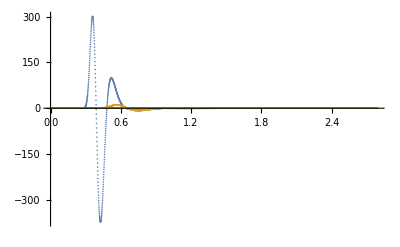

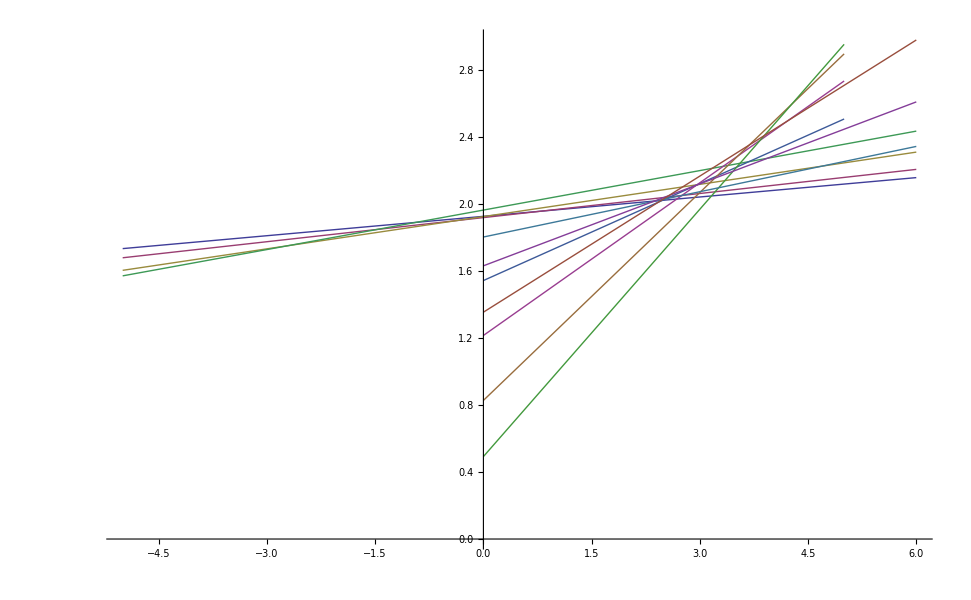

```mathematica
ListPlot[{Cr2pt5wid0pt05list,Cr2wid0pt05list,Cr1pt5wid0pt05list,Cr1pt25wid0pt05list,Cr4wid0pt5list,Cr2wid0pt5list,Cr1wid0pt5list,Cr0pt5wid0pt5list,Cr4wid0pt1list,Cr2wid0pt1list,Cr1wid0pt1list},Joined->True]
```

```mathematica
pressurepos1blistϵ[[387]]
```

{0.359213,300.984}

```mathematica
pressurepos2blistϵ[[609]]
```

{0.565808,11.0388}

```mathematica
pressurepos3blistϵ[[829]]
```

{0.770541,0.884965}

```mathematica
a2=-1
```

-1

```mathematica
NSolve[0.35921347561341044==C (-3/4 a2)^(1/4)1/(4.5),C]
```

{{C→1.737}}

```mathematica
NSolve[0.5658077543340765==C (-3/4 a2)^(1/4)1/(2.5),C]
```

{{C→1.52}}

```mathematica
NSolve[0.7705408233365385==C (-3/4 a2)^(1/4)1/(1.5),C]
```

{{C→1.242}}

```mathematica
1.737/1.52
```

1.14276

```mathematica
1.544/1.216
```

1.26974

```mathematica
1.216/0.8280000000000001
```

1.4686

```mathematica
temp = Table[pressurepos3blistϵ[[i,2]],{i,1,Length[pressurepos3blistϵ]}];
```

```mathematica
Position[pressurepos3blistϵ,Max[temp]]
```

{{829,2}}

1.50658

## GaussianR Bsub, f3 = (0%), fxy = 0.0 tstep = 0.001 N = 240 ** rave = 4, width 0.05

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.0005wid0.05uave0.25a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5"
```

```mathematica
"C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.0005wid0.05uave0.25a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5"
```

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

4.54747×10^-13

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

9.09495×10^-12

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.87537×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

2.72848×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.995×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-0.00326489,-9.06986×10^-6}

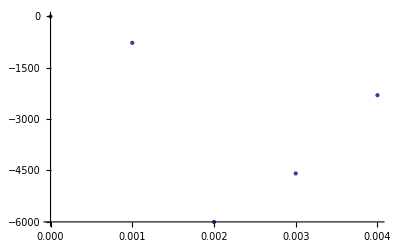

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

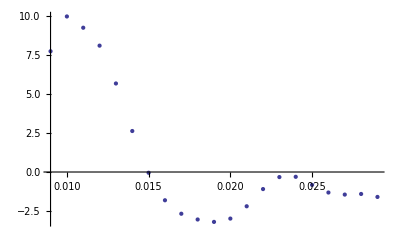

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

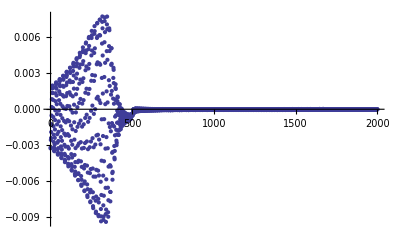

```mathematica
ListPlot[lamblist,PlotRange->All]
```

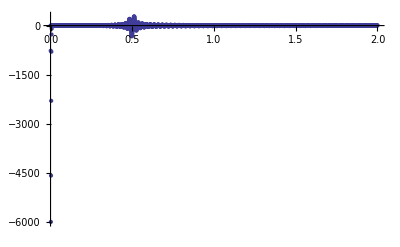

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

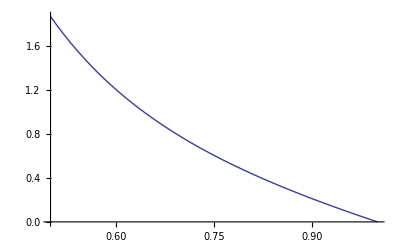

```mathematica
Plot[sigmadot1[x],{x,0.5,1},PlotRange->All]
```

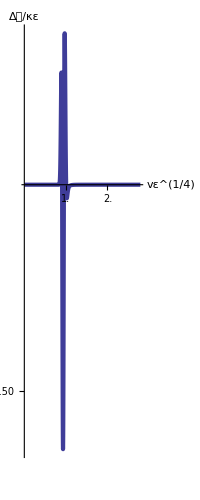

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureC1 = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressureC1ϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
PlotpressureC1ϵ = ListPlot[pressurepos1blistϵ ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{-300,-150,150,300}},ImageSize->{{300},{200}},AspectRatio->Full]
```

```mathematica
Position[pressurepos1blistϵ[[;;1000]],Max[pressurepos1blistϵ[[;;1000]]]]
```

{{961,2}}

```mathematica
pressurepos1blistϵ[[961]]
```

{0.893381,81.7036}

```mathematica
Solve[0.8933806647380156==C (3/4(-a2))^(1/4)/2.0,C]
```

{{C→1.92}}

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-8.6112×10^-14

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

## GaussianR Bsub, f3 = (0%), fxy = 0.0 tstep = 0.001 N = 240 ** rave = 3, width 0.05 N = 300

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN300amp0.0005wid0.05uave0.333333333333a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5"
```

```mathematica
"C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN300amp0.0005wid0.05uave0.333333333333a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5"
```

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.81899×10^-12

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

2.55795×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.63709×10^-11

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.33363×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.13687×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99945×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-0.000118682,3.86639×10^-10}

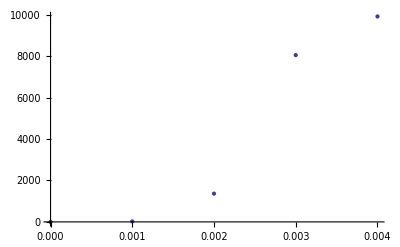

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

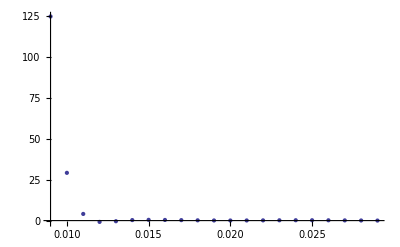

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

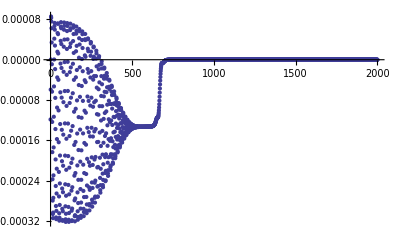

```mathematica
ListPlot[lamblist,PlotRange->All]
```

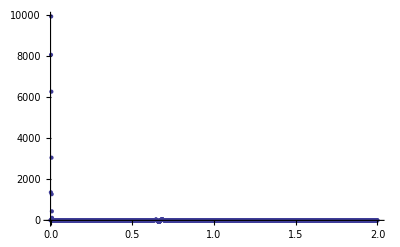

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

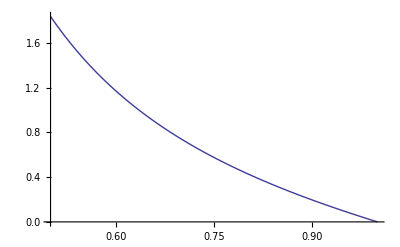

```mathematica
Plot[sigmadot1[x],{x,0.5,1},PlotRange->All]
```

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureC1 = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressureC1ϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
PlotpressureC1ϵ = ListPlot[pressurepos1blistϵ ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{-300,-150,150,300}},ImageSize->{{300},{200}},AspectRatio->Full]
```

-Graphics-

```mathematica
Position[pressurepos1blistϵ[[;;1000]],Max[pressurepos1blistϵ[[;;1000]]]]
```

{{961,2}}

```mathematica
pressurepos1blistϵ[[961]]
```

{0.893381,81.7036}

```mathematica
Solve[0.8933806647380156==C (3/4(-a2))^(1/4)/2.0,C]
```

{{C→1.92}}

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-7.10678×10^-12

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

## GaussianR Bsub, f3 = (0%), fxy = 0.0 tstep = 0.001 N = 240 ** rave = 2, width 0.05

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.05uave0.5a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

```mathematica
"C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.05uave0.5a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

2.13163×10^-14

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

5.68434×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.42685×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

2.72848×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99567×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-0.00123769,2.25423×10^-9}

Here the spike is quite large, and this is for a small fxy.

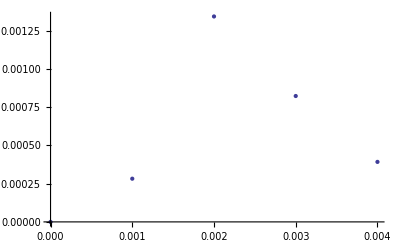

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

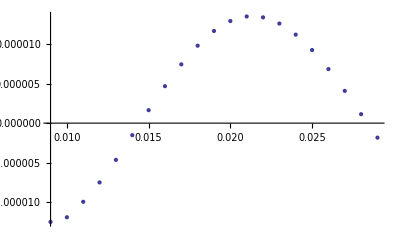

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

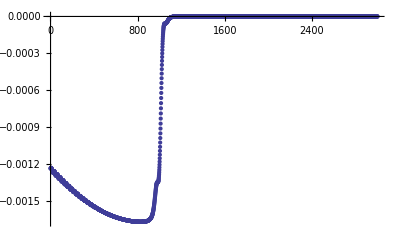

```mathematica
ListPlot[lamblist,PlotRange->All]
```

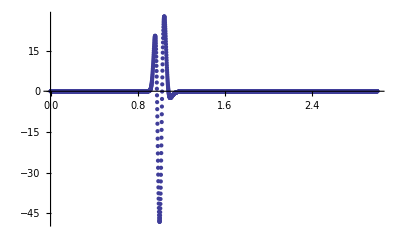

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurepos1blist = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurepos1blistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
pressurepos1blistϵs = Table[{tlist[[i]](3/4(256))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
pressurepos1blistpiTs = Table[{tlist[[i]]4,templist[[i]]},{i,1,Length[tlist]}];
pressurepos1blistgeopiT = Table[{tlist[[i]] √(1*4),templist[[i]]},{i,1,Length[tlist]}];
pressurepos1blistSs = Table[{tlist[[i]](π 4^3)^(1/3) ,templist[[i]]},{i,1,Length[tlist]}];
Plotpressurepos1bϵ = ListPlot[pressurepos1blistϵ ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{-300,-150,150,300}},ImageSize->{{300},{200}},AspectRatio->Full]
```

-Graphics-

```mathematica
Position[pressurepos1blistϵ[[;;1000]],Max[pressurepos1blistϵ[[;;1000]]]]
```

{{961,2}}

```mathematica
pressurepos1blistϵ[[961]]
```

{0.893381,81.7036}

```mathematica
Solve[0.8933806647380156==C (3/4(-a2))^(1/4)/2.0,C]
```

{{C→1.92}}

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-8.6112×10^-14

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

## GaussianR Bsub, f3 = (0%), fxy = 0.0 tstep = 0.001 N = 240 ** rave = 1, width 0.05

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.05uave1.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

```mathematica
"C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.05uave1.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

3.52366×10^-19

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.33227×10^-15

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.05391×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.16296×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.92123×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-7.02316×10^-7,-4.72247×10^-9}

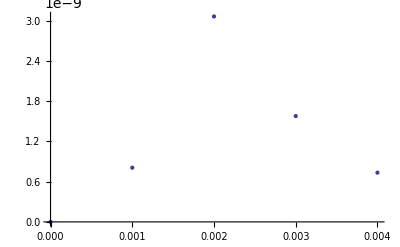

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

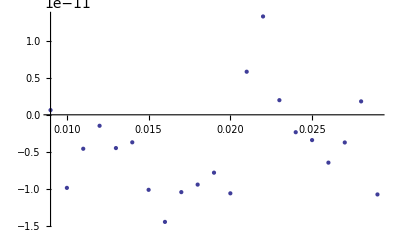

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

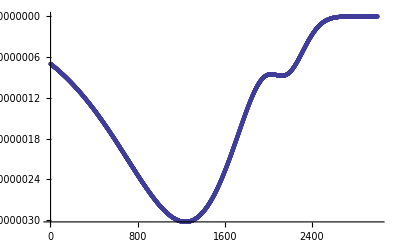

```mathematica
ListPlot[lamblist,PlotRange->All]
```

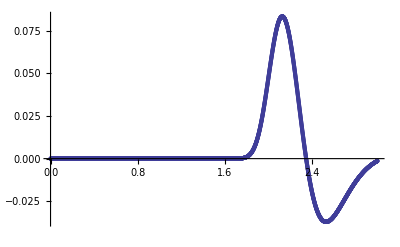

```mathematica
ListPlot[pressureC3list,PlotRange->All]
```

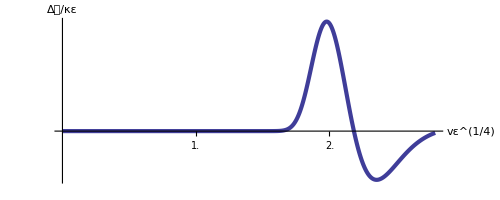

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureC3list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressureC3listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
PlotpressureC3bϵ = ListPlot[pressureC3listϵ ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{-300,-150,150,300}},ImageSize->{{300},{200}},AspectRatio->Full]
```

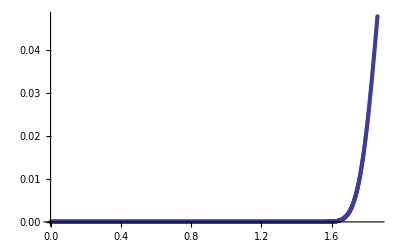

```mathematica
ListPlot[pressureC3listϵ,PlotRange->All]
```

```mathematica
temp = Table[pressureC3list[[i,2]],{i,1,Length[pressureC3list]}];
```

```mathematica
Position[temp,Max[temp]]
```

{{2127}}

```mathematica
pressureC3listϵ[[2127]]
```

{1.97847,0.0834034}

```mathematica
Solve[1.9784659304510634==C (3/4(-a2))^(1/4)/1.0,C]
```

{{C→2.126}}

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.318309

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-4.43617×10^-7

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14158

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.249994

## GaussianR Bsub, f3 = (0%), fxy = 0.0 tstep = 0.001 N = 240 ** rave = 1/2, width 0.05

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN300amp0.0005wid0.05uave2.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN300amp0.0005wid0.05uave2.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3500FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

7.59645×10^-65

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.13687×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

2.05712×10^-38

```mathematica
Max[Abs[ABCcheckDlist]]
```

3.39062×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.36875×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

3.65497×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{5.38314×10^-10,5.38305×10^-10}

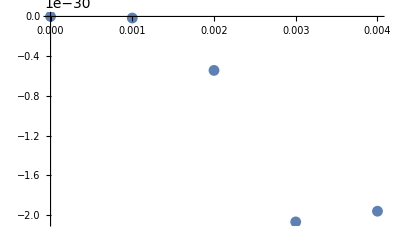

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

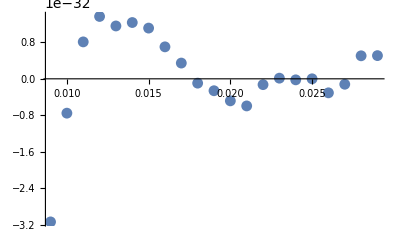

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

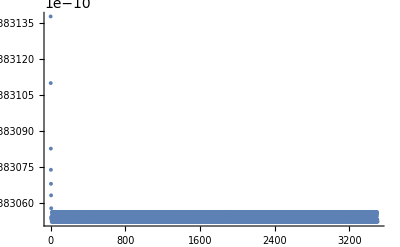

```mathematica
ListPlot[lamblist,PlotRange->All]
```

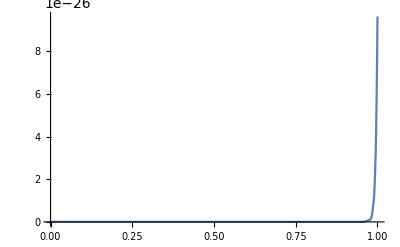

```mathematica
Plot[Bsub1[x],{x,0,1},PlotRange->All]
```

```mathematica
ListPlot[pressureC3list,PlotRange->All]
```

ListPlot::lpn: pressureC3list is not a list of numbers or pairs of numbers.

ListPlot[pressureC3list,PlotRange→All]

```mathematica
g=1
```

1

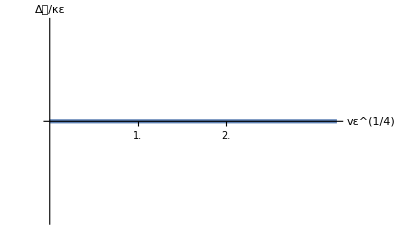

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureC4list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressureC4listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
PlotpressureC4bϵ = ListPlot[pressureC4listϵ ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{-300,-150,150,300}},ImageSize->{{300},{200}},AspectRatio->Full]
```

```mathematica
ListPlot[pressureC3listϵ,PlotRange->All]
```

-Graphics-

```mathematica
temp = Table[pressureC3list[[i,2]],{i,1,Length[pressureC3list]}];
```

```mathematica
Position[temp,Max[temp]]
```

{{2127}}

```mathematica
pressureC3listϵ[[2127]]
```

{1.97847,0.0834034}

```mathematica
Solve[1.9784659304510634==C (3/4(-a2))^(1/4)/1.0,C]
```

{{C→2.126}}

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.318309

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-4.43617×10^-7

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14158

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.249994

## GaussianR Bsub, f3 = (80%), fxy = 0.0 tstep = 0.001 N = 240 ** rave = 1 width = 0.005

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.9wid0.005uave1.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS5000FF.h5"
```

```mathematica
"C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.9wid0.005uave1.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS5000FF.h5"
```

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

$Aborted

$Aborted

$Aborted

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.15463×10^-14

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

2.41585×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

8.14768×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

9.09495×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99956×10^-12

### Plots

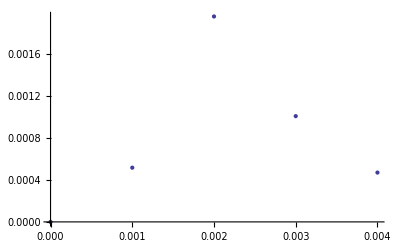

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

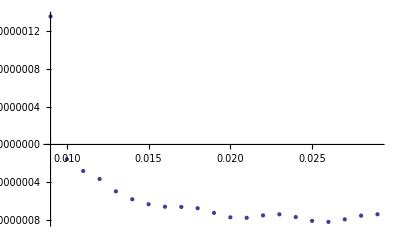

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

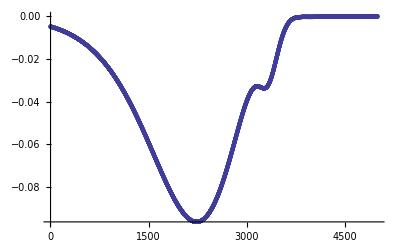

```mathematica
ListPlot[lamblist,PlotRange->All]
```

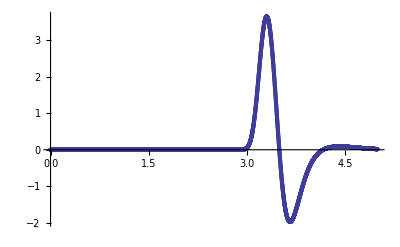

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

```mathematica
ultrafinegrid = Table[i*1/100000,{i,0,100000}];
```

```mathematica
temptemplist = Bsub1[ultrafinegrid];
```

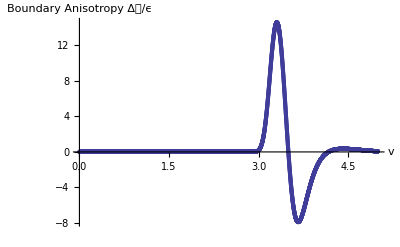

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureDeepSharp4RN80list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressureDeepSharp4RN80listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Boundary Anisotropy Δ𝒫/ϵ",25]}]
```

```mathematica
finegrid = Range[0,1,0.01];
```

```mathematica
Position[pressureDeepSharp4RN80listϵ,Max[pressureDeepSharp4RN80listϵ]]
```

{{3307,2}}

```mathematica
pressureDeepSharp4RN80listϵ[[3307]]
```

{3.07658,14.5764}

```mathematica
NSolve[3.076579664191541==C (-3/4 a2)^(1/4)1/(1/1),C]
```

{{C→3.306}}

```mathematica
reportfuncttlist
```

{0.,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.,1.05,1.1,1.15,1.2,1.25,1.3,1.35,1.4,1.45,1.5,1.55,1.6,1.65,1.7,1.75,1.8,1.85,1.9,1.95,2.,2.05,2.1,2.15,2.2,2.25,2.3,2.35,2.4,2.45,2.5,2.55,2.6,2.65,2.7,2.75,2.8,2.85,2.9,2.95,3.,3.05,3.1,3.15,3.2,3.25,3.3,3.35,3.4,3.45,3.5,3.55,3.6,3.65,3.7,3.75,3.8,3.85,3.9,3.95,4.,4.05,4.1,4.15,4.2,4.25,4.3,4.35,4.4,4.45,4.5,4.55,4.6,4.65,4.7,4.75,4.8,4.85,4.9,4.95}

```mathematica
Bsubevolve= Flatten[Table[{reportfuncttlist[[i]](3/4(-a2))^(1/4),finegrid[[j]],ToExpression["Bsub"<>ToString[i]<>"[finegrid[[j]]]"]},{i,1,Length[reportfuncttlist]},{j,1,Length[finegrid]}],1];
```

$Aborted

```mathematica
ListPlot3D[Bsubevolve, 
AxesLabel->{"vε^(1/4)",Style["u",28,Italic, FontFamily->"Times",Black], Style["B_s",28,Italic, FontFamily->"Times",Black]}, AxesStyle->Directive[22,Black],PlotRange->All,ColorFunction->Function[{x,y,z},Hue[1.1z+0.1]],ImageSize->{{400},{300}},AspectRatio->Full]
```

-Graphics3D-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-4.66899×10^-7

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14158

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.249997

## Finding C’s ε dependence

```mathematica
ListPlot[{pressurepos2listϵ,pressurepos2a22listϵ,pressurepos2a24listϵ,pressurepos2a28listϵ},PlotRange->All,AxesStyle->Large,AxesLabel-> {"v ε^(1/4)","Anis. r_ave= 2, A = 0.005"},PlotLegends->Placed[SwatchLegend[{Style["ε = 0.75, C = 1.82",20],Style["ε = 1.50, C = 1.83",20],Style["ε = 3.00, C = 1.86 ",20],Style["ε = 6.00, C = 1.94",20]}],{Right,Top}]]
```

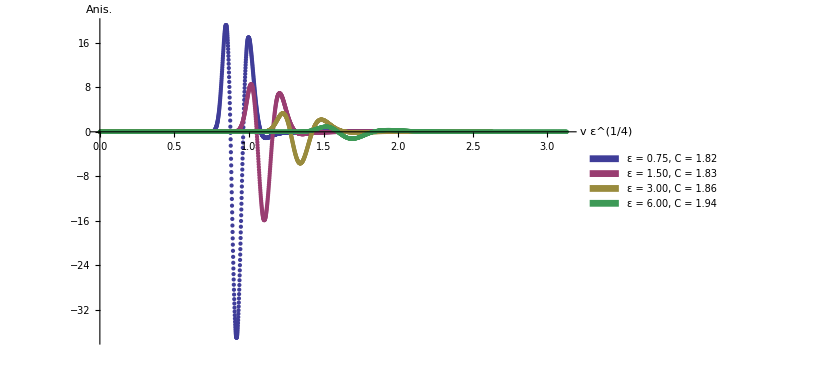

```mathematica
temp = pressurepos2listϵ;
tempy = Table[temp[[i,2]],{i,1,Length[temp]}];
Position[temp,Max[tempy]]
temp[[%[[1,1]]]]
C1 = Table[NSolve[%[[1]]==C (-3/4(-1))^(1/4)1/(2.0+wid*i/2),C][[1,1,2]],{i,0,10}]
```

{{910,2}}

{0.84592,19.1784}

{1.818,1.84073,1.86345,1.88618,1.9089,1.93163,1.95435,1.97708,1.9998,2.02253,2.04525}

```mathematica
temp = pressurepos2a22listϵ;
tempy = Table[temp[[i,2]],{i,1,Length[temp]}];
Position[temp,Max[tempy]]
temp[[%[[1,1]]]]
C2 = Table[NSolve[%[[1]]==C (-3/4(-2))^(1/4)1/(2.0+wid*i/2),C][[1,1,2]],{i,0,10}]
```

{{917,2}}

{1.01372,8.53062}

{1.832,1.8549,1.8778,1.9007,1.9236,1.9465,1.9694,1.9923,2.0152,2.0381,2.061}

```mathematica
temp = pressurepos2a24listϵ;
tempy = Table[temp[[i,2]],{i,1,Length[temp]}];
Position[temp,Max[tempy]]
temp[[%[[1,1]]]]
C3=Table[NSolve[%[[1]]==C (-3/4(-4))^(1/4)1/(2.0+wid*i/2),C][[1,1,2]],{i,0,10}]
```

{{933,2}}

{1.22658,3.31961}

{1.864,1.8873,1.9106,1.9339,1.9572,1.9805,2.0038,2.0271,2.0504,2.0737,2.097}

```mathematica
temp = pressurepos2a28listϵ;
tempy = Table[temp[[i,2]],{i,1,Length[temp]}];
Position[temp,Max[tempy]]
temp[[%[[1,1]]]]
C4 = Table[NSolve[%[[1]]==C (-3/4(-8))^(1/4)1/(2.0+wid*i/2),C][[1,1,2]],{i,0,10}]
```

{{970,2}}

{1.51657,0.925435}

{1.938,1.96222,1.98645,2.01068,2.0349,2.05913,2.08335,2.10757,2.1318,2.15602,2.18025}

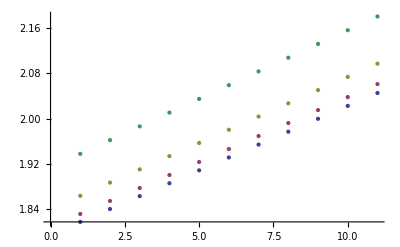

```mathematica
ListPlot[{C1,C2,C3,C4}]
```

```mathematica
temp = pressurepos2a24RN80listϵ;
tempy = Table[temp[[i,2]],{i,1,Length[temp]}];
Position[temp,Max[tempy]]
temp[[%[[1,1]]]]
C7 = Table[NSolve[%[[1]]==C (-3/4(-4))^(1/4)1/(2.0+wid*i/2),C][[1,1,2]],{i,0,10}]
```

{{931,2}}

{1.22395,3.50647}

{1.86,1.88325,1.9065,1.92975,1.953,1.97625,1.9995,2.02275,2.046,2.06925,2.0925}

## GaussianR Bsub, f3 = (0%), fxy = 0.0 tstep = 0.001 N = 240 ** rave = 2

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.1uave0.5a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5"
```

```mathematica
"C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.1uave0.5a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5"
```

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

2.22045×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.84741×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

5.89613×10^-11

```mathematica
Max[Abs[ABCcheckNlist]]
```

5.68434×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.92351×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-0.000641935,1.94555×10^-9}

Here the spike is quite large, and this is for a small fxy.

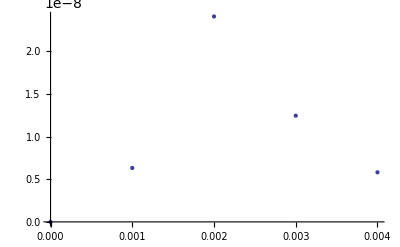

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

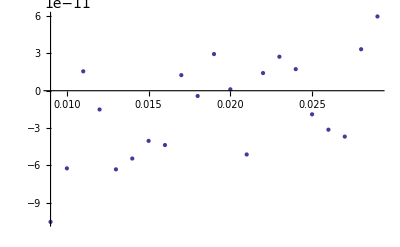

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

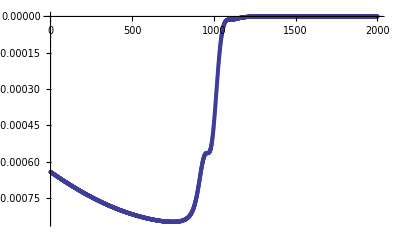

```mathematica
ListPlot[lamblist,PlotRange->All]
```

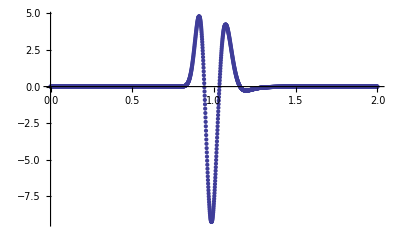

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

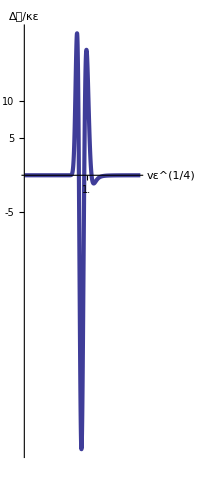

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurepos2list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurepos2listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
Plotpressurepos2ϵ = ListPlot[pressurepos2listϵ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{-5,5,10}},ImageSize->{{300},{200}},AspectRatio->Full]
```

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-4.54598×10^-11

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

## GaussianR Bsub, f3 = (0%), fxy = 0.0 tstep = 0.001 N = 240 ** rave = 2 a2 = 2

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.1uave0.5a2-2.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5"
```

```mathematica
"C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.1uave0.5a2-2.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5"
```

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

2.22045×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

2.84217×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

3.09344×10^-11

```mathematica
Max[Abs[ABCcheckNlist]]
```

2.84217×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.97946×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{0.188907,0.189207}

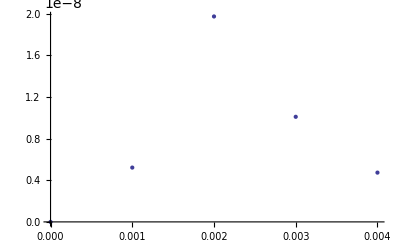

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

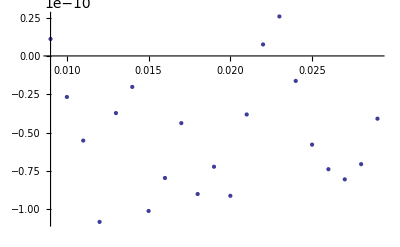

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

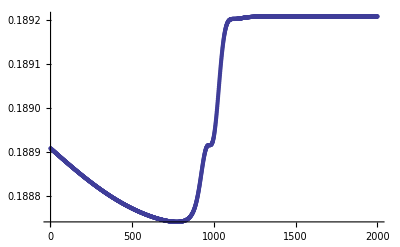

```mathematica
ListPlot[lamblist,PlotRange->All]
```

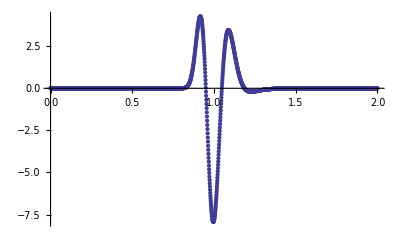

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

```mathematica
g=1
```

1

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurepos2a22list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurepos2a22listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
Plotpressurepos2a22ϵ = ListPlot[pressurepos2blistϵ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{-5,5,10}},ImageSize->{{300},{200}},AspectRatio->Full]
```

ListPlot::lpn: pressurepos2blistϵ is not a list of numbers or pairs of numbers.

ListPlot[pressurepos2blistϵ,PlotRange→All,AxesLabel→{vε^(1/4),Δ𝒫/κε},Joined→True,PlotStyle→{AbsoluteThickness[3]},AxesStyle→Directive[26,GrayLevel[0]],Ticks→{{1.,2.},{-5,5,10}},ImageSize→{{300},{200}},AspectRatio→Full]

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.378536

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

1.5

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-4.74293×10^-11

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

5.28351

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.5

## GaussianR Bsub, f3 = (0%), fxy = 0.0 tstep = 0.001 N = 240 ** rave = 2 a2 = 4

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.1uave0.5a2-4.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5"
```

```mathematica
"C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.1uave0.5a2-4.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5"
```

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

8.88178×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

4.54747×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.18092×10^-11

```mathematica
Max[Abs[ABCcheckNlist]]
```

3.08198×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.88432×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{0.414098,0.414214}

Here the spike is quite large, and this is for a small fxy.

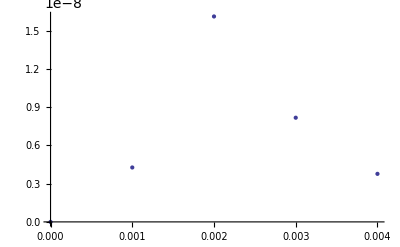

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

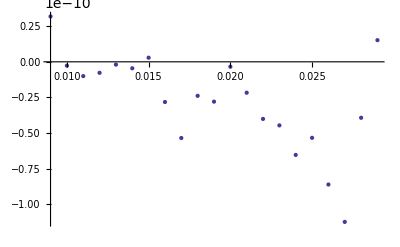

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

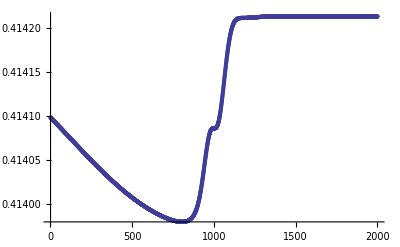

```mathematica
ListPlot[lamblist,PlotRange->All]
```

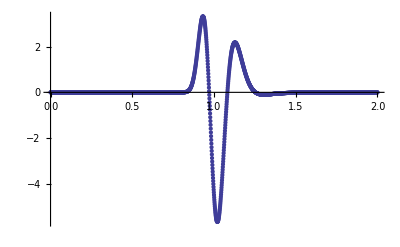

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

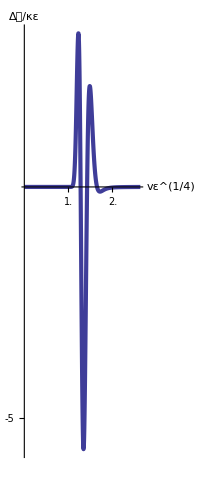

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurepos2a24list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurepos2a24listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
Plotpressurepos2a24bϵ = ListPlot[pressurepos2a24listϵ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{-5,5,10}},ImageSize->{{300},{200}},AspectRatio->Full]
```

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.450158

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3.

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-9.90931×10^-11

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

8.88577

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-1.

## GaussianR Bsub, f3 = (0%), fxy = 0.0 tstep = 0.001 N = 240 ** rave = 2 a2 = 8

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.1uave0.5a2-8.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5"
```

```mathematica
"C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.1uave0.5a2-8.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5"
```

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

3.33067×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

7.95808×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

8.52651×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

4.21307×10^-12

```mathematica
Max[Abs[ABCcheckNlist]]
```

4.37872×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.91118×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{0.681765,0.681793}

Here the spike is quite large, and this is for a small fxy.

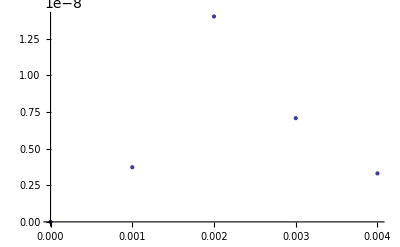

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

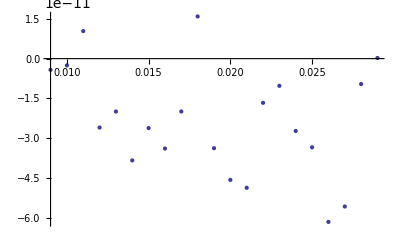

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

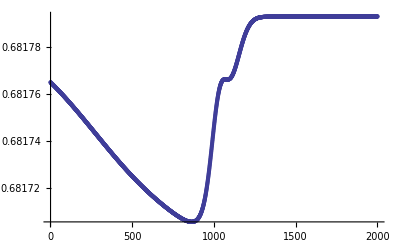

```mathematica
ListPlot[lamblist,PlotRange->All]
```

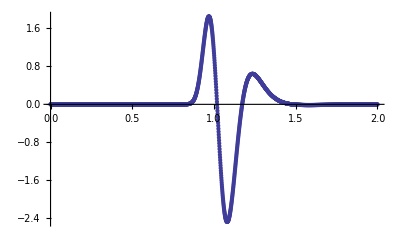

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

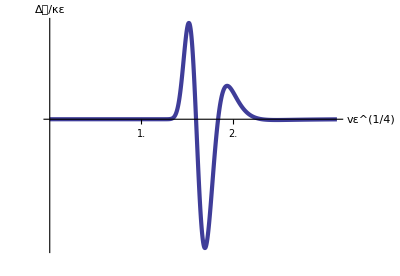

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurepos2a28list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurepos2a28listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
Plotpressurepos2a28bϵ = ListPlot[pressurepos2a28listϵ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{-5,5,10}},ImageSize->{{300},{200}},AspectRatio->Full]
```

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.535331

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

6.

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-1.29145×10^-10

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

14.944

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-2.

## GaussianR Bsub, f3 = (80%), fxy = 0.0 tstep = 0.001 N = 240 ** rave = 2

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.1uave0.5a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5"
```

```mathematica
"C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.1uave0.5a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5"
```

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

2.66454×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.42109×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.84741×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.03607×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

9.09495×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.98146×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-0.0841994,-0.083017}

Here the spike is quite large, and this is for a small fxy.

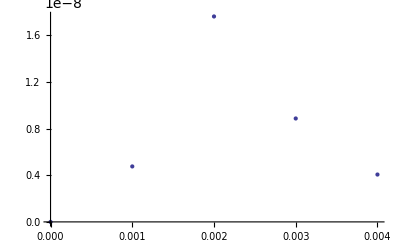

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

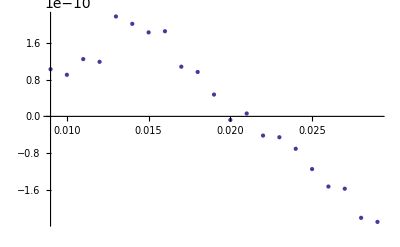

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

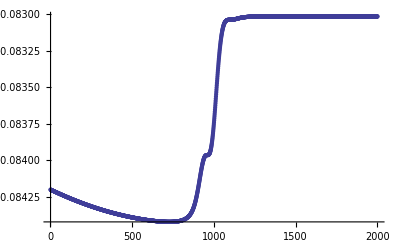

```mathematica
ListPlot[lamblist,PlotRange->All]
```

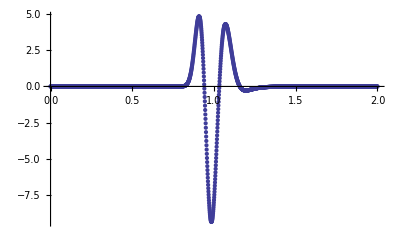

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

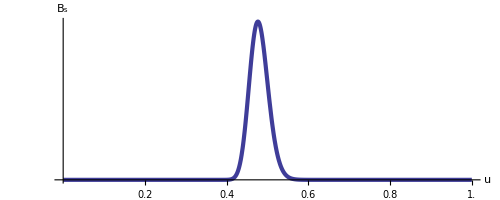

```mathematica
PlotBsubpos2b=Plot[Bsub1[x],{x,0,1},PlotRange->All,AxesLabel->{Style["u",26,Black],Style["B_s",26,Black]},AxesStyle->Directive[26,Black],PlotStyle->{AbsoluteThickness[3]},Ticks->{{0.2,0.4,0.6,0.8,1.0},{0.05,0.10,0.15,0.20}},ImageSize->{{300},{200}},AspectRatio->Full]
```

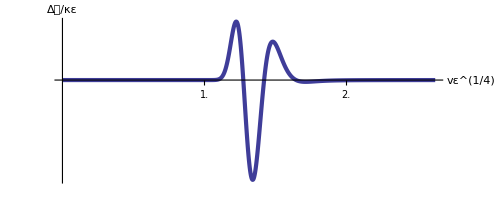

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurepos2RN80list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurepos2RN80listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
Plotpressurepos2RN80ϵ = ListPlot[pressurepos2blistϵ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{-5,5,10}},ImageSize->{{300},{200}},AspectRatio->Full]
```

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.231415

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.511178

```mathematica
chem/T
```

-2.20893

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-1.6901×10^-11

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

2.42233

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.189437

## GaussianR Bsub, f3 = (80%), fxy = 0.0 tstep = 0.001 N = 240 ** rave = 2 a2 = 2

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.1uave0.5a2-2.0f31.44576320578fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5"
```

```mathematica
"C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.1uave0.5a2-2.0f31.44576320578fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5"
```

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

2.22045×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

2.84217×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

4.85012×10^-11

```mathematica
Max[Abs[ABCcheckNlist]]
```

5.68434×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.97413×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{0.0898886,0.0904827}

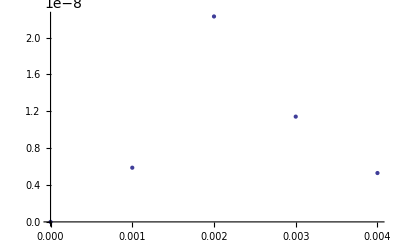

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

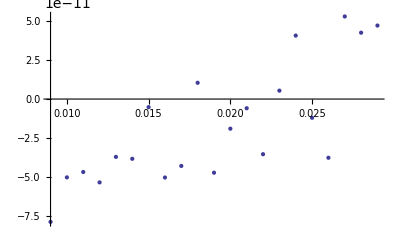

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

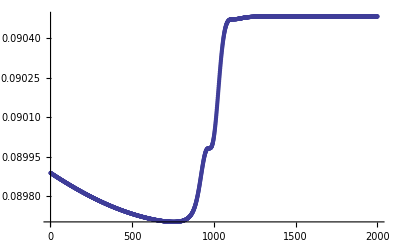

```mathematica
ListPlot[lamblist,PlotRange->All]
```

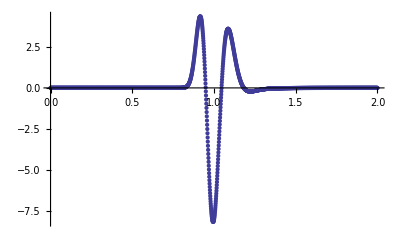

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

```mathematica
g=1
```

1

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurepos2a22RN80list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurepos2a22RN80listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
Plotpressurepos2a22RN80ϵ = ListPlot[pressurepos2blistϵ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{-5,5,10}},ImageSize->{{300},{200}},AspectRatio->Full]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.2752

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.607896

```mathematica
chem/T
```

-2.20893

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

1.5

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-1.74627×10^-11

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

4.07386

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.378874

## GaussianR Bsub, f3 = (80%), fxy = 0.0 tstep = 0.001 N = 240 ** rave = 2 a2 = 4

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.1uave0.5a2-4.0f32.43147419409fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5"
```

```mathematica
"C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.1uave0.5a2-4.0f32.43147419409fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5"
```

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.33227×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

4.54747×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.42109×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.95228×10^-11

```mathematica
Max[Abs[ABCcheckNlist]]
```

3.32623×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99478×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{0.296547,0.29681}

Here the spike is quite large, and this is for a small fxy.

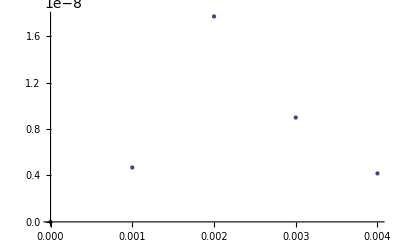

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

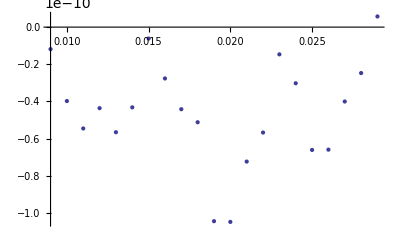

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

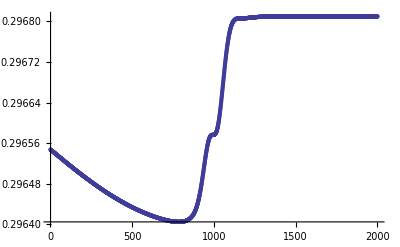

```mathematica
ListPlot[lamblist,PlotRange->All]
```

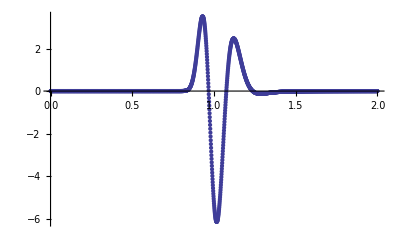

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurepos2a24RN80list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurepos2a24RN80listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
Plotpressurepos2a24RN80bϵ = ListPlot[pressurepos2a24listϵ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{-5,5,10}},ImageSize->{{300},{200}},AspectRatio->Full]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.32727

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.722915

```mathematica
chem/T
```

-2.20893

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3.

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-3.29565×10^-11

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

6.85139

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.757749

## GaussianR Bsub, f3 = (0%), fxy = 0.0 wid = 0.05 N = 240 ** rave = 2

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.05uave0.5a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

```mathematica
"C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.05uave0.5a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

2.13163×10^-14

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

5.68434×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.42685×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

2.72848×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99567×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-0.00123769,2.25423×10^-9}

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

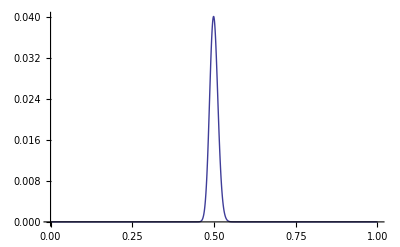

```mathematica
Plot[Bsub1[x],{x,0,1},PlotRange->All]
```

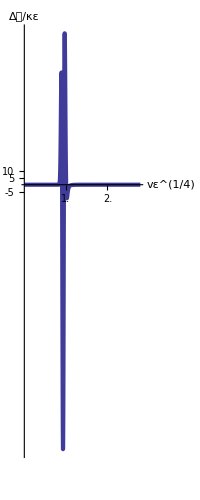

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurer2wid0pt05list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurer2wid0pt05listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
Plotpressurer2wid0pt05ϵ = ListPlot[pressurer2wid0pt05listϵ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{-5,5,10}},ImageSize->{{300},{200}},AspectRatio->Full]
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-8.6112×10^-14

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

## GaussianR Bsub, f3 = (0%), fxy = 0.0 wid = 0.05 N = 240 ** rave = 2 a2 = 8

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.05uave0.5a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

```mathematica
"C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.05uave0.5a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

2.13163×10^-14

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

5.68434×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.42685×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

2.72848×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99567×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-0.00123769,2.25423×10^-9}

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
Plot[Bsub1[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurer2wid0pt05list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurer2wid0pt05listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
Plotpressurer2wid0pt05ϵ = ListPlot[pressurer2wid0pt05listϵ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{-5,5,10}},ImageSize->{{300},{200}},AspectRatio->Full]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-8.6112×10^-14

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

## Finding C’s r_0 dependence (for an appropriate r_0)

```mathematica
sig = 0.5;
rave = 1;
```

```mathematica
Clear[rave]
```

```mathematica
Plot[ⅇ^((-(r-rave)^2)/(2 sig^2)),{r,0,20},PlotRange->All]
```

-Graphics-

```mathematica
Maximize[-x^2,x]
```

{0,{x→0}}

```mathematica
D[D[ⅇ^((-(r-rave)^2)/(2 sig^2)),r],r]
```

(ⅇ^(-(r-rave)^2/(2 sig^2)) (r-rave)^2)/sig^4-(ⅇ^(-(r-rave)^2/(2 sig^2)))/sig^2

```mathematica
Solve[(ⅇ^(-(r-rave)^2/(2 sig^2)) (r-rave)^2)/sig^4-(ⅇ^(-(r-rave)^2/(2 sig^2)))/sig^2==0,r]
```

{{r→rave-sig},{r→rave+sig}}

Width = 0.5

```mathematica
wid = 0.5;
```

## Uncharged Plots

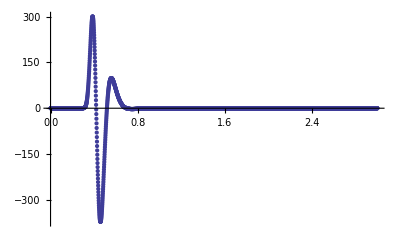
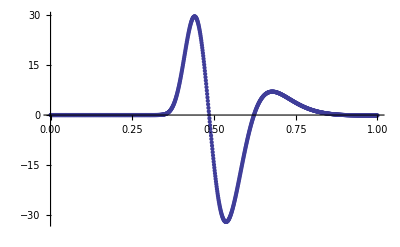
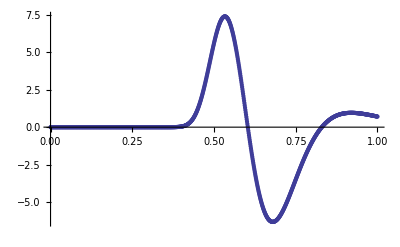
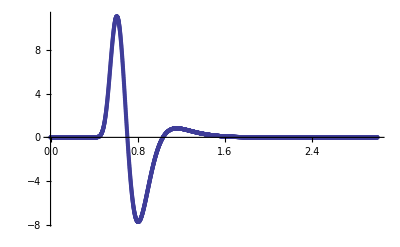
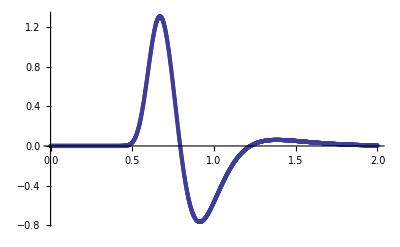
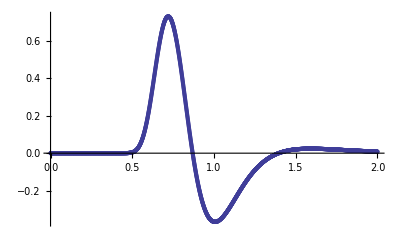
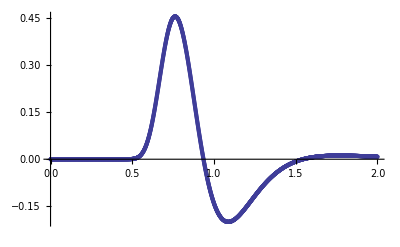
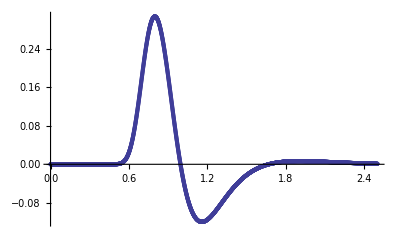

```mathematica
{ListPlot[pressurer4wid0pt5list,PlotRange->All],ListPlot[pressurer3pt3wid0pt5list,PlotRange->All],ListPlot[pressurer2pt25wid0pt5list,PlotRange->All],ListPlot[pressurer2wid0pt5list,PlotRange->All],ListPlot[pressurer1pt6wid0pt5list,PlotRange->All],ListPlot[pressurer1pt4wid0pt5list,PlotRange->All],ListPlot[pressurer1pt25wid0pt5list,PlotRange->All],ListPlot[pressurer1pt1wid0pt5list,PlotRange->All],ListPlot[pressurer1wid0pt5list,PlotRange->All]}
```

```mathematica
widrangemin = -1;
widrangemax = 6;
```

```mathematica
tpeakwid0pt5list = {-1,-1,-1,-1,-1,-1,-1,-1,-1};
```

```mathematica
n= 1
temp = pressurer4wid0pt5listϵ;
tempy = Table[temp[[i,2]],{i,1,Length[temp]}];
Position[temp,Max[tempy[[;;500]]]](*[[;;790]]*)
temp[[%[[1,1]]]]
tpeakwid0pt5list[[n]] = {1/0.25,%[[1]]}
Cr4wid0pt5= Table[NSolve[%[[2]]==C (-3/4(-1))^(1/4)1/(4+wid*i),C][[1,1,2]],{i,widrangemin,widrangemax}]
```

1

{{387,2}}

{0.359213,300.984}

{4.,0.359213}

{1.351,1.544,1.737,1.93,2.123,2.316,2.509,2.702}

```mathematica
n=2
temp = pressurer3pt3wid0pt5listϵ;
tempy = Table[temp[[i,2]],{i,1,Length[temp]}];
Position[temp,Max[tempy[[;;900]]]](*[[;;1000]]*)
temp[[%[[1,1]]]]
tpeakwid0pt5list[[n]] = {1/0.3,%[[1]]}
Cr3pt3wid0pt5= Table[NSolve[%[[2]]==C (-3/4(-1))^(1/4)1/((1/.3)+wid*i),C][[1,1,2]],{i,widrangemin,widrangemax}]
```

2

{{442,2}}

{0.410397,29.5588}

{3.33333,0.410397}

{1.2495,1.47,1.6905,1.911,2.1315,2.352,2.5725,2.793}

```mathematica
n=3
temp = pressurer2pt25wid0pt5listϵ;
tempy = Table[temp[[i,2]],{i,1,Length[temp]}];
Position[temp,Max[tempy[[;;800]]]](*[[;;1000]]*)
temp[[%[[1,1]]]]
tpeakwid0pt5list[[n]] =  {1/0.4,%[[1]]}
Cr2pt25wid0pt5= Table[NSolve[%[[2]]==C (-3/4(-1))^(1/4)1/((1/.4)+wid*i),C][[1,1,2]],{i,widrangemin,widrangemax}]
```

3

{{534,2}}

{0.496012,7.40777}

{2.5,0.496012}

{1.066,1.3325,1.599,1.8655,2.132,2.3985,2.665,2.9315}

```mathematica
n=4
temp = pressurer2wid0pt5listϵ;
tempy = Table[temp[[i,2]],{i,1,Length[temp]}];
Position[temp,Max[tempy[[;;1100]]]](*[[;;1000]]*)
temp[[%[[1,1]]]]
tpeakwid0pt5list[[n]] = {1/0.5,%[[1]]}
Cr2wid0pt5= Table[NSolve[%[[2]]==C (-3/4(-1))^(1/4)1/((1/.5)+wid*i),C][[1,1,2]],{i,widrangemin,widrangemax}]
```

4

{{609,2}}

{0.565808,11.0388}

{2.,0.565808}

{0.912,1.216,1.52,1.824,2.128,2.432,2.736,3.04}

```mathematica
n=5
temp = pressurer1pt6wid0pt5listϵ;
tempy = Table[temp[[i,2]],{i,1,Length[temp]}];
Position[temp,Max[tempy[[;;1300]]]](*[[;;1400]]*)
temp[[%[[1,1]]]]
tpeakwid0pt5list[[n]] =  {1/0.6,%[[1]]}
Cr1pt6wid0pt5= Table[NSolve[%[[2]]==C (-3/4(-1))^(1/4)1/((1/.6)+wid*i),C][[1,1,2]],{i,widrangemin,widrangemax}]
```

5

{{670,2}}

{0.622575,1.30921}

{1.66667,0.622575}

{0.7805,1.115,1.4495,1.784,2.1185,2.453,2.7875,3.122}

```mathematica
n=6
temp = pressurer1pt4wid0pt5listϵ;
tempy = Table[temp[[i,2]],{i,1,Length[temp]}];
Position[temp,Max[tempy[[;;1520]]]](*[[;;1400]]*)
temp[[%[[1,1]]]]
tpeakwid0pt5list[[n]] =  {1/0.7,%[[1]]}
Cr1pt4wid0pt5= Table[NSolve[%[[2]]==C (-3/4(-1))^(1/4)1/((1/.7)+wid*i),C][[1,1,2]],{i,widrangemin,widrangemax}]
```

6

{{721,2}}

{0.670035,0.729016}

{1.42857,0.670035}

{0.668571,1.02857,1.38857,1.74857,2.10857,2.46857,2.82857,3.18857}

```mathematica
n=7
temp = pressurer1pt25wid0pt5listϵ;
tempy = Table[temp[[i,2]],{i,1,Length[temp]}];
Position[temp,Max[tempy[[;;1000]]]]
temp[[%[[1,1]]]]
tpeakwid0pt5list[[n]] =  {1/0.8,%[[1]]}
Cr1pt25wid0pt5= Table[NSolve[%[[2]]==C (-3/4(-1))^(1/4)1/((1/.8)+wid*i),C][[1,1,2]],{i,widrangemin,widrangemax}]
```

7

{{763,2}}

{0.709121,0.454238}

{1.25,0.709121}

{0.5715,0.9525,1.3335,1.7145,2.0955,2.4765,2.8575,3.2385}

```mathematica
n=8
temp = pressurer1pt1wid0pt5listϵ;
tempy = Table[temp[[i,2]],{i,1,Length[temp]}];
Position[temp,Max[tempy[[;;2000]]]](*[[;;1000]]*)
temp[[%[[1,1]]]]
tpeakwid0pt5list[[n]] =  {1/0.9,%[[1]]}
Cr1pt1wid0pt5= Table[NSolve[%[[2]]==C (-3/4(-1))^(1/4)1/((1/.9)+wid*i),C][[1,1,2]],{i,widrangemin,widrangemax}]
```

8

{{799,2}}

{0.742623,0.3073}

{1.11111,0.742623}

{0.487667,0.886667,1.28567,1.68467,2.08367,2.48267,2.88167,3.28067}

```mathematica
n=9
temp = pressurer1wid0pt5listϵ;
tempy = Table[temp[[i,2]],{i,1,Length[temp]}];
Position[temp,Max[tempy[[;;2200]]]]
temp[[%[[1,1]]]]
tpeakwid0pt5list[[n]] = {1.,%[[1]]}
Cr1wid0pt5= Table[NSolve[%[[2]]==C (-3/4(-1))^(1/4)1/(1.0+wid*i),C][[1,1,2]],{i,widrangemin,widrangemax}]
```

9

{{829,2}}

{0.770541,0.884965}

{1.,0.770541}

{0.414,0.828,1.242,1.656,2.07,2.484,2.898,3.312}

```mathematica
tpeakwid0pt5list
nlist = Table[i,{i,widrangemin,widrangemax}];
nlist = Append[nlist,2.5];
nlist = Sort[nlist]
Cvsuavewid0pt5list = Table[{1/tpeakwid0pt5list[[i,1]],(NSolve[tpeakwid0pt5list[[i,2]]==C (-3/4(-1))^(1/4)1/((tpeakwid0pt5list[[i,1]])+wid*nlist[[j]]),C])[[1,1,2]]},{j,1,Length[nlist]},{i,1,9}]
tpeakvsueffwid0pt5list = Table[{1/(tpeakwid0pt5list[[i,1]]+wid*nlist[[j]]),tpeakwid0pt5list[[i,2]]},{j,1,Length[nlist]},{i,1,9}]
```

{{4.,0.359213},{3.33333,0.410397},{2.5,0.496012},{2.,0.565808},{1.66667,0.622575},{1.42857,0.670035},{1.25,0.709121},{1.11111,0.742623},{1.,0.770541}}

{-1,0,1,2,2.5,3,4,5,6}

{{{0.25,1.351},{0.3,1.2495},{0.4,1.066},{0.5,0.912},{0.6,0.7805},{0.7,0.668571},{0.8,0.5715},{0.9,0.487667},{1.,0.414}},{{0.25,1.544},{0.3,1.47},{0.4,1.3325},{0.5,1.216},{0.6,1.115},{0.7,1.02857},{0.8,0.9525},{0.9,0.886667},{1.,0.828}},{{0.25,1.737},{0.3,1.6905},{0.4,1.599},{0.5,1.52},{0.6,1.4495},{0.7,1.38857},{0.8,1.3335},{0.9,1.28567},{1.,1.242}},{{0.25,1.93},{0.3,1.911},{0.4,1.8655},{0.5,1.824},{0.6,1.784},{0.7,1.74857},{0.8,1.7145},{0.9,1.68467},{1.,1.656}},{{0.25,2.0265},{0.3,2.02125},{0.4,1.99875},{0.5,1.976},{0.6,1.95125},{0.7,1.92857},{0.8,1.905},{0.9,1.88417},{1.,1.863}},{{0.25,2.123},{0.3,2.1315},{0.4,2.132},{0.5,2.128},{0.6,2.1185},{0.7,2.10857},{0.8,2.0955},{0.9,2.08367},{1.,2.07}},{{0.25,2.316},{0.3,2.352},{0.4,2.3985},{0.5,2.432},{0.6,2.453},{0.7,2.46857},{0.8,2.4765},{0.9,2.48267},{1.,2.484}},{{0.25,2.509},{0.3,2.5725},{0.4,2.665},{0.5,2.736},{0.6,2.7875},{0.7,2.82857},{0.8,2.8575},{0.9,2.88167},{1.,2.898}},{{0.25,2.702},{0.3,2.793},{0.4,2.9315},{0.5,3.04},{0.6,3.122},{0.7,3.18857},{0.8,3.2385},{0.9,3.28067},{1.,3.312}}}

{{{0.285714,0.359213},{0.352941,0.410397},{0.5,0.496012},{0.666667,0.565808},{0.857143,0.622575},{1.07692,0.670035},{1.33333,0.709121},{1.63636,0.742623},{2.,0.770541}},{{0.25,0.359213},{0.3,0.410397},{0.4,0.496012},{0.5,0.565808},{0.6,0.622575},{0.7,0.670035},{0.8,0.709121},{0.9,0.742623},{1.,0.770541}},{{0.222222,0.359213},{0.26087,0.410397},{0.333333,0.496012},{0.4,0.565808},{0.461538,0.622575},{0.518519,0.670035},{0.571429,0.709121},{0.62069,0.742623},{0.666667,0.770541}},{{0.2,0.359213},{0.230769,0.410397},{0.285714,0.496012},{0.333333,0.565808},{0.375,0.622575},{0.411765,0.670035},{0.444444,0.709121},{0.473684,0.742623},{0.5,0.770541}},{{0.190476,0.359213},{0.218182,0.410397},{0.266667,0.496012},{0.307692,0.565808},{0.342857,0.622575},{0.373333,0.670035},{0.4,0.709121},{0.423529,0.742623},{0.444444,0.770541}},{{0.181818,0.359213},{0.206897,0.410397},{0.25,0.496012},{0.285714,0.565808},{0.315789,0.622575},{0.341463,0.670035},{0.363636,0.709121},{0.382979,0.742623},{0.4,0.770541}},{{0.166667,0.359213},{0.1875,0.410397},{0.222222,0.496012},{0.25,0.565808},{0.272727,0.622575},{0.291667,0.670035},{0.307692,0.709121},{0.321429,0.742623},{0.333333,0.770541}},{{0.153846,0.359213},{0.171429,0.410397},{0.2,0.496012},{0.222222,0.565808},{0.24,0.622575},{0.254545,0.670035},{0.266667,0.709121},{0.276923,0.742623},{0.285714,0.770541}},{{0.142857,0.359213},{0.157895,0.410397},{0.181818,0.496012},{0.2,0.565808},{0.214286,0.622575},{0.225806,0.670035},{0.235294,0.709121},{0.243243,0.742623},{0.25,0.770541}}}

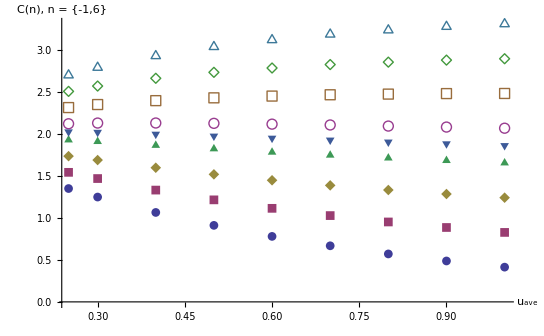

```mathematica
ListPlot[Cvsuavewid0pt5list,PlotMarkers->Automatic,AxesLabel->{"u_ave","C(n), n = {-1,6}"},AxesStyle->Large]
```

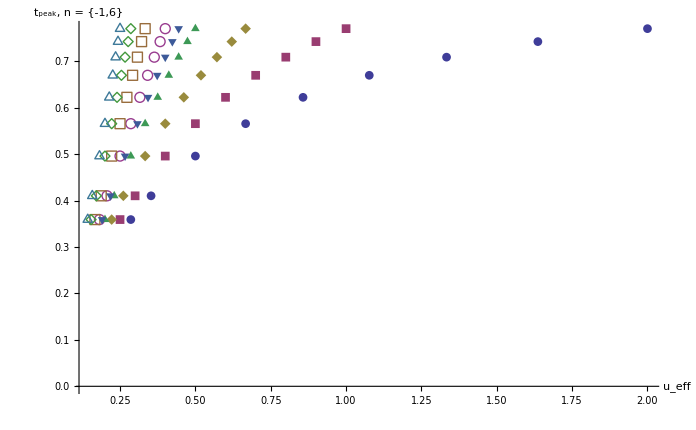

```mathematica
ListPlot[tpeakvsueffwid0pt5list,PlotMarkers->Automatic,AxesLabel->{"u_eff","t_peak, n = {-1,6}"},AxesStyle->Large,PlotRange->All]
```

## Uncharged Data

## GaussianR Bsub, f3 = (0%), fxy = 0.0 wid = 0.5 N = 240 ** rave = 4

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\Important\\SpecMethOutputsetupgN240amp0.02wid0.5uave0.25a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\Important\SpecMethOutputsetupgN240amp0.02wid0.5uave0.25a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

3.41061×10^-13

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.81899×10^-12

```mathematica
Max[Abs[ABCcheckDlist]]
```

7.92928×10^-9

```mathematica
Max[Abs[ABCcheckNlist]]
```

8.73115×10^-11

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99534×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-0.133607,2.25218×10^-9}

Here the spike is quite large, and this is for a small fxy.

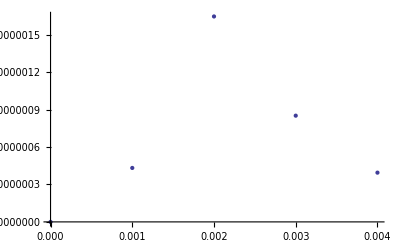

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

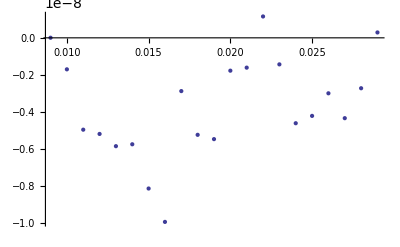

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

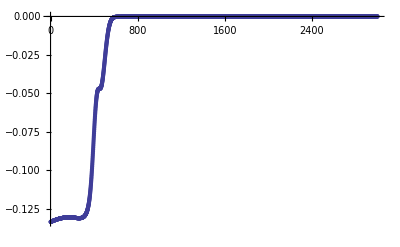

```mathematica
ListPlot[lamblist,PlotRange->All]
```

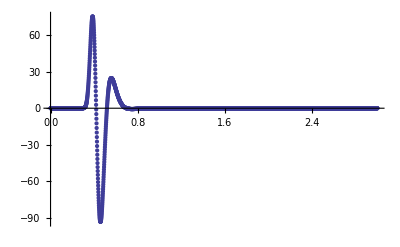

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

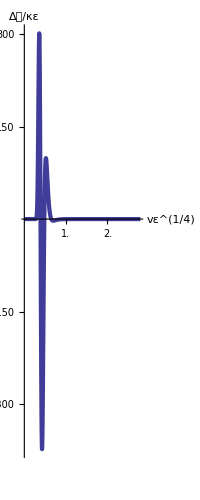

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurer4wid0pt5list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurer4wid0pt5listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
Plotpressurer4wid0pt5ϵ = ListPlot[pressurer4wid0pt5listϵ ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{-300,-150,150,300}},ImageSize->{{300},{200}},AspectRatio->Full]
```

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-4.02299×10^-12

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

## GaussianR Bsub, f3 = (0%), fxy = 0.0 wid = 0.5 N = 240 ** rave = 3.3 ish

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.5uave0.3a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS1000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.5uave0.3a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS1000FF.h5

```mathematica
"C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.5uave0.3a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS1000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.5uave0.3a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS1000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

6.21725×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

2.84217×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.5424×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.59162×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.97613×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-0.0028851,-5.24781×10^-7}

Here the spike is quite large, and this is for a small fxy.

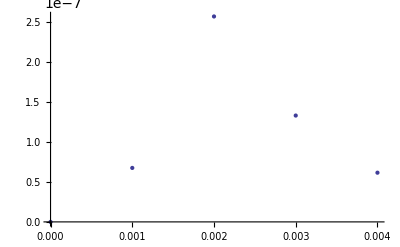

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

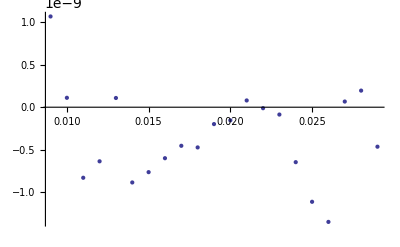

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

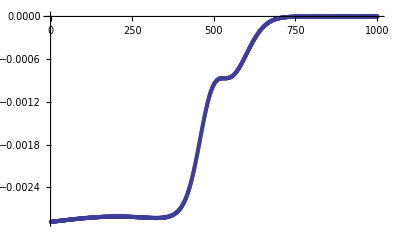

```mathematica
ListPlot[lamblist,PlotRange->All]
```

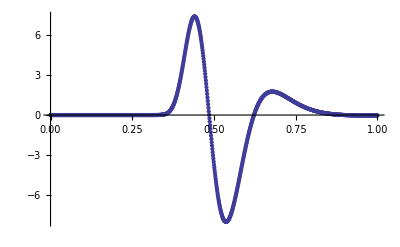

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

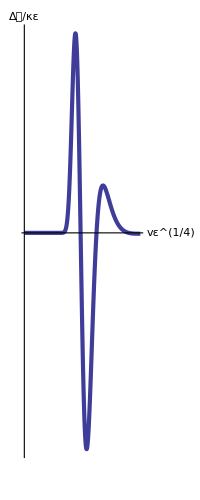

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurer3pt3wid0pt5list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurer3pt3wid0pt5listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
Plotpressurer3pt3wid0pt5ϵ = ListPlot[pressurer3pt3wid0pt5listϵ ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{-300,-150,150,300}},ImageSize->{{300},{200}},AspectRatio->Full]
```

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.318311

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-1.87153×10^-7

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

## GaussianR Bsub, f3 = (0%), fxy = 0.0 wid = 0.5 N = 240 ** rave = 2.5

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.5uave0.4a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS1000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.5uave0.4a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS1000FF.h5

```mathematica
"C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.5uave0.4a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS1000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.5uave0.4a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS1000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

3.88578×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

7.10543×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

3.1583×10^-11

```mathematica
Max[Abs[ABCcheckNlist]]
```

3.41061×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.87516×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-0.000777538,-2.28025×10^-6}

Here the spike is quite large, and this is for a small fxy.

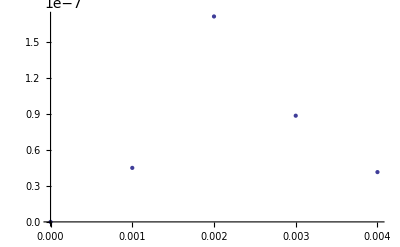

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

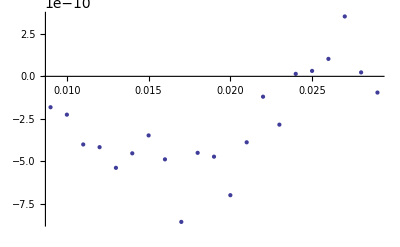

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

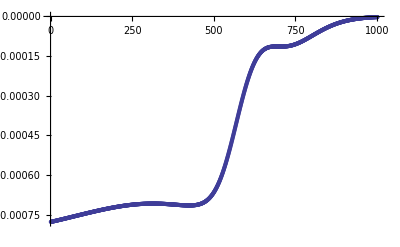

```mathematica
ListPlot[lamblist,PlotRange->All]
```

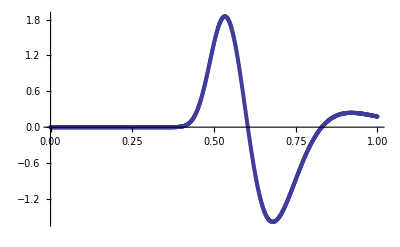

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

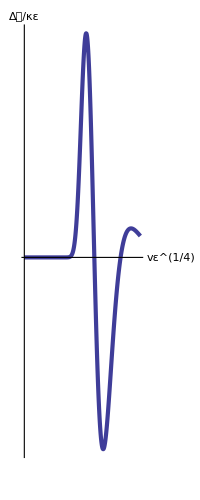

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurer2pt25wid0pt5list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurer2pt25wid0pt5listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
Plotpressurer2pt25wid0pt5ϵ = ListPlot[pressurer2pt25wid0pt5listϵ ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{-300,-150,150,300}},ImageSize->{{300},{200}},AspectRatio->Full]
```

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.318309

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-1.13775×10^-7

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14157

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.249989

## GaussianR Bsub, f3 = (0%), fxy = 0.0 wid = 0.5 N = 240 ** rave = 2

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\Important\\SpecMethOutputsetupgN240amp0.02wid0.5uave0.5a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\Important\SpecMethOutputsetupgN240amp0.02wid0.5uave0.5a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.55431×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.98952×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.56319×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.5181×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.59162×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.88692×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-0.00472683,1.60751×10^-9}

Here the spike is quite large, and this is for a small fxy.

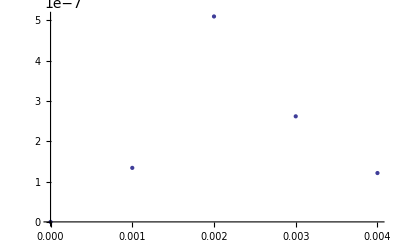

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

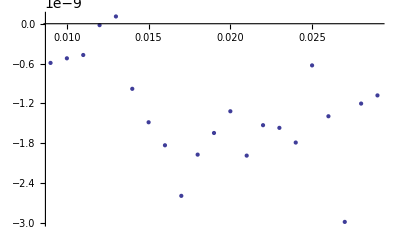

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

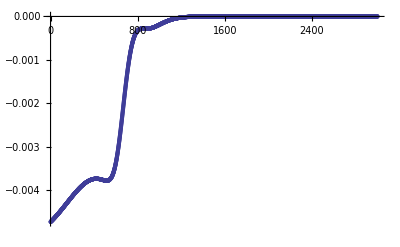

```mathematica
ListPlot[lamblist,PlotRange->All]
```

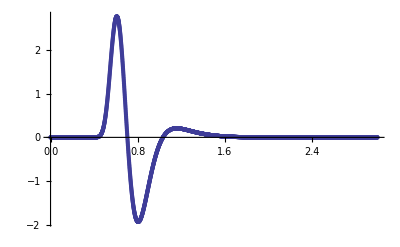

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

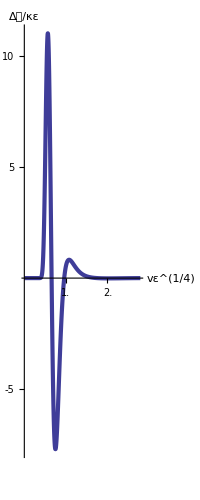

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurer2wid0pt5list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurer2wid0pt5listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
Plotpressurer2wid0pt5ϵ = ListPlot[pressurer2wid0pt5listϵ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{-5,5,10}},ImageSize->{{300},{200}},AspectRatio->Full]
```

```mathematica
ListPlot[pressurepos2listϵ,PlotRange->All]
```

ListPlot::lpn: pressurepos2listϵ is not a list of numbers or pairs of numbers.

ListPlot[pressurepos2listϵ,PlotRange→All]

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-2.65795×10^-10

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

## GaussianR Bsub, f3 = (0%), fxy = 0.0 wid = 0.5 N = 240 ** rave = 1.6 ish

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.5uave0.6a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.5uave0.6a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

2.42861×10^-17

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.42109×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

3.05489×10^-12

```mathematica
Max[Abs[ABCcheckNlist]]
```

9.02611×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.95676×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-0.000135958,-2.80088×10^-9}

Here the spike is quite large, and this is for a small fxy.

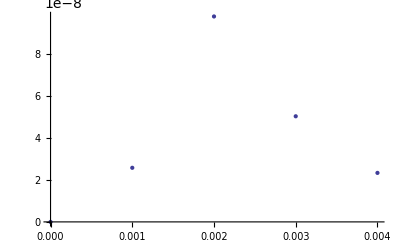

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

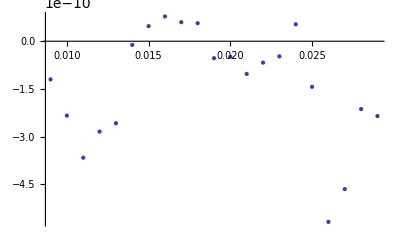

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

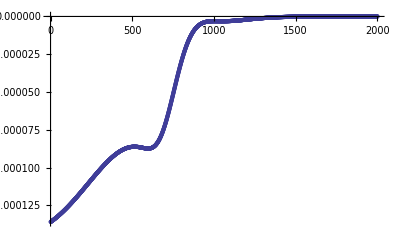

```mathematica
ListPlot[lamblist,PlotRange->All]
```

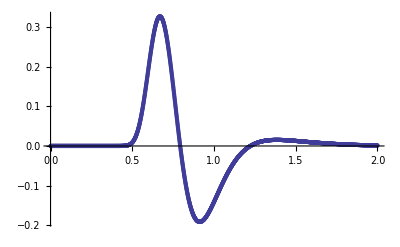

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

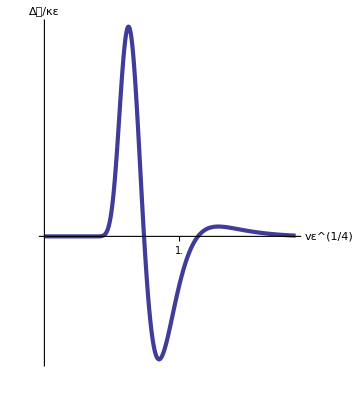

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurer1pt6wid0pt5list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurer1pt6wid0pt5listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
Plotpressurer1pt6wid0pt5ϵ = ListPlot[pressurer1pt6wid0pt5listϵ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{-5,5,10}},ImageSize->{{300},{200}},AspectRatio->Full]
```

```mathematica
ListPlot[pressurepos2listϵ,PlotRange->All]
```

ListPlot::lpn: pressurepos2listϵ is not a list of numbers or pairs of numbers.

ListPlot[pressurepos2listϵ,PlotRange→All]

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-3.77338×10^-9

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

## GaussianR Bsub, f3 = (0%), fxy = 0.0 wid = 0.5 N = 240 ** rave = 1.4 ish

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.5uave0.7a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.5uave0.7a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.38778×10^-17

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.84741×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

7.99361×10^-15

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.22635×10^-12

```mathematica
Max[Abs[ABCcheckNlist]]
```

9.67559×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.91468×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-0.0000725771,5.1865×10^-10}

Here the spike is quite large, and this is for a small fxy.

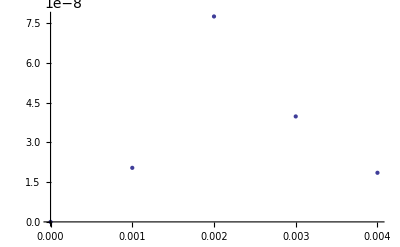

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

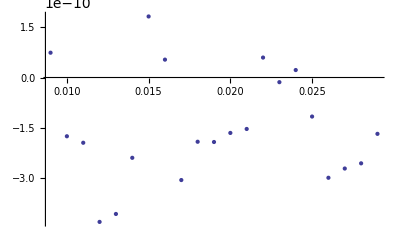

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

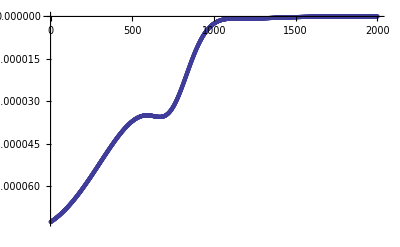

```mathematica
ListPlot[lamblist,PlotRange->All]
```

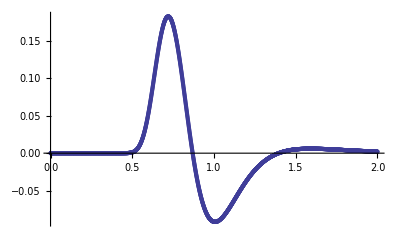

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

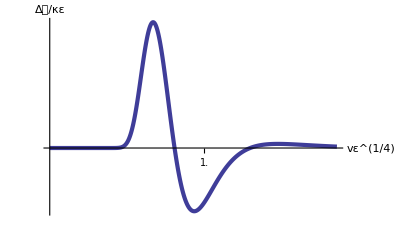

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurer1pt4wid0pt5list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurer1pt4wid0pt5listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
Plotpressurer1pt4wid0pt5ϵ = ListPlot[pressurer1pt4wid0pt5listϵ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{-5,5,10}},ImageSize->{{300},{200}},AspectRatio->Full]
```

```mathematica
ListPlot[pressurepos2listϵ,PlotRange->All]
```

ListPlot::lpn: pressurepos2listϵ is not a list of numbers or pairs of numbers.

ListPlot[pressurepos2listϵ,PlotRange→All]

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-1.14784×10^-9

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

## GaussianR Bsub, f3 = (0%), fxy = 0.0 wid = 0.5 N = 240 ** rave = 1.25

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.5uave0.8a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.5uave0.8a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

6.93889×10^-18

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

5.32907×10^-15

```mathematica
Max[Abs[ABCcheckDlist]]
```

5.38458×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

9.88098×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.87799×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-0.0000426573,-1.0015×10^-9}

Here the spike is quite large, and this is for a small fxy.

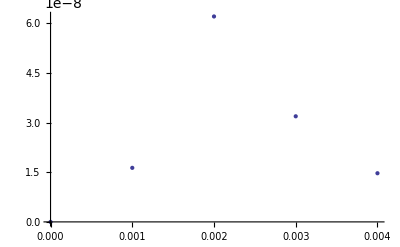

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

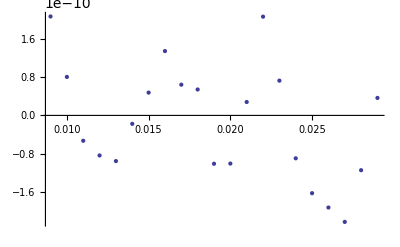

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

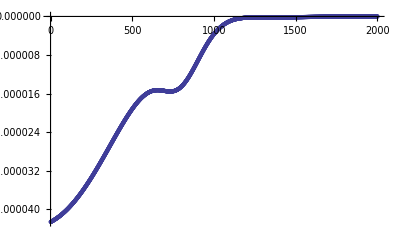

```mathematica
ListPlot[lamblist,PlotRange->All]
```

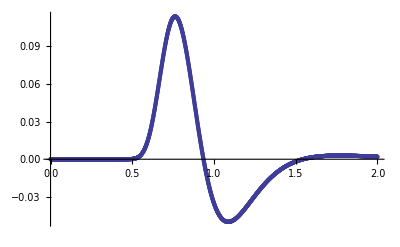

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurer1pt25wid0pt5list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurer1pt25wid0pt5listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
Plotpressurer1pt25wid0pt5ϵ = ListPlot[pressurer1pt25wid0pt5listϵ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{-5,5,10}},ImageSize->{{300},{200}},AspectRatio->Full]
```

-Graphics-

```mathematica
ListPlot[pressurepos2listϵ,PlotRange->All]
```

ListPlot::lpn: pressurepos2listϵ is not a list of numbers or pairs of numbers.

ListPlot[pressurepos2listϵ,PlotRange→All]

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-3.92649×10^-10

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

## GaussianR Bsub, f3 = (0%), fxy = 0.0 wid = 0.5 N = 240 ** rave = 1.11 ish

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.5uave0.9a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS2500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.5uave0.9a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS2500FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

3.03577×10^-18

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.84741×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

5.32907×10^-15

```mathematica
Max[Abs[ABCcheckDlist]]
```

4.89608×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

9.67733×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.88504×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-0.0000268804,2.05975×10^-9}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurer1pt1wid0pt5list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurer1pt1wid0pt5listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
Plotpressurer1pt1wid0pt5ϵ = ListPlot[pressurer1pt1wid0pt5listϵ ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{-0.25,0.25,0.75}},ImageSize->{{300},{200}},AspectRatio->Full]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-1.41499×10^-10

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

## GaussianR Bsub, f3 = (0%), fxy = 0.0 wid = 0.5 N = 240 ** rave = 1

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\Important\\SpecMethOutputsetupgN240amp0.02wid0.5uave1.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\Important\SpecMethOutputsetupgN240amp0.02wid0.5uave1.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5

```mathematica
"C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\Important\\SpecMethOutputsetupgN240amp0.02wid0.5uave1.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\Important\SpecMethOutputsetupgN240amp0.02wid0.5uave1.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

3.46945×10^-17

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

2.13163×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.59872×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

3.27138×10^-12

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.1724×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.96814×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-0.000286243,1.93102×10^-9}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurer1wid0pt5list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurer1wid0pt5listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
Plotpressurer1wid0pt5ϵ = ListPlot[pressurer1wid0pt5listϵ ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{-0.25,0.25,0.75}},ImageSize->{{300},{200}},AspectRatio->Full]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-8.06606×10^-11

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

## RN Plots

```mathematica
{ListPlot[pressurer4wid0pt5RNlist,PlotRange->All],ListPlot[pressurer3pt3wid0pt5RNlist,PlotRange->All],ListPlot[pressurer2pt25wid0pt5RNlist,PlotRange->All],ListPlot[pressurer2wid0pt5RNlist,PlotRange->All],ListPlot[pressurer1pt6wid0pt5RNlist,PlotRange->All],ListPlot[pressurer1pt4wid0pt5RNlist,PlotRange->All],ListPlot[pressurer1pt25wid0pt5RNlist,PlotRange->All],ListPlot[pressurer1pt1wid0pt5RNlist,PlotRange->All],ListPlot[pressurer1wid0pt5RNlist,PlotRange->All]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
widrangemin = -1;
widrangemax = 6;
```

```mathematica
tpeakwid0pt5RNlist = {-1,-1,-1,-1,-1,-1,-1,-1,-1};
```

```mathematica
n= 1
temp = pressurer4wid0pt5RNlistϵ;
tempy = Table[temp[[i,2]],{i,1,Length[temp]}];
Position[temp,Max[tempy[[;;500]]]](*[[;;790]]*)
temp[[%[[1,1]]]]
tpeakwid0pt5RNlist[[n]] = {1/0.25,%[[1]]}
Cr4wid0pt5RN= Table[NSolve[%[[2]]==C (-3/4(-1))^(1/4)1/(4+wid*i),C][[1,1,2]],{i,widrangemin,widrangemax}]
```

1

{{387,2}}

{0.359213,75.2496}

{4.,0.359213}

{1.351,1.544,1.737,1.93,2.123,2.316,2.509,2.702}

```mathematica
n=2
temp = pressurer3pt3wid0pt5RNlistϵ;
tempy = Table[temp[[i,2]],{i,1,Length[temp]}];
Position[temp,Max[tempy[[;;900]]]](*[[;;1000]]*)
temp[[%[[1,1]]]]
tpeakwid0pt5RNlist[[n]] = {1/0.3,%[[1]]}
Cr3pt3wid0pt5RN= Table[NSolve[%[[2]]==C (-3/4(-1))^(1/4)1/((1/.3)+wid*i),C][[1,1,2]],{i,widrangemin,widrangemax}]
```

2

{{442,2}}

{0.410397,29.5614}

{3.33333,0.410397}

{1.2495,1.47,1.6905,1.911,2.1315,2.352,2.5725,2.793}

```mathematica
n=3
temp = pressurer2pt25wid0pt5RNlistϵ;
tempy = Table[temp[[i,2]],{i,1,Length[temp]}];
Position[temp,Max[tempy[[;;800]]]](*[[;;1000]]*)
temp[[%[[1,1]]]]
tpeakwid0pt5RNlist[[n]] =  {1/0.4,%[[1]]}
Cr2pt25wid0pt5RN= Table[NSolve[%[[2]]==C (-3/4(-1))^(1/4)1/((1/.4)+wid*i),C][[1,1,2]],{i,widrangemin,widrangemax}]
```

3

{{534,2}}

{0.496012,7.40993}

{2.5,0.496012}

{1.066,1.3325,1.599,1.8655,2.132,2.3985,2.665,2.9315}

```mathematica
n=4
temp = pressurer2wid0pt5RNlistϵ;
tempy = Table[temp[[i,2]],{i,1,Length[temp]}];
Position[temp,Max[tempy[[;;1100]]]](*[[;;1000]]*)
temp[[%[[1,1]]]]
tpeakwid0pt5RNlist[[n]] = {1/0.5,%[[1]]}
Cr2wid0pt5RN= Table[NSolve[%[[2]]==C (-3/4(-1))^(1/4)1/((1/.5)+wid*i),C][[1,1,2]],{i,widrangemin,widrangemax}]
```

4

{{609,2}}

{0.565808,2.76152}

{2.,0.565808}

{0.912,1.216,1.52,1.824,2.128,2.432,2.736,3.04}

```mathematica
n=5
temp = pressurer1pt6wid0pt5RNlistϵ;
tempy = Table[temp[[i,2]],{i,1,Length[temp]}];
Position[temp,Max[tempy[[;;1300]]]](*[[;;1400]]*)
temp[[%[[1,1]]]]
tpeakwid0pt5RNlist[[n]] =  {1/0.6,%[[1]]}
Cr1pt6wid0pt5RN= Table[NSolve[%[[2]]==C (-3/4(-1))^(1/4)1/((1/.6)+wid*i),C][[1,1,2]],{i,widrangemin,widrangemax}]
```

5

{{670,2}}

{0.622575,1.31077}

{1.66667,0.622575}

{0.7805,1.115,1.4495,1.784,2.1185,2.453,2.7875,3.122}

```mathematica
n=6
temp = pressurer1pt4wid0pt5RNlistϵ;
tempy = Table[temp[[i,2]],{i,1,Length[temp]}];
Position[temp,Max[tempy[[;;1520]]]](*[[;;1400]]*)
temp[[%[[1,1]]]]
tpeakwid0pt5RNlist[[n]] =  {1/0.7,%[[1]]}
Cr1pt4wid0pt5RN= Table[NSolve[%[[2]]==C (-3/4(-1))^(1/4)1/((1/.7)+wid*i),C][[1,1,2]],{i,widrangemin,widrangemax}]
```

6

{{721,2}}

{0.670035,0.730385}

{1.42857,0.670035}

{0.668571,1.02857,1.38857,1.74857,2.10857,2.46857,2.82857,3.18857}

```mathematica
n=7
temp = pressurer1pt25wid0pt5RNlistϵ;
tempy = Table[temp[[i,2]],{i,1,Length[temp]}];
Position[temp,Max[tempy[[;;1000]]]]
temp[[%[[1,1]]]]
tpeakwid0pt5RNlist[[n]] =  {1/0.8,%[[1]]}
Cr1pt25wid0pt5RN= Table[NSolve[%[[2]]==C (-3/4(-1))^(1/4)1/((1/.8)+wid*i),C][[1,1,2]],{i,widrangemin,widrangemax}]
```

7

{{763,2}}

{0.709121,0.455451}

{1.25,0.709121}

{0.5715,0.9525,1.3335,1.7145,2.0955,2.4765,2.8575,3.2385}

```mathematica
n=8
temp = pressurer1pt1wid0pt5RNlistϵ;
tempy = Table[temp[[i,2]],{i,1,Length[temp]}];
Position[temp,Max[tempy[[;;2000]]]](*[[;;1000]]*)
temp[[%[[1,1]]]]
tpeakwid0pt5RNlist[[n]] =  {1/0.9,%[[1]]}
Cr1pt1wid0pt5RN= Table[NSolve[%[[2]]==C (-3/4(-1))^(1/4)1/((1/.9)+wid*i),C][[1,1,2]],{i,widrangemin,widrangemax}]
```

8

{{799,2}}

{0.742623,0.308391}

{1.11111,0.742623}

{0.487667,0.886667,1.28567,1.68467,2.08367,2.48267,2.88167,3.28067}

```mathematica
n=9
temp = pressurer1wid0pt5RNlistϵ;
tempy = Table[temp[[i,2]],{i,1,Length[temp]}];
Position[temp,Max[tempy[[;;2200]]]]
temp[[%[[1,1]]]]
tpeakwid0pt5RNlist[[n]] = {1.,%[[1]]}
Cr1wid0pt5RN= Table[NSolve[%[[2]]==C (-3/4(-1))^(1/4)1/(1.0+wid*i),C][[1,1,2]],{i,widrangemin,widrangemax}]
```

9

{{829,2}}

{0.770541,0.222229}

{1.,0.770541}

{0.414,0.828,1.242,1.656,2.07,2.484,2.898,3.312}

```mathematica
tpeakwid0pt5RNlist
nlist = Table[i,{i,widrangemin,widrangemax}];
nlist = Append[nlist,2.5];
nlist = Sort[nlist]
Cvsuavewid0pt5RNlist = Table[{1/tpeakwid0pt5RNlist[[i,1]],(NSolve[tpeakwid0pt5RNlist[[i,2]]==C (-3/4(-1))^(1/4)1/((tpeakwid0pt5RNlist[[i,1]])+wid*nlist[[j]]),C])[[1,1,2]]},{j,1,Length[nlist]},{i,1,9}]
tpeakvsueffwid0pt5RNlist = Table[{1/(tpeakwid0pt5RNlist[[i,1]]+wid*nlist[[j]]),tpeakwid0pt5RNlist[[i,2]]},{j,1,Length[nlist]},{i,1,9}]
```

{{4.,0.359213},{3.33333,0.410397},{2.5,0.496012},{2.,0.565808},{1.66667,0.622575},{1.42857,0.670035},{1.25,0.709121},{1.11111,0.742623},{1.,0.770541}}

{-1,0,1,2,2.5,3,4,5,6}

{{{0.25,1.351},{0.3,1.2495},{0.4,1.066},{0.5,0.912},{0.6,0.7805},{0.7,0.668571},{0.8,0.5715},{0.9,0.487667},{1.,0.414}},{{0.25,1.544},{0.3,1.47},{0.4,1.3325},{0.5,1.216},{0.6,1.115},{0.7,1.02857},{0.8,0.9525},{0.9,0.886667},{1.,0.828}},{{0.25,1.737},{0.3,1.6905},{0.4,1.599},{0.5,1.52},{0.6,1.4495},{0.7,1.38857},{0.8,1.3335},{0.9,1.28567},{1.,1.242}},{{0.25,1.93},{0.3,1.911},{0.4,1.8655},{0.5,1.824},{0.6,1.784},{0.7,1.74857},{0.8,1.7145},{0.9,1.68467},{1.,1.656}},{{0.25,2.0265},{0.3,2.02125},{0.4,1.99875},{0.5,1.976},{0.6,1.95125},{0.7,1.92857},{0.8,1.905},{0.9,1.88417},{1.,1.863}},{{0.25,2.123},{0.3,2.1315},{0.4,2.132},{0.5,2.128},{0.6,2.1185},{0.7,2.10857},{0.8,2.0955},{0.9,2.08367},{1.,2.07}},{{0.25,2.316},{0.3,2.352},{0.4,2.3985},{0.5,2.432},{0.6,2.453},{0.7,2.46857},{0.8,2.4765},{0.9,2.48267},{1.,2.484}},{{0.25,2.509},{0.3,2.5725},{0.4,2.665},{0.5,2.736},{0.6,2.7875},{0.7,2.82857},{0.8,2.8575},{0.9,2.88167},{1.,2.898}},{{0.25,2.702},{0.3,2.793},{0.4,2.9315},{0.5,3.04},{0.6,3.122},{0.7,3.18857},{0.8,3.2385},{0.9,3.28067},{1.,3.312}}}

{{{0.285714,0.359213},{0.352941,0.410397},{0.5,0.496012},{0.666667,0.565808},{0.857143,0.622575},{1.07692,0.670035},{1.33333,0.709121},{1.63636,0.742623},{2.,0.770541}},{{0.25,0.359213},{0.3,0.410397},{0.4,0.496012},{0.5,0.565808},{0.6,0.622575},{0.7,0.670035},{0.8,0.709121},{0.9,0.742623},{1.,0.770541}},{{0.222222,0.359213},{0.26087,0.410397},{0.333333,0.496012},{0.4,0.565808},{0.461538,0.622575},{0.518519,0.670035},{0.571429,0.709121},{0.62069,0.742623},{0.666667,0.770541}},{{0.2,0.359213},{0.230769,0.410397},{0.285714,0.496012},{0.333333,0.565808},{0.375,0.622575},{0.411765,0.670035},{0.444444,0.709121},{0.473684,0.742623},{0.5,0.770541}},{{0.190476,0.359213},{0.218182,0.410397},{0.266667,0.496012},{0.307692,0.565808},{0.342857,0.622575},{0.373333,0.670035},{0.4,0.709121},{0.423529,0.742623},{0.444444,0.770541}},{{0.181818,0.359213},{0.206897,0.410397},{0.25,0.496012},{0.285714,0.565808},{0.315789,0.622575},{0.341463,0.670035},{0.363636,0.709121},{0.382979,0.742623},{0.4,0.770541}},{{0.166667,0.359213},{0.1875,0.410397},{0.222222,0.496012},{0.25,0.565808},{0.272727,0.622575},{0.291667,0.670035},{0.307692,0.709121},{0.321429,0.742623},{0.333333,0.770541}},{{0.153846,0.359213},{0.171429,0.410397},{0.2,0.496012},{0.222222,0.565808},{0.24,0.622575},{0.254545,0.670035},{0.266667,0.709121},{0.276923,0.742623},{0.285714,0.770541}},{{0.142857,0.359213},{0.157895,0.410397},{0.181818,0.496012},{0.2,0.565808},{0.214286,0.622575},{0.225806,0.670035},{0.235294,0.709121},{0.243243,0.742623},{0.25,0.770541}}}

```mathematica
ListPlot[Cvsuavewid0pt5RNlist,PlotMarkers->Automatic,AxesLabel->{"u_ave","C(n), n = {-1,6}"},AxesStyle->Large]
```

-Graphics-

```mathematica
ListPlot[tpeakvsueffwid0pt5RNlist,PlotMarkers->Automatic,AxesLabel->{"u_eff","t_peak, n = {-1,6}"},AxesStyle->Large,PlotRange->All]
```

-Graphics-

## RN Data

## GaussianR Bsub, f3 = (80%), fxy = 0.0 wid = 0.5 N = 240 ** rave = 4

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.5uave0.25a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS1000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.5uave0.25a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS1000FF.h5

```mathematica
"C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.5uave0.25a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS1000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.5uave0.25a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS1000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

2.13163×10^-14

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.27898×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

3.41061×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

7.10895×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

6.36646×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.95592×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-0.0945397,-0.0830171}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurer4wid0pt5RNlist = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurer4wid0pt5RNlistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
Plotpressurer4wid0pt5RNϵ = ListPlot[pressurer4wid0pt5RNlistϵ ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{-300,-150,150,300}},ImageSize->{{300},{200}},AspectRatio->Full]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.231415

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.511178

```mathematica
chem/T
```

-2.20893

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-2.72499×10^-8

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

2.42233

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.189437

## GaussianR Bsub, f3 = (80%), fxy = 0.0 wid = 0.5 N = 240 ** rave = 3.3 ish

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.5uave0.3a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS1000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.5uave0.3a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS1000FF.h5

```mathematica
"C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.5uave0.3a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS1000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.5uave0.3a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS1000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

4.44089×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.27898×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

2.84217×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.52194×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

2.72848×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.95426×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-0.0878865,-0.0830179}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurer3pt3wid0pt5RNlist = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurer3pt3wid0pt5RNlistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
Plotpressurer3pt3wid0pt5RNϵ = ListPlot[pressurer3pt3wid0pt5RNlistϵ ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{-300,-150,150,300}},ImageSize->{{300},{200}},AspectRatio->Full]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.231415

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.511179

```mathematica
chem/T
```

-2.20893

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-2.12063×10^-7

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

2.42232

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.189438

## GaussianR Bsub, f3 = (80%), fxy = 0.0 wid = 0.5 N = 240 ** rave = 2.5

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.5uave0.4a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS1000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.5uave0.4a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS1000FF.h5

```mathematica
"C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.5uave0.4a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS1000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.5uave0.4a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS1000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

3.88578×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.27898×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

6.39488×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

5.29919×10^-11

```mathematica
Max[Abs[ABCcheckNlist]]
```

5.68434×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.87987×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-0.0843466,-0.0830207}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurer2pt25wid0pt5RNlist = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurer2pt25wid0pt5RNlistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
Plotpressurer2pt25wid0pt5RNϵ = ListPlot[pressurer2pt25wid0pt5RNlistϵ ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{-300,-150,150,300}},ImageSize->{{300},{200}},AspectRatio->Full]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.231412

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.511182

```mathematica
chem/T
```

-2.20897

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-1.09979×10^-7

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

2.4223

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.189451

## GaussianR Bsub, f3 = (80%), fxy = 0.0 wid = 0.5 N = 240 ** rave = 2

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.5uave0.5a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.5uave0.5a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5

```mathematica
"C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.5uave0.5a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.5uave0.5a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

9.71445×10^-17

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

2.84217×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.54623×10^-11

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.98952×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.65755×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-0.0835276,-0.083017}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurer2wid0pt5RNlist = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurer2wid0pt5RNlistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
Plotpressurer2wid0pt5RNϵ = ListPlot[pressurer2wid0pt5RNlistϵ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{-5,5,10}},ImageSize->{{300},{200}},AspectRatio->Full]
```

-Graphics-

```mathematica
ListPlot[pressurepos2listϵ,PlotRange->All]
```

ListPlot::lpn: pressurepos2listϵ is not a list of numbers or pairs of numbers.

ListPlot[pressurepos2listϵ,PlotRange→All]

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.231415

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.511178

```mathematica
chem/T
```

-2.20893

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-2.32502×10^-9

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

2.42233

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.189437

## GaussianR Bsub, f3 = (80%), fxy = 0.0 wid = 0.5 N = 240 ** rave = 1.6 ish

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.5uave0.6a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.5uave0.6a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5

```mathematica
"C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.5uave0.6a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.5uave0.6a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

4.16334×10^-17

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.59872×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

5.42744×10^-12

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.13687×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.89103×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-0.083259,-0.083017}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurer1pt6wid0pt5RNlist = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurer1pt6wid0pt5RNlistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
Plotpressurer1pt6wid0pt5RNϵ = ListPlot[pressurer1pt6wid0pt5RNlistϵ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{-5,5,10}},ImageSize->{{300},{200}},AspectRatio->Full]
```

-Graphics-

```mathematica
ListPlot[pressurepos2listϵ,PlotRange->All]
```

ListPlot::lpn: pressurepos2listϵ is not a list of numbers or pairs of numbers.

ListPlot[pressurepos2listϵ,PlotRange→All]

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.231415

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.511178

```mathematica
chem/T
```

-2.20893

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-1.74642×10^-9

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

2.42233

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.189437

## GaussianR Bsub, f3 = (80%), fxy = 0.0 wid = 0.5 N = 240 ** rave = 1.4 ish

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.5uave0.7a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.5uave0.7a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5

```mathematica
"C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.5uave0.7a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.5uave0.7a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.56125×10^-17

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.06581×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.13463×10^-12

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.04497×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.9728×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-0.0831491,-0.083017}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurer1pt4wid0pt5RNlist = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurer1pt4wid0pt5RNlistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
Plotpressurer1pt4wid0pt5RNϵ = ListPlot[pressurer1pt4wid0pt5RNlistϵ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{-5,5,10}},ImageSize->{{300},{200}},AspectRatio->Full]
```

-Graphics-

```mathematica
ListPlot[pressurepos2listϵ,PlotRange->All]
```

ListPlot::lpn: pressurepos2listϵ is not a list of numbers or pairs of numbers.

ListPlot[pressurepos2listϵ,PlotRange→All]

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.231415

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.511178

```mathematica
chem/T
```

-2.20893

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-2.52127×10^-10

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

2.42233

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.189437

## GaussianR Bsub, f3 = (80%), fxy = 0.0 wid = 0.5 N = 240 ** rave = 1.25

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.5uave0.8a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS2500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.5uave0.8a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS2500FF.h5

```mathematica
"C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.5uave0.8a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS2500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.5uave0.8a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS2500FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

6.93889×10^-18

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.84741×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

7.99361×10^-15

```mathematica
Max[Abs[ABCcheckDlist]]
```

8.87734×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

9.33281×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.96941×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-0.0830966,-0.083017}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurer1pt25wid0pt5RNlist = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurer1pt25wid0pt5RNlistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
Plotpressurer1pt25wid0pt5RNϵ = ListPlot[pressurer1pt25wid0pt5RNlistϵ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{-5,5,10}},ImageSize->{{300},{200}},AspectRatio->Full]
```

-Graphics-

```mathematica
ListPlot[pressurepos2listϵ,PlotRange->All]
```

ListPlot::lpn: pressurepos2listϵ is not a list of numbers or pairs of numbers.

ListPlot[pressurepos2listϵ,PlotRange→All]

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.231415

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.511178

```mathematica
chem/T
```

-2.20893

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-7.52106×10^-11

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

2.42233

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.189437

## GaussianR Bsub, f3 = (80%), fxy = 0.0 wid = 0.5 N = 240 ** rave = 1.11 ish

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.5uave0.9a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS2500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.5uave0.9a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS2500FF.h5

```mathematica
"C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.5uave0.9a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS2500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.5uave0.9a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS2500FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

3.90313×10^-18

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

4.44089×10^-15

```mathematica
Max[Abs[ABCcheckDlist]]
```

6.06404×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

9.19993×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.88942×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-0.0830685,-0.083017}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurer1pt1wid0pt5RNlist = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurer1pt1wid0pt5RNlistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
Plotpressurer1pt1wid0pt5RNϵ = ListPlot[pressurer1pt1wid0pt5RNlistϵ ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{-0.25,0.25,0.75}},ImageSize->{{300},{200}},AspectRatio->Full]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.231415

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.511178

```mathematica
chem/T
```

-2.20893

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-3.41752×10^-11

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

2.42233

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.189437

## GaussianR Bsub, f3 = (80%), fxy = 0.0 wid = 0.5 N = 240 ** rave = 1

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.5uave1.0a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS2500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.5uave1.0a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS2500FF.h5

```mathematica
"C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.5uave1.0a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS2500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.5uave1.0a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS2500FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

2.1684×10^-18

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

3.9968×10^-15

```mathematica
Max[Abs[ABCcheckDlist]]
```

4.60965×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

9.41469×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.95409×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-0.0830521,-0.083017}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurer1wid0pt5RNlist = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurer1wid0pt5RNlistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
Plotpressurer1wid0pt5RNϵ = ListPlot[pressurer1wid0pt5RNlistϵ ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{-0.25,0.25,0.75}},ImageSize->{{300},{200}},AspectRatio->Full]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.231415

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.511178

```mathematica
chem/T
```

-2.20893

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-1.19569×10^-11

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

2.42233

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.189437

## MAG Plots

```mathematica
{ListPlot[pressurer4wid0pt5MAGlist,PlotRange->All],ListPlot[pressurer3pt3wid0pt5MAGlist,PlotRange->All],ListPlot[pressurer2pt5wid0pt5MAGlist,PlotRange->All],ListPlot[pressurer2wid0pt5MAGlist,PlotRange->All],ListPlot[pressurer1pt6wid0pt5MAGlist,PlotRange->All],ListPlot[pressurer1pt4wid0pt5MAGlist,PlotRange->All],ListPlot[pressurer1pt25wid0pt5MAGlist,PlotRange->All],ListPlot[pressurer1pt1wid0pt5MAGlist,PlotRange->All],ListPlot[pressurer1wid0pt5MAGlist,PlotRange->All]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
widrangemin = -1;
widrangemax = 6;
```

```mathematica
tpeakwid0pt5MAGlist = {-1,-1,-1,-1,-1,-1,-1,-1,-1};
```

```mathematica
n= 1
temp = pressurer4wid0pt5MAGlistϵ;
tempy = Table[temp[[i,2]],{i,1,Length[temp]}];
Position[temp,Max[tempy[[;;500]]]](*[[;;790]]*)
temp[[%[[1,1]]]]
tpeakwid0pt5MAGlist[[n]] = {1/0.25,%[[1]]}
Cr4wid0pt5MAG= Table[NSolve[%[[2]]==C (-3/4(-1))^(1/4)1/(4+wid*i),C][[1,1,2]],{i,widrangemin,widrangemax}]
```

1

{{387,2}}

{0.359213,74.4555}

{4.,0.359213}

{1.351,1.544,1.737,1.93,2.123,2.316,2.509,2.702}

```mathematica
n=2
temp = pressurer3pt3wid0pt5MAGlistϵ;
tempy = Table[temp[[i,2]],{i,1,Length[temp]}];
Position[temp,Max[tempy[[;;900]]]](*[[;;1000]]*)
temp[[%[[1,1]]]]
tpeakwid0pt5MAGlist[[n]] = {1/0.3,%[[1]]}
Cr3pt3wid0pt5MAG= Table[NSolve[%[[2]]==C (-3/4(-1))^(1/4)1/((1/.3)+wid*i),C][[1,1,2]],{i,widrangemin,widrangemax}]
```

2

{{442,2}}

{0.410397,29.0198}

{3.33333,0.410397}

{1.2495,1.47,1.6905,1.911,2.1315,2.352,2.5725,2.793}

```mathematica
n=3
temp = pressurer2pt5wid0pt5MAGlistϵ;
tempy = Table[temp[[i,2]],{i,1,Length[temp]}];
Position[temp,Max[tempy[[;;800]]]](*[[;;1000]]*)
temp[[%[[1,1]]]]
tpeakwid0pt5MAGlist[[n]] =  {1/0.4,%[[1]]}
Cr2pt25wid0pt5MAG= Table[NSolve[%[[2]]==C (-3/4(-1))^(1/4)1/((1/.4)+wid*i),C][[1,1,2]],{i,widrangemin,widrangemax}]
```

3

{{535,2}}

{0.496943,7.0396}

{2.5,0.496943}

{1.068,1.335,1.602,1.869,2.136,2.403,2.67,2.937}

```mathematica
n=4
temp = pressurer2wid0pt5MAGlistϵ;
tempy = Table[temp[[i,2]],{i,1,Length[temp]}];
Position[temp,Max[tempy[[;;1100]]]](*[[;;1000]]*)
temp[[%[[1,1]]]]
tpeakwid0pt5MAGlist[[n]] = {1/0.5,%[[1]]}
Cr2wid0pt5MAG= Table[NSolve[%[[2]]==C (-3/4(-1))^(1/4)1/((1/.5)+wid*i),C][[1,1,2]],{i,widrangemin,widrangemax}]
```

4

{{609,2}}

{0.565808,2.42892}

{2.,0.565808}

{0.912,1.216,1.52,1.824,2.128,2.432,2.736,3.04}

```mathematica
n=5
temp = pressurer1pt6wid0pt5MAGlistϵ;
tempy = Table[temp[[i,2]],{i,1,Length[temp]}];
Position[temp,Max[tempy[[;;1300]]]](*[[;;1400]]*)
temp[[%[[1,1]]]]
tpeakwid0pt5MAGlist[[n]] =  {1/0.6,%[[1]]}
Cr1pt6wid0pt5MAG= Table[NSolve[%[[2]]==C (-3/4(-1))^(1/4)1/((1/.6)+wid*i),C][[1,1,2]],{i,widrangemin,widrangemax}]
```

5

{{669,2}}

{0.621644,0.978471}

{1.66667,0.621644}

{0.779333,1.11333,1.44733,1.78133,2.11533,2.44933,2.78333,3.11733}

```mathematica
n=6
temp = pressurer1pt4wid0pt5MAGlistϵ;
tempy = Table[temp[[i,2]],{i,1,Length[temp]}];
Position[temp,Max[tempy[[;;1520]]]](*[[;;1400]]*)
temp[[%[[1,1]]]]
tpeakwid0pt5MAGlist[[n]] =  {1/0.7,%[[1]]}
Cr1pt4wid0pt5MAG= Table[NSolve[%[[2]]==C (-3/4(-1))^(1/4)1/((1/.7)+wid*i),C][[1,1,2]],{i,widrangemin,widrangemax}]
```

6

{{715,2}}

{0.664452,0.388469}

{1.42857,0.664452}

{0.663,1.02,1.377,1.734,2.091,2.448,2.805,3.162}

```mathematica
n=7
temp = pressurer1pt25wid0pt5MAGlistϵ;
tempy = Table[temp[[i,2]],{i,1,Length[temp]}];
Position[temp,Max[tempy[[;;1000]]]]
temp[[%[[1,1]]]]
tpeakwid0pt5MAGlist[[n]] =  {1/0.8,%[[1]]}
Cr1pt25wid0pt5MAG= Table[NSolve[%[[2]]==C (-3/4(-1))^(1/4)1/((1/.8)+wid*i),C][[1,1,2]],{i,widrangemin,widrangemax}]
```

7

{{751,2}}

{0.697954,0.102926}

{1.25,0.697954}

{0.5625,0.9375,1.3125,1.6875,2.0625,2.4375,2.8125,3.1875}

```mathematica
n=8
temp = pressurer1pt1wid0pt5MAGlistϵ;
tempy = Table[temp[[i,2]],{i,1,Length[temp]}];
Position[temp,Max[tempy[[500;;1000]]]](*[[;;1000]]*)
temp[[%[[1,1]]]]
tpeakwid0pt5MAGlist[[n]] =  {1/0.9,%[[1]]}
Cr1pt1wid0pt5MAG= Table[NSolve[%[[2]]==C (-3/4(-1))^(1/4)1/((1/.9)+wid*i),C][[1,1,2]],{i,widrangemin,widrangemax}]
```

8

{{778,2}}

{0.72308,-0.053121}

{1.11111,0.72308}

{0.474833,0.863333,1.25183,1.64033,2.02883,2.41733,2.80583,3.19433}

```mathematica
n=9
temp = pressurer1wid0pt5MAGlistϵ;
tempy = Table[temp[[i,2]],{i,1,Length[temp]}];
Position[temp,Max[tempy[[550;;1000]]]]
temp[[%[[1,1]]]]
tpeakwid0pt5MAGlist[[n]] = {1.,%[[1]]}
Cr1wid0pt5MAG= Table[NSolve[%[[2]]==C (-3/4(-1))^(1/4)1/(1.0+wid*i),C][[1,1,2]],{i,widrangemin,widrangemax}]
```

9

{{796,2}}

{0.739831,-0.146091}

{1.,0.739831}

{0.3975,0.795,1.1925,1.59,1.9875,2.385,2.7825,3.18}

```mathematica
tpeakwid0pt5MAGlist
nlist = Table[i,{i,widrangemin,widrangemax}];
nlist = Append[nlist,2.5];
nlist = Sort[nlist]
Cvsuavewid0pt5MAGlist = Table[{1/tpeakwid0pt5MAGlist[[i,1]],(NSolve[tpeakwid0pt5MAGlist[[i,2]]==C (-3/4(-1))^(1/4)1/((tpeakwid0pt5MAGlist[[i,1]])+wid*nlist[[j]]),C])[[1,1,2]]},{j,1,Length[nlist]},{i,1,9}]
tpeakvsueffwid0pt5MAGlist = Table[{1/(tpeakwid0pt5MAGlist[[i,1]]+wid*nlist[[j]]),tpeakwid0pt5MAGlist[[i,2]]},{j,1,Length[nlist]},{i,1,9}]
```

{{4.,0.359213},{3.33333,0.410397},{2.5,0.496943},{2.,0.565808},{1.66667,0.621644},{1.42857,0.664452},{1.25,0.697954},{1.11111,0.72308},{1.,0.739831}}

{-1,0,1,2,2.5,3,4,5,6}

{{{0.25,1.351},{0.3,1.2495},{0.4,1.068},{0.5,0.912},{0.6,0.779333},{0.7,0.663},{0.8,0.5625},{0.9,0.474833},{1.,0.3975}},{{0.25,1.544},{0.3,1.47},{0.4,1.335},{0.5,1.216},{0.6,1.11333},{0.7,1.02},{0.8,0.9375},{0.9,0.863333},{1.,0.795}},{{0.25,1.737},{0.3,1.6905},{0.4,1.602},{0.5,1.52},{0.6,1.44733},{0.7,1.377},{0.8,1.3125},{0.9,1.25183},{1.,1.1925}},{{0.25,1.93},{0.3,1.911},{0.4,1.869},{0.5,1.824},{0.6,1.78133},{0.7,1.734},{0.8,1.6875},{0.9,1.64033},{1.,1.59}},{{0.25,2.0265},{0.3,2.02125},{0.4,2.0025},{0.5,1.976},{0.6,1.94833},{0.7,1.9125},{0.8,1.875},{0.9,1.83458},{1.,1.78875}},{{0.25,2.123},{0.3,2.1315},{0.4,2.136},{0.5,2.128},{0.6,2.11533},{0.7,2.091},{0.8,2.0625},{0.9,2.02883},{1.,1.9875}},{{0.25,2.316},{0.3,2.352},{0.4,2.403},{0.5,2.432},{0.6,2.44933},{0.7,2.448},{0.8,2.4375},{0.9,2.41733},{1.,2.385}},{{0.25,2.509},{0.3,2.5725},{0.4,2.67},{0.5,2.736},{0.6,2.78333},{0.7,2.805},{0.8,2.8125},{0.9,2.80583},{1.,2.7825}},{{0.25,2.702},{0.3,2.793},{0.4,2.937},{0.5,3.04},{0.6,3.11733},{0.7,3.162},{0.8,3.1875},{0.9,3.19433},{1.,3.18}}}

{{{0.285714,0.359213},{0.352941,0.410397},{0.5,0.496943},{0.666667,0.565808},{0.857143,0.621644},{1.07692,0.664452},{1.33333,0.697954},{1.63636,0.72308},{2.,0.739831}},{{0.25,0.359213},{0.3,0.410397},{0.4,0.496943},{0.5,0.565808},{0.6,0.621644},{0.7,0.664452},{0.8,0.697954},{0.9,0.72308},{1.,0.739831}},{{0.222222,0.359213},{0.26087,0.410397},{0.333333,0.496943},{0.4,0.565808},{0.461538,0.621644},{0.518519,0.664452},{0.571429,0.697954},{0.62069,0.72308},{0.666667,0.739831}},{{0.2,0.359213},{0.230769,0.410397},{0.285714,0.496943},{0.333333,0.565808},{0.375,0.621644},{0.411765,0.664452},{0.444444,0.697954},{0.473684,0.72308},{0.5,0.739831}},{{0.190476,0.359213},{0.218182,0.410397},{0.266667,0.496943},{0.307692,0.565808},{0.342857,0.621644},{0.373333,0.664452},{0.4,0.697954},{0.423529,0.72308},{0.444444,0.739831}},{{0.181818,0.359213},{0.206897,0.410397},{0.25,0.496943},{0.285714,0.565808},{0.315789,0.621644},{0.341463,0.664452},{0.363636,0.697954},{0.382979,0.72308},{0.4,0.739831}},{{0.166667,0.359213},{0.1875,0.410397},{0.222222,0.496943},{0.25,0.565808},{0.272727,0.621644},{0.291667,0.664452},{0.307692,0.697954},{0.321429,0.72308},{0.333333,0.739831}},{{0.153846,0.359213},{0.171429,0.410397},{0.2,0.496943},{0.222222,0.565808},{0.24,0.621644},{0.254545,0.664452},{0.266667,0.697954},{0.276923,0.72308},{0.285714,0.739831}},{{0.142857,0.359213},{0.157895,0.410397},{0.181818,0.496943},{0.2,0.565808},{0.214286,0.621644},{0.225806,0.664452},{0.235294,0.697954},{0.243243,0.72308},{0.25,0.739831}}}

```mathematica
ListPlot[Cvsuavewid0pt5MAGlist,PlotMarkers->Automatic,AxesLabel->{"u_ave","C(n), n = {-1,6}"},AxesStyle->Large]
```

-Graphics-

```mathematica
ListPlot[tpeakvsueffwid0pt5MAGlist,PlotMarkers->Automatic,AxesLabel->{"u_eff","t_peak, n = {-1,6}"},AxesStyle->Large,PlotRange->All]
```

-Graphics-

```mathematica
tpeakvsueffwid0pt5list[[4]]-tpeakvsueffwid0pt5RNlist[[4]]//InputForm
```

{{0., 0.}, {0., 0.}, {0., 0.}, {0., 0.}, {0., 0.}, {0., 0.}, {0., 0.}, {0., 0.}, {0., 0.}}

```mathematica
ListPlot[{tpeakvsueffwid0pt5list[[1]],tpeakvsueffwid0pt5RNlist[[1]],tpeakvsueffwid0pt5MAGlist[[1]],tpeakvsueffwid0pt5list[[2]],tpeakvsueffwid0pt5RNlist[[2]],tpeakvsueffwid0pt5MAGlist[[2]],tpeakvsueffwid0pt5list[[3]],tpeakvsueffwid0pt5RNlist[[3]],tpeakvsueffwid0pt5MAGlist[[3]],tpeakvsueffwid0pt5list[[4]],tpeakvsueffwid0pt5RNlist[[4]],tpeakvsueffwid0pt5MAGlist[[4]]},PlotRange->All,PlotMarkers->Automatic,AxesLabel->{"u_eff","t_peak, n = {2}"},AxesStyle->Large]
```

-Graphics-

```mathematica
tpeakLvsueffwid0pt5listn2 = Table[{tpeakvsueffwid0pt5list[[4]][[i,1]],(-3/4(-1))^(-1/4)tpeakvsueffwid0pt5list[[4]][[i,2]]},{i,1,Length[tpeakvsueffwid0pt5list[[4]]]}]
tpeakLvsueffwid0pt5listn2pt5 = Table[{tpeakvsueffwid0pt5list[[5]][[i,1]],(-3/4(-1))^(-1/4)tpeakvsueffwid0pt5list[[5]][[i,2]]},{i,1,Length[tpeakvsueffwid0pt5list[[5]]]}]
tpeakLvsueffwid0pt5listn0 = Table[{tpeakvsueffwid0pt5list[[2]][[i,1]],(-3/4(-1))^(-1/4)tpeakvsueffwid0pt5list[[2]][[i,2]]},{i,1,Length[tpeakvsueffwid0pt5list[[6]]]}]
tpeakLvsueffwid0pt5RNlistn2 = Table[{tpeakvsueffwid0pt5RNlist[[4]][[i,1]],(-3/4(-1))^(-1/4)tpeakvsueffwid0pt5RNlist[[4]][[i,2]]},{i,1,Length[tpeakvsueffwid0pt5RNlist[[4]]]}]
tpeakLvsueffwid0pt5RNlistn2pt5 = Table[{tpeakvsueffwid0pt5RNlist[[5]][[i,1]],(-3/4(-1))^(-1/4)tpeakvsueffwid0pt5RNlist[[5]][[i,2]]},{i,1,Length[tpeakvsueffwid0pt5RNlist[[5]]]}]
tpeakLvsueffwid0pt5RNlistn0 = Table[{tpeakvsueffwid0pt5RNlist[[2]][[i,1]],(-3/4(-1))^(-1/4)tpeakvsueffwid0pt5RNlist[[2]][[i,2]]},{i,1,Length[tpeakvsueffwid0pt5RNlist[[6]]]}]
tpeakLvsueffwid0pt5MAGlistn2 = Table[{tpeakvsueffwid0pt5MAGlist[[4]][[i,1]],(-3/4(-1))^(-1/4)tpeakvsueffwid0pt5MAGlist[[4]][[i,2]]},{i,1,Length[tpeakvsueffwid0pt5MAGlist[[4]]]}]
tpeakLvsueffwid0pt5MAGlistn2pt5 = Table[{tpeakvsueffwid0pt5MAGlist[[5]][[i,1]],(-3/4(-1))^(-1/4)tpeakvsueffwid0pt5MAGlist[[5]][[i,2]]},{i,1,Length[tpeakvsueffwid0pt5MAGlist[[5]]]}]
tpeakLvsueffwid0pt5MAGlistn0 = Table[{tpeakvsueffwid0pt5MAGlist[[2]][[i,1]],(-3/4(-1))^(-1/4)tpeakvsueffwid0pt5MAGlist[[2]][[i,2]]},{i,1,Length[tpeakvsueffwid0pt5MAGlist[[6]]]}]
```

{{0.2,0.386},{0.230769,0.441},{0.285714,0.533},{0.333333,0.608},{0.375,0.669},{0.411765,0.72},{0.444444,0.762},{0.473684,0.798},{0.5,0.828}}

{{0.190476,0.386},{0.218182,0.441},{0.266667,0.533},{0.307692,0.608},{0.342857,0.669},{0.373333,0.72},{0.4,0.762},{0.423529,0.798},{0.444444,0.828}}

{{0.25,0.386},{0.3,0.441},{0.4,0.533},{0.5,0.608},{0.6,0.669},{0.7,0.72},{0.8,0.762},{0.9,0.798},{1.,0.828}}

{{0.2,0.386},{0.230769,0.441},{0.285714,0.533},{0.333333,0.608},{0.375,0.669},{0.411765,0.72},{0.444444,0.762},{0.473684,0.798},{0.5,0.828}}

{{0.190476,0.386},{0.218182,0.441},{0.266667,0.533},{0.307692,0.608},{0.342857,0.669},{0.373333,0.72},{0.4,0.762},{0.423529,0.798},{0.444444,0.828}}

{{0.25,0.386},{0.3,0.441},{0.4,0.533},{0.5,0.608},{0.6,0.669},{0.7,0.72},{0.8,0.762},{0.9,0.798},{1.,0.828}}

{{0.2,0.386},{0.230769,0.441},{0.285714,0.534},{0.333333,0.608},{0.375,0.668},{0.411765,0.714},{0.444444,0.75},{0.473684,0.777},{0.5,0.795}}

{{0.190476,0.386},{0.218182,0.441},{0.266667,0.534},{0.307692,0.608},{0.342857,0.668},{0.373333,0.714},{0.4,0.75},{0.423529,0.777},{0.444444,0.795}}

{{0.25,0.386},{0.3,0.441},{0.4,0.534},{0.5,0.608},{0.6,0.668},{0.7,0.714},{0.8,0.75},{0.9,0.777},{1.,0.795}}

```mathematica
rule1 = FindFit[tpeakLvsueffwid0pt5listn2[[;;3]],  C2 x,{C2},x]
Show[ListPlot[{tpeakLvsueffwid0pt5listn2,tpeakLvsueffwid0pt5RNlistn2,tpeakLvsueffwid0pt5MAGlistn2},PlotRange->All,PlotMarkers->Automatic,AxesLabel->{"u_eff","t_peak, n = 2"},AxesStyle->Large],Plot[(  C2 x/.rule1),{x,0.,1.0}]]
```

{C2→1.89411}

-Graphics-

```mathematica
rule2= FindFit[tpeakLvsueffwid0pt5listn2pt5[[;;2]],  C2 x,{C2},x]
Show[ListPlot[{tpeakLvsueffwid0pt5listn2pt5,tpeakLvsueffwid0pt5RNlistn2pt5,tpeakLvsueffwid0pt5MAGlistn2pt5},PlotRange->{{0.175,0.45},{0.35,.92}},PlotMarkers->Automatic,AxesLabel->{"  u_eff/L","t_peak/L"},AxesStyle->Large],Plot[( 2.04 x/.rule2),{x,0.,1.0},PlotStyle->Directive[Darker[Green],AbsoluteThickness[2.5]]],ImageSize->{{400},{300}},AspectRatio->Full,AxesStyle->Directive[Black,22]]
```

{C2→2.02352}

-Graphics-

```mathematica
rule3 = FindFit[tpeakLvsueffwid0pt5listn0[[;;1]],  C2 x,{C2},x]
Show[ListPlot[{tpeakLvsueffwid0pt5listn0,tpeakLvsueffwid0pt5RNlistn0,tpeakLvsueffwid0pt5MAGlistn0},PlotRange->All,PlotMarkers->Automatic,AxesLabel->{"u_eff","t_peak, n = 0, σ = 1/2"},AxesStyle->Large],Plot[( C2 x/.C2->1.92),{x,0.,1.0},PlotStyle->Directive[Darker[Green],AbsoluteThickness[2.5]]],ImageSize->{{400},{300}},AspectRatio->Full,AxesStyle->Directive[Black,22]]
```

{C2→1.544}

-Graphics-

## MAG DATA

## GaussianR Bsub, f3 = (0%), fxy = 1.5 wid = 0.5 N = 240 ** rave = 4

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.5uave0.25a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS1000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.5uave0.25a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS1000FF.h5

```mathematica
"C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.5uave0.25a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS1000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.5uave0.25a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS1000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.42109×10^-14

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

5.68434×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.1533×10^-9

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.09139×10^-11

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.96903×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{0.0243629,0.0497233}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
templistNOKINEMATIC= ((-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurer4wid0pt5MAGlist = Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
pressurer4wid0pt5MAGlistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Δ𝒫/ε",25]}, Joined->True, PlotStyle->{Directive[Thick]} ,AxesStyle->Large]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.250775

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.00668648

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.56491

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.143992

## GaussianR Bsub, f3 = (0%), fxy = 1.5 wid = 0.5 N = 240 ** rave = 3.3 ish

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.5uave0.3a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS1000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.5uave0.3a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS1000FF.h5

```mathematica
"C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.5uave0.3a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS1000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.5uave0.3a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS1000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

5.32907×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

2.55795×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

5.97818×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

5.45697×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.97802×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{0.0296284,0.0496671}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
templistNOKINEMATIC= ((-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurer3pt3wid0pt5MAGlist = Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
pressurer3pt3wid0pt5MAGlistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Δ𝒫/ε",25]}, Joined->True, PlotStyle->{Directive[Thick]} ,AxesStyle->Large]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.250601

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0066517

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.56469

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.143316

## GaussianR Bsub, f3 = (0%), fxy = 1.5 wid = 0.5 N = 240 ** rave = 2.5

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.5uave0.4a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS1500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.5uave0.4a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS1500FF.h5

```mathematica
"C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.5uave0.4a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS1500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.5uave0.4a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS1500FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

3.55271×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.98952×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.42109×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.95936×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

3.18323×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.92795×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{0.0325045,0.0517052}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
templistNOKINEMATIC= ((-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurer2pt5wid0pt5MAGlist = Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
pressurer2pt5wid0pt5MAGlistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Δ𝒫/ε",25]}, Joined->True, PlotStyle->{Directive[Thick]} ,AxesStyle->Large]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.256183

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.00827486

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.56895

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.164303

## GaussianR Bsub, f3 = (0%), fxy = 1.5 wid = 0.5 N = 240 ** rave = 2

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.5uave0.5a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS1500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.5uave0.5a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS1500FF.h5

```mathematica
"C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.5uave0.5a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS1500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.5uave0.5a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS1500FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

3.55271×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

6.92779×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.13152×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

2.27374×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.96969×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{0.0336823,0.0517251}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
templistNOKINEMATIC= ((-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurer2wid0pt5MAGlist = Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
pressurer2wid0pt5MAGlistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Δ𝒫/ε",25]}, Joined->True, PlotStyle->{Directive[Thick]} ,AxesStyle->Large]
```

-Graphics-

```mathematica
ListPlot[pressurepos2listϵ,PlotRange->All]
```

ListPlot::lpn: pressurepos2listϵ is not a list of numbers or pairs of numbers.

ListPlot[pressurepos2listϵ,PlotRange→All]

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.256319

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.00829394

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.56896

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.16479

## GaussianR Bsub, f3 = (0%), fxy = 1.5 wid = 0.5 N = 240 ** rave = 1.6 ish

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.5uave0.6a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS1500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.5uave0.6a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS1500FF.h5

```mathematica
"C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.5uave0.6a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS1500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.5uave0.6a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS1500FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

3.55271×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

6.21725×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.46787×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.59162×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99612×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{0.0345074,0.051782}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
templistNOKINEMATIC= ((-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurer1pt6wid0pt5MAGlist = Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
pressurer1pt6wid0pt5MAGlistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Δ𝒫/ε",25]}, Joined->True, PlotStyle->{Directive[Thick]} ,AxesStyle->Large]
```

-Graphics-

```mathematica
ListPlot[pressurepos2listϵ,PlotRange->All]
```

ListPlot::lpn: pressurepos2listϵ is not a list of numbers or pairs of numbers.

ListPlot[pressurepos2listϵ,PlotRange→All]

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.256499

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.00835214

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.56894

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.165429

## GaussianR Bsub, f3 = (0%), fxy = 1.5 wid = 0.5 N = 240 ** rave = 1.4 ish

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.5uave0.7a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS2000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.5uave0.7a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS2000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

3.55271×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.98952×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

6.03961×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.32713×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.13687×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99645×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{0.034955,0.0516626}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
templistNOKINEMATIC= ((-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurer1pt4wid0pt5MAGlist = Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
pressurer1pt4wid0pt5MAGlistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Δ𝒫/ε",25]}, Joined->True, PlotStyle->{Directive[Thick]} ,AxesStyle->Large]
```

-Graphics-

```mathematica
ListPlot[pressurepos2listϵ,PlotRange->All]
```

ListPlot::lpn: pressurepos2listϵ is not a list of numbers or pairs of numbers.

ListPlot[pressurepos2listϵ,PlotRange→All]

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.256679

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.00822885

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.56898

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.166085

## GaussianR Bsub, f3 = (0%), fxy = 1.5 wid = 0.5 N = 240 ** rave = 1.25

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.5uave0.8a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS2500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.5uave0.8a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS2500FF.h5

```mathematica
"C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.5uave0.8a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS2500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.5uave0.8a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS2500FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

3.55271×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.98952×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

5.41789×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.15391×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.36424×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.97624×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{0.0351131,0.0515387}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
templistNOKINEMATIC= ((-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurer1pt25wid0pt5MAGlist = Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
pressurer1pt25wid0pt5MAGlistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Δ𝒫/ε",25]}, Joined->True, PlotStyle->{Directive[Thick]} ,AxesStyle->Large]
```

-Graphics-

```mathematica
ListPlot[pressurepos2listϵ,PlotRange->All]
```

ListPlot::lpn: pressurepos2listϵ is not a list of numbers or pairs of numbers.

ListPlot[pressurepos2listϵ,PlotRange→All]

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.256293

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0081029

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.569

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.164709

## GaussianR Bsub, f3 = (0%), fxy = 1.5 wid = 0.5 N = 240 ** rave = 1.11 ish

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.5uave0.9a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS2500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.5uave0.9a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS2500FF.h5

```mathematica
"C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.5uave0.9a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS2500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.5uave0.9a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS2500FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

3.55271×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

5.06262×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.19501×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.13687×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.96747×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{0.0351102,0.0515395}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
templistNOKINEMATIC= ((-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurer1pt1wid0pt5MAGlist = Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
pressurer1pt1wid0pt5MAGlistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Δ𝒫/ε",25]}, Joined->True, PlotStyle->{Directive[Thick]} ,AxesStyle->Large]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.256296

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0081037

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.569

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.164722

## GaussianR Bsub, f3 = (0%), fxy = 1.5 wid = 0.5 N = 240 ** rave = 1

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.5uave1.0a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS2500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.5uave1.0a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS2500FF.h5

```mathematica
"C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.5uave1.0a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS2500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.5uave1.0a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS2500FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

3.9968×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

5.41789×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.17814×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.36424×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.96847×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{0.0350349,0.0515403}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
templistNOKINEMATIC= ((-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurer1wid0pt5MAGlist = Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
pressurer1wid0pt5MAGlistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Δ𝒫/ε",25]}, Joined->True, PlotStyle->{Directive[Thick]} ,AxesStyle->Large]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.256299

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.00810455

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.569

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.164733

Width = 0.2

```mathematica
wid = 0.2;
```

```mathematica
{ListPlot[pressurer4wid0pt1listϵ,PlotRange->All],ListPlot[pressurer2wid0pt1listϵ,PlotRange->All],ListPlot[pressurer1wid0pt1listϵ,PlotRange->All],ListPlot[pressurer0pt5wid0pt1listϵ,PlotRange->All]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListPlot[pressurer2wid0pt1listϵ,PlotRange->All]
```

-Graphics-

```mathematica
temp = pressurer4wid0pt1listϵ;
tempy = Table[temp[[i,2]],{i,1,Length[temp]}];
Position[temp,Max[tempy]]
temp[[%[[1,1]]]]
Cr4wid0pt1 = Table[NSolve[%[[1]]==C (-3/4(-1))^(1/4)1/(4.0+wid*i),C][[1,1,2]],{i,0,6}]
```

{{452,2}}

{0.419703,34.0879}

{1.804,1.8942,1.9844,2.0746,2.1648,2.255,2.3452}

```mathematica
temp = pressurer2wid0pt1listϵ;
tempy = Table[temp[[i,2]],{i,1,Length[temp]}];
Position[temp,Max[tempy]]
temp[[%[[1,1]]]]
Cr2wid0pt1 = Table[NSolve[%[[1]]==C (-3/4(-1))^(1/4)1/(2.0+wid*i),C][[1,1,2]],{i,0,6}]
```

```mathematica
𝒫
```

{{817,2}}

{0.759374,0.59098}

{1.632,1.7952,1.9584,2.1216,2.2848,2.448,2.6112}

```mathematica
temp = pressurer1wid0pt1listϵ;
tempy = Table[temp[[i,2]],{i,1,Length[temp]}];
Position[temp,Max[tempy]]
temp[[%[[1,1]]]]
Cr1wid0pt1 = Table[NSolve[%[[1]]==C (-3/4(-1))^(1/4)1/(1.0+wid*i),C][[1,1,2]],{i,0,6}]
```

{{1356,2}}

{1.26097,0.0104685}

{1.355,1.626,1.897,2.168,2.439,2.71,2.981}

```mathematica
pressurer0pt5wid0pt1listϵ[[1822]]
```

{1.69463,0.000103598}

```mathematica
temp = pressurer0pt5wid0pt1listϵ;
tempy = Table[temp[[i,2]],{i,1,Length[temp]}];
Position[temp,Max[tempy]]
temp[[%[[1,1]]]]
Cr0pt5wid0pt1 = Table[NSolve[%[[1]]==C (-3/4(-1))^(1/4)1/(0.5+wid*i),C][[1,1,2]],{i,0,6}]
```

{{1822,2}}

{1.69463,0.000103598}

{0.9105,1.2747,1.6389,2.0031,2.3673,2.7315,3.0957}

```mathematica
temp = pressurer1wid0pt1AMPlistϵ;
tempy = Table[temp[[i,2]],{i,1,Length[temp]}];
Position[temp,Max[tempy]]
temp[[%[[1,1]]]]
Cr1wid0pt1AMP = Table[NSolve[%[[1]]==C (-3/4(-1))^(1/4)1/(1.0+wid*i),C][[1,1,2]],{i,0,6}]
```

{{1356,2}}

{1.26097,1.04684}

{1.355,1.626,1.897,2.168,2.439,2.71,2.981}

```mathematica
temp = pressurer1wid0pt1AMP2listϵ;
tempy = Table[temp[[i,2]],{i,1,Length[temp]}];
Position[temp,Max[tempy]]
temp[[%[[1,1]]]]
Cr1wid0pt1AMP2 = Table[NSolve[%[[1]]==C (-3/4(-1))^(1/4)1/(1.0+wid*i),C][[1,1,2]],{i,0,6}]
```

{{1356,2}}

{1.26097,10.4588}

{1.355,1.626,1.897,2.168,2.439,2.71,2.981}

```mathematica
ListPlot[{Cr4wid0pt1,Cr2wid0pt1,Cr1wid0pt1}]
```

-Graphics-

```mathematica
Cr4wid0pt1list = Table[{i,Cr4wid0pt1[[i+1]]},{i,0,Length[Cr4wid0pt1]-1}];
Cr2wid0pt1list = Table[{i,Cr2wid0pt1[[i+1]]},{i,0,Length[Cr2wid0pt1]-1}];
Cr1wid0pt1list = Table[{i,Cr1wid0pt1[[i+1]]},{i,0,Length[Cr1wid0pt1]-1}];
Cr0pt5wid0pt1list = Table[{i,Cr0pt5wid0pt1[[i+1]]},{i,0,Length[Cr0pt5wid0pt1]-1}];
```

```mathematica
ListPlot[{Cr4wid0pt1list,Cr2wid0pt1list,Cr1wid0pt1list,Cr0pt5wid0pt1list},Joined->True,AxesStyle->Large,AxesLabel-> {"n","C (r_0 = r_ave+ nσ, σ = 0.2)"},PlotLegends->Placed[SwatchLegend[{Style["r_ave= 4",20],Style["r_ave= 2",20],Style["r_ave= 1",20],Style["r_ave= 1/2",20]}],{Right,0.3}]]
```

-Graphics-

```mathematica
ListPlot[{Cr4wid0pt1list,Cr2wid0pt1list,Cr1wid0pt1list},Joined->True,AxesStyle->Large,AxesLabel-> {"n","C (r_0 = r_ave+ nσ, σ = 0.2)"},PlotLegends->Placed[SwatchLegend[{Style["r_ave= 4",20],Style["r_ave= 2",20],Style["r_ave= 1",20],Style["r_ave= 1/2",20]}],{Right,0.3}]]
```

-Graphics-

## GaussianR Bsub, f3 = (0%), fxy = 0.0 wid = 0.2 N = 240 ** rave = 4

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.0005wid0.2uave0.25a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5"
```

```mathematica
"C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.0005wid0.2uave0.25a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5"
```

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

2.22045×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

2.27374×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.173×10^-11

```mathematica
Max[Abs[ABCcheckNlist]]
```

2.27374×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.9642×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-0.000139246,2.25477×10^-9}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
Plot[Bsub1[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurer4wid0pt1list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurer4wid0pt1listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
Plotpressurer4wid0pt1ϵ = ListPlot[pressurer4wid0pt1listϵ ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{-300,-150,150,300}},ImageSize->{{300},{200}},AspectRatio->Full]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-8.75694×10^-14

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

## GaussianR Bsub, f3 = (0%), fxy = 0.0 wid = 0.2 N = 240 ** rave = 2

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.0005wid0.2uave0.5a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS2500FF.h5"
```

```mathematica
"C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.0005wid0.2uave0.5a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS2500FF.h5"
```

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

4.33681×10^-18

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

6.21725×10^-15

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.65343×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.06359×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99578×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-3.68392×10^-6,2.25402×10^-9}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
Plot[Bsub1[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurer2wid0pt1list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurer2wid0pt1listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
Plotpressurer2wid0pt1ϵ = ListPlot[pressurer2wid0pt1listϵ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{-5,5,10}},ImageSize->{{300},{200}},AspectRatio->Full]
```

-Graphics-

```mathematica
ListPlot[pressurepos2listϵ,PlotRange->All]
```

ListPlot::lpn: pressurepos2listϵ is not a list of numbers or pairs of numbers.

ListPlot[pressurepos2listϵ,PlotRange→All]

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-9.80736×10^-13

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

## GaussianR Bsub, f3 = (0%), fxy = 0.0 wid = 0.2 N = 240 ** rave = 1

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.0005wid0.2uave1.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

```mathematica
"C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.0005wid0.2uave1.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

6.77626×10^-21

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.98952×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.94289×10^-16

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.27818×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.12897×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.95465×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-3.73992×10^-8,2.25532×10^-9}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
Plot[Bsub1[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurer1wid0pt1list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurer1wid0pt1listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
Plotpressurer1wid0pt1ϵ = ListPlot[pressurer1wid0pt1listϵ ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{-0.25,0.25,0.75}},ImageSize->{{300},{200}},AspectRatio->Full]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-3.57708×10^-13

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

```mathematica
SpecMethOutputsetupgN240amp0.0005wid0.2uave2.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5
```

## GaussianR Bsub, f3 = (0%), fxy = 0.0 wid = 0.2 N = 240 ** rave = 1/2

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.0005wid0.2uave2.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

```mathematica
"C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.0005wid0.2uave2.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

2.89513×10^-24

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.98952×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

3.90313×10^-18

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.29816×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

9.18465×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.87266×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{2.24403×10^-9,2.25619×10^-9}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
Plot[Bsub1[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
g=1
```

1

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurer0pt5wid0pt1list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurer0pt5wid0pt1listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
Plotpressurer0pt5wid0pt1ϵ = ListPlot[pressurer0pt5wid0pt1listϵ ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{-0.25,0.25,0.75}},ImageSize->{{300},{200}},AspectRatio->Full]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-7.9388×10^-16

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

```mathematica
SpecMethOutputsetupgN240amp0.0005wid0.2uave2.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5
```

0.

## GaussianR Bsub, f3 = (0%), fxy = 0.0 wid = 0.2 N = 240 ** rave = 1 AMP

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.05wid0.2uave1.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

```mathematica
"C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.05wid0.2uave1.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

7.63278×10^-17

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

2.13163×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

2.4869×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

5.33062×10^-12

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.27898×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.96414×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-0.000397508,-1.7474×10^-9}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurer1wid0pt1AMPlist = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurer1wid0pt1AMPlistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
Plotpressurer1wid0pt1AMPϵ = ListPlot[pressurer1wid0pt1AMPlistϵ ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{-0.25,0.25,0.75}},ImageSize->{{300},{200}},AspectRatio->Full]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-3.57428×10^-9

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

## GaussianR Bsub, f3 = (0%), fxy = 0.0 wid = 0.2 N = 240 ** rave = 1 AMP2

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.5wid0.2uave1.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

```mathematica
"C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.5wid0.2uave1.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

8.88178×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

2.13163×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

6.15609×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

6.36646×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.98457×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-0.0543363,-3.52127×10^-7}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurer1wid0pt1AMP2list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurer1wid0pt1AMP2listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
Plotpressurer1wid0pt1AMP2ϵ = ListPlot[pressurer1wid0pt1AMP2listϵ ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{-0.25,0.25,0.75}},ImageSize->{{300},{200}},AspectRatio->Full]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-3.15528×10^-7

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.249997

Width = 0.05

```mathematica
wid = 0.05
```

0.05

## Uncharged

```mathematica
{ListPlot[pressurer2pt5wid0pt05list,PlotRange->All],ListPlot[pressurer2pt2wid0pt05list,PlotRange->All],ListPlot[pressurer2wid0pt05list,PlotRange->All],ListPlot[pressurer1pt75wid0pt05list,PlotRange->All],ListPlot[pressurer1pt5wid0pt05list,PlotRange->All],ListPlot[pressurer15o11wid0pt05list,PlotRange->All],ListPlot[pressurer1pt25wid0pt05list,PlotRange->All],ListPlot[pressurer1pt1wid0pt05list,PlotRange->All],ListPlot[pressurer1wid0pt05list,PlotRange->All]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
tpeakwid0pt05list = {-1,-1,-1,-1,-1,-1,-1,-1,-1};
```

```mathematica
n= 1
temp = pressurer2pt5wid0pt05listϵ;
tempy = Table[temp[[i,2]],{i,1,Length[temp]}];
Position[temp,Max[tempy[[;;800]]]](*[[;;790]]*)
temp[[%[[1,1]]]]
tpeakwid0pt05list[[n]] = {2.5,%[[1]]}
Cr2pt5wid0pt05= Table[NSolve[%[[2]]==C (-3/4(-1))^(1/4)1/(2.5+wid*i),C][[1,1,2]],{i,-6,6}]
```

1

{{772,2}}

{0.717496,361.515}

{2.5,0.717496}

{1.6962,1.73475,1.7733,1.81185,1.8504,1.88895,1.9275,1.96605,2.0046,2.04315,2.0817,2.12025,2.1588}

```mathematica
n=2
temp = pressurer2pt2wid0pt05listϵ;
tempy = Table[temp[[i,2]],{i,1,Length[temp]}];
Position[temp,Max[tempy[[;;900]]]](*[[;;1000]]*)
temp[[%[[1,1]]]]
tpeakwid0pt05list[[n]] = {1/0.45,%[[1]]}
Cr2pt2wid0pt05= Table[NSolve[%[[2]]==C (-3/4(-1))^(1/4)1/((1/.45)+wid*i),C][[1,1,2]],{i,-6,6}]
```

2

{{866,2}}

{0.804973,165.589}

{2.22222,0.804973}

{1.66272,1.70597,1.74922,1.79247,1.83572,1.87897,1.92222,1.96547,2.00872,2.05197,2.09522,2.13847,2.18172}

```mathematica
n=3
temp = pressurer2wid0pt05listϵ;
tempy = Table[temp[[i,2]],{i,1,Length[temp]}];
Position[temp,Max[tempy[[;;1010]]]](*[[;;1000]]*)
temp[[%[[1,1]]]]
tpeakwid0pt05list[[n]] =  {2.,%[[1]]}
Cr2wid0pt05= Table[NSolve[%[[2]]==C (-3/4(-1))^(1/4)1/(2.0+wid*i),C][[1,1,2]],{i,-6,6}]
```

3

{{961,2}}

{0.893381,81.7036}

{2.,0.893381}

{1.632,1.68,1.728,1.776,1.824,1.872,1.92,1.968,2.016,2.064,2.112,2.16,2.208}

```mathematica
3
```

3

```mathematica
n=4
temp = pressurer1pt75wid0pt05listϵ;
tempy = Table[temp[[i,2]],{i,1,Length[temp]}];
Position[temp,Max[tempy[[;;1100]]]](*[[;;1000]]*)
temp[[%[[1,1]]]]
tpeakwid0pt05list[[n]] = {1/0.57,%[[1]]}
Cr1pt75wid0pt05= Table[NSolve[%[[2]]==C (-3/4(-1))^(1/4)1/((1/.57)+wid*i),C][[1,1,2]],{i,-6,6}]
```

4

{{1094,2}}

{1.01715,33.0122}

{1.75439,1.01715}

{1.58964,1.64429,1.69894,1.75359,1.80824,1.86289,1.91754,1.97219,2.02684,2.08149,2.13614,2.19079,2.24544}

```mathematica
n=5
temp = pressurer1pt5wid0pt05listϵ;
tempy = Table[temp[[i,2]],{i,1,Length[temp]}];
Position[temp,Max[tempy[[;;1300]]]](*[[;;1400]]*)
temp[[%[[1,1]]]]
tpeakwid0pt05list[[n]] =  {1.5,%[[1]]}
Cr1pt5wid0pt05= Table[NSolve[%[[2]]==C (-3/4(-1))^(1/4)1/(1.5+wid*i),C][[1,1,2]],{i,-6,6}]
```

5

{{1285,2}}

{1.1949,10.2841}

{1.5,1.1949}

{1.5408,1.605,1.6692,1.7334,1.7976,1.8618,1.926,1.9902,2.0544,2.1186,2.1828,2.247,2.3112}

```mathematica
n=6
temp = pressurer15o11wid0pt05listϵ;
tempy = Table[temp[[i,2]],{i,1,Length[temp]}];
Position[temp,Max[tempy[[;;1520]]]](*[[;;1400]]*)
temp[[%[[1,1]]]]
tpeakwid0pt05list[[n]] =  {15./11,%[[1]]}
Cr1pt5wid0pt05= Table[NSolve[%[[2]]==C (-3/4(-1))^(1/4)1/(15/11+wid*i),C][[1,1,2]],{i,-6,6}]
```

6

{{1424,2}}

{1.32425,4.66449}

{1.36364,1.32425}

{1.51355,1.5847,1.65585,1.727,1.79815,1.8693,1.94045,2.0116,2.08275,2.1539,2.22505,2.2962,2.36735}

```mathematica
n=7
temp = pressurer1pt25wid0pt05listϵ;
tempy = Table[temp[[i,2]],{i,1,Length[temp]}];
Position[temp,Max[tempy]]
temp[[%[[1,1]]]]
tpeakwid0pt05list[[n]] =  {1.25,%[[1]]}
Cr1pt25wid0pt05= Table[NSolve[%[[2]]==C (-3/4(-1))^(1/4)1/(1.25+wid*i),C][[1,1,2]],{i,-6,6}]
```

7

{{1573,2}}

{1.46291,2.05864}

{1.25,1.46291}

{1.4934,1.572,1.6506,1.7292,1.8078,1.8864,1.965,2.0436,2.1222,2.2008,2.2794,2.358,2.4366}

```mathematica
n=8
temp = pressurer1pt1wid0pt05listϵ;
tempy = Table[temp[[i,2]],{i,1,Length[temp]}];
Position[temp,Max[tempy[[;;2000]]]](*[[;;1000]]*)
temp[[%[[1,1]]]]
tpeakwid0pt05list[[n]] =  {1.1,%[[1]]}
Cr1pt1wid0pt05= Table[NSolve[%[[2]]==C (-3/4(-1))^(1/4)1/((1.1)+wid*i),C][[1,1,2]],{i,-6,6}]
```

8

{{1850,2}}

{1.72069,0.44872}

{1.1,1.72069}

{1.4792,1.57165,1.6641,1.75655,1.849,1.94145,2.0339,2.12635,2.2188,2.31125,2.4037,2.49615,2.5886}

```mathematica
n=9
temp = pressurer1wid0pt05listϵ;
tempy = Table[temp[[i,2]],{i,1,Length[temp]}];
Position[temp,Max[tempy[[;;2200]]]]
temp[[%[[1,1]]]]
tpeakwid0pt05list[[n]] = {1.,%[[1]]}
Cr1wid0pt05= Table[NSolve[%[[2]]==C (-3/4(-1))^(1/4)1/(1.0+wid*i),C][[1,1,2]],{i,-6,6}]
```

9

{{2127,2}}

{1.97847,0.0834034}

{1.,1.97847}

{1.4882,1.5945,1.7008,1.8071,1.9134,2.0197,2.126,2.2323,2.3386,2.4449,2.5512,2.6575,2.7638}

```mathematica
tpeakwid0pt05list
nlist = {-6,-5,-4,-3,-2,-1,0,1,2,2.5,3,4,5,6};
Cvsuavewid0pt05list = Table[{1/tpeakwid0pt05list[[i,1]],(NSolve[tpeakwid0pt05list[[i,2]]==C (-3/4(-1))^(1/4)1/((tpeakwid0pt05list[[i,1]])+wid*nlist[[j]]),C])[[1,1,2]]},{j,1,Length[nlist]},{i,1,9}]
tpeakvsueffwid0pt05list = Table[{1/(tpeakwid0pt05list[[i,1]]+wid*nlist[[j]]),tpeakwid0pt05list[[i,2]]},{j,1,Length[nlist]},{i,1,9}]
```

{{2.5,0.717496},{2.22222,0.804973},{2.,0.893381},{1.75439,1.01715},{1.5,1.1949},{1.36364,1.32425},{1.25,1.46291},{1.1,1.72069},{1.,1.97847}}

{{{0.4,1.6962},{0.45,1.66272},{0.5,1.632},{0.57,1.58964},{0.666667,1.5408},{0.733333,1.51355},{0.8,1.4934},{0.909091,1.4792},{1.,1.4882}},{{0.4,1.73475},{0.45,1.70597},{0.5,1.68},{0.57,1.64429},{0.666667,1.605},{0.733333,1.5847},{0.8,1.572},{0.909091,1.57165},{1.,1.5945}},{{0.4,1.7733},{0.45,1.74922},{0.5,1.728},{0.57,1.69894},{0.666667,1.6692},{0.733333,1.65585},{0.8,1.6506},{0.909091,1.6641},{1.,1.7008}},{{0.4,1.81185},{0.45,1.79247},{0.5,1.776},{0.57,1.75359},{0.666667,1.7334},{0.733333,1.727},{0.8,1.7292},{0.909091,1.75655},{1.,1.8071}},{{0.4,1.8504},{0.45,1.83572},{0.5,1.824},{0.57,1.80824},{0.666667,1.7976},{0.733333,1.79815},{0.8,1.8078},{0.909091,1.849},{1.,1.9134}},{{0.4,1.88895},{0.45,1.87897},{0.5,1.872},{0.57,1.86289},{0.666667,1.8618},{0.733333,1.8693},{0.8,1.8864},{0.909091,1.94145},{1.,2.0197}},{{0.4,1.9275},{0.45,1.92222},{0.5,1.92},{0.57,1.91754},{0.666667,1.926},{0.733333,1.94045},{0.8,1.965},{0.909091,2.0339},{1.,2.126}},{{0.4,1.96605},{0.45,1.96547},{0.5,1.968},{0.57,1.97219},{0.666667,1.9902},{0.733333,2.0116},{0.8,2.0436},{0.909091,2.12635},{1.,2.2323}},{{0.4,2.0046},{0.45,2.00872},{0.5,2.016},{0.57,2.02684},{0.666667,2.0544},{0.733333,2.08275},{0.8,2.1222},{0.909091,2.2188},{1.,2.3386}},{{0.4,2.02388},{0.45,2.03035},{0.5,2.04},{0.57,2.05417},{0.666667,2.0865},{0.733333,2.11833},{0.8,2.1615},{0.909091,2.26503},{1.,2.39175}},{{0.4,2.04315},{0.45,2.05197},{0.5,2.064},{0.57,2.08149},{0.666667,2.1186},{0.733333,2.1539},{0.8,2.2008},{0.909091,2.31125},{1.,2.4449}},{{0.4,2.0817},{0.45,2.09522},{0.5,2.112},{0.57,2.13614},{0.666667,2.1828},{0.733333,2.22505},{0.8,2.2794},{0.909091,2.4037},{1.,2.5512}},{{0.4,2.12025},{0.45,2.13847},{0.5,2.16},{0.57,2.19079},{0.666667,2.247},{0.733333,2.2962},{0.8,2.358},{0.909091,2.49615},{1.,2.6575}},{{0.4,2.1588},{0.45,2.18172},{0.5,2.208},{0.57,2.24544},{0.666667,2.3112},{0.733333,2.36735},{0.8,2.4366},{0.909091,2.5886},{1.,2.7638}}}

{{{0.454545,0.717496},{0.520231,0.804973},{0.588235,0.893381},{0.687575,1.01715},{0.833333,1.1949},{0.940171,1.32425},{1.05263,1.46291},{1.25,1.72069},{1.42857,1.97847}},{{0.444444,0.717496},{0.507042,0.804973},{0.571429,0.893381},{0.664723,1.01715},{0.8,1.1949},{0.897959,1.32425},{1.,1.46291},{1.17647,1.72069},{1.33333,1.97847}},{{0.434783,0.717496},{0.494505,0.804973},{0.555556,0.893381},{0.643341,1.01715},{0.769231,1.1949},{0.859375,1.32425},{0.952381,1.46291},{1.11111,1.72069},{1.25,1.97847}},{{0.425532,0.717496},{0.482574,0.804973},{0.540541,0.893381},{0.623291,1.01715},{0.740741,1.1949},{0.82397,1.32425},{0.909091,1.46291},{1.05263,1.72069},{1.17647,1.97847}},{{0.416667,0.717496},{0.471204,0.804973},{0.526316,0.893381},{0.604454,1.01715},{0.714286,1.1949},{0.791367,1.32425},{0.869565,1.46291},{1.,1.72069},{1.11111,1.97847}},{{0.408163,0.717496},{0.460358,0.804973},{0.512821,0.893381},{0.586722,1.01715},{0.689655,1.1949},{0.761246,1.32425},{0.833333,1.46291},{0.952381,1.72069},{1.05263,1.97847}},{{0.4,0.717496},{0.45,0.804973},{0.5,0.893381},{0.57,1.01715},{0.666667,1.1949},{0.733333,1.32425},{0.8,1.46291},{0.909091,1.72069},{1.,1.97847}},{{0.392157,0.717496},{0.440098,0.804973},{0.487805,0.893381},{0.554205,1.01715},{0.645161,1.1949},{0.707395,1.32425},{0.769231,1.46291},{0.869565,1.72069},{0.952381,1.97847}},{{0.384615,0.717496},{0.430622,0.804973},{0.47619,0.893381},{0.539262,1.01715},{0.625,1.1949},{0.68323,1.32425},{0.740741,1.46291},{0.833333,1.72069},{0.909091,1.97847}},{{0.380952,0.717496},{0.426036,0.804973},{0.470588,0.893381},{0.532089,1.01715},{0.615385,1.1949},{0.671756,1.32425},{0.727273,1.46291},{0.816327,1.72069},{0.888889,1.97847}},{{0.377358,0.717496},{0.421546,0.804973},{0.465116,0.893381},{0.525104,1.01715},{0.606061,1.1949},{0.660661,1.32425},{0.714286,1.46291},{0.8,1.72069},{0.869565,1.97847}},{{0.37037,0.717496},{0.412844,0.804973},{0.454545,0.893381},{0.51167,1.01715},{0.588235,1.1949},{0.639535,1.32425},{0.689655,1.46291},{0.769231,1.72069},{0.833333,1.97847}},{{0.363636,0.717496},{0.404494,0.804973},{0.444444,0.893381},{0.498906,1.01715},{0.571429,1.1949},{0.619718,1.32425},{0.666667,1.46291},{0.740741,1.72069},{0.8,1.97847}},{{0.357143,0.717496},{0.396476,0.804973},{0.434783,0.893381},{0.486763,1.01715},{0.555556,1.1949},{0.601093,1.32425},{0.645161,1.46291},{0.714286,1.72069},{0.769231,1.97847}}}

```mathematica
ListPlot[Cvsuavewid0pt05list,PlotMarkers->Automatic,AxesLabel->{"u_ave","C(n), n = {-6,6}"},AxesStyle->Large]
```

-Graphics-

```mathematica
ListPlot[tpeakvsueffwid0pt05list,PlotMarkers->Automatic,AxesLabel->{"u_eff","t_peak, n = {-6,6}"},AxesStyle->Large,PlotRange->All]
```

-Graphics-

```mathematica
temp1 = Table[{i-7,Cvsuavewid0pt05list[[i,1,2]]},{i,1,Length[Cvsuavewid0pt05list]}]
```

{{-6,1.6962},{-5,1.73475},{-4,1.7733},{-3,1.81185},{-2,1.8504},{-1,1.88895},{0,1.9275},{1,1.96605},{2,2.0046},{3,2.02388},{4,2.04315},{5,2.0817},{6,2.12025},{7,2.1588}}

```mathematica
y1 = Interpolation[temp1]
```

InterpolatingFunction[{{-6., 7.}}, <>]

```mathematica
temp2 =Table[{i-2,Cvsuavewid0pt5list[[i,1,2]]},{i,1,Length[Cvsuavewid0pt5list]}]
y2 = Interpolation[temp2]
```

{{-1,1.351},{0,1.544},{1,1.737},{2,1.93},{3,2.0265},{4,2.123},{5,2.316},{6,2.509},{7,2.702}}

InterpolatingFunction[{{-1., 7.}}, <>]

```mathematica
Plot[{y1[x],y2[x]},{x,0,3}]
```

-Graphics-

## GaussianR Bsub, f3 = (0%), fxy = 0.0 wid = 0.05 N = 240 ** rave = 2.5

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.05uave0.4a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.05uave0.4a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5

```mathematica
"C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.05uave0.4a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.05uave0.4a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

2.27374×10^-12

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.29656×10^-9

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.45519×10^-11

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99179×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-0.00578667,2.18076×10^-9}

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurer2pt5wid0pt05list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurer2pt5wid0pt05listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
Plotpressurer2pt5wid0pt05ϵ = ListPlot[pressurer2pt5wid0pt05listϵ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{-5,5,10}},ImageSize->{{300},{200}},AspectRatio->Full]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-2.21639×10^-12

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

## GaussianR Bsub, f3 = (0%), fxy = 0.0 wid = 0.05 N = 240 ** rave = 2.22

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.05uave0.45a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS1200FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.05uave0.45a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS1200FF.h5

```mathematica
"C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.05uave0.45a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS1200FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.05uave0.45a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS1200FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

4.26326×10^-14

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.84741×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.02318×10^-12

```mathematica
Max[Abs[ABCcheckDlist]]
```

5.16659×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

4.54747×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99528×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-0.00261747,-2.19177×10^-8}

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurer2pt2wid0pt05list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];pressurer2pt2wid0pt05listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
Plotpressurer2pt2wid0pt05ϵ = ListPlot[pressurer2pt2wid0pt05listϵ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{-5,5,10}},ImageSize->{{300},{200}},AspectRatio->Full]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-7.74569×10^-9

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

## GaussianR Bsub, f3 = (0%), fxy = 0.0 wid = 0.05 N = 240 ** rave = 2

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.05uave0.5a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.05uave0.5a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5

```mathematica
"C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.05uave0.5a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.05uave0.5a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

2.13163×10^-14

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

5.68434×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.42685×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

2.72848×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99567×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-0.00123769,2.25423×10^-9}

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurer2wid0pt05list= Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurer2wid0pt05listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
Plotpressurer2wid0pt05ϵ = ListPlot[pressurer2wid0pt05listϵ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{-5,5,10}},ImageSize->{{300},{200}},AspectRatio->Full]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-8.6112×10^-14

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

## GaussianR Bsub, f3 = (0%), fxy = 0.0 wid = 0.05 N = 240 ** rave = 1.75ish

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.05uave0.57a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS1500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.05uave0.57a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS1500FF.h5

```mathematica
"C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.05uave0.57a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS1500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.05uave0.57a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS1500FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

7.10543×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

2.84217×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

9.80633×10^-11

```mathematica
Max[Abs[ABCcheckNlist]]
```

7.95808×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99478×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-0.000541387,-2.68954×10^-8}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurer1pt75wid0pt05list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurer1pt75wid0pt05listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
Plotpressurer1pt75wid0pt05ϵ = ListPlot[pressurer1pt75wid0pt05listϵ ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{-0.25,0.25,0.75}},ImageSize->{{300},{200}},AspectRatio->Full]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-1.02561×10^-8

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

```mathematica
SpecMethOutputsetupgN240amp0.0005wid0.2uave2.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5
```

0.

## GaussianR Bsub, f3 = (0%), fxy = 0.0 wid = 0.05 N = 240 ** rave = 1.5

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.05uave0.666666666667a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.05uave0.666666666667a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5

```mathematica
"C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.05uave0.666666666667a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.05uave0.666666666667a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.33227×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.84741×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.13687×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.05242×10^-11

```mathematica
Max[Abs[ABCcheckNlist]]
```

2.55795×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.90891×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-0.000177667,2.23496×10^-9}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurer1pt5wid0pt05list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurer1pt5wid0pt05listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
Plotpressurer1pt5wid0pt05ϵ = ListPlot[pressurer1pt5wid0pt05listϵ ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{-0.25,0.25,0.75}},ImageSize->{{300},{200}},AspectRatio->Full]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-9.06558×10^-12

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

```mathematica
SpecMethOutputsetupgN240amp0.0005wid0.2uave2.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5
```

0.

## GaussianR Bsub, f3 = (0%), fxy = 0.0 wid = 0.05 N = 240 ** rave = 15/11

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.05uave0.733333333333a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.05uave0.733333333333a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5

```mathematica
"C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.05uave0.733333333333a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.05uave0.733333333333a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

2.77556×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.84741×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

6.39488×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

9.00569×10^-12

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.13687×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.98196×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-0.0000802467,-3.82711×10^-8}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurer15o11wid0pt05list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurer15o11wid0pt05listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
Plotpressurer15o11wid0pt05ϵ = ListPlot[pressurer15o11wid0pt05listϵ ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{-0.25,0.25,0.75}},ImageSize->{{300},{200}},AspectRatio->Full]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-1.42635×10^-8

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

```mathematica
SpecMethOutputsetupgN240amp0.0005wid0.2uave2.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5
```

0.

## GaussianR Bsub, f3 = (0%), fxy = 0.0 wid = 0.05 N = 240 ** rave = 1.25

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.05uave0.8a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.05uave0.8a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3500FF.h5

```mathematica
"C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.05uave0.8a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.05uave0.8a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3500FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

9.71445×10^-17

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

3.90799×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.57727×10^-12

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.05693×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.97413×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-0.0000338006,2.21845×10^-9}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurer1pt25wid0pt05list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurer1pt25wid0pt05listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
Plotpressurer1pt25wid0pt05ϵ = ListPlot[pressurer1pt25wid0pt05listϵ ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{-0.25,0.25,0.75}},ImageSize->{{300},{200}},AspectRatio->Full]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-1.2646×10^-11

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

```mathematica
SpecMethOutputsetupgN240amp0.0005wid0.2uave2.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5
```

0.

## GaussianR Bsub, f3 = (0%), fxy = 0.0 wid = 0.05 N = 240 ** rave = 1.1

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.05uave0.909090909091a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS2500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.05uave0.909090909091a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS2500FF.h5

```mathematica
"C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.05uave0.909090909091a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS2500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.05uave0.909090909091a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS2500FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

6.93889×10^-18

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

8.88178×10^-15

```mathematica
Max[Abs[ABCcheckDlist]]
```

7.96474×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

9.9809×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.75747×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-5.84255×10^-6,-2.03186×10^-7}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurer1pt1wid0pt05list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurer1pt1wid0pt05listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
Plotpressurer1pt1wid0pt05ϵ = ListPlot[pressurer1pt1wid0pt05listϵ ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{-0.25,0.25,0.75}},ImageSize->{{300},{200}},AspectRatio->Full]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-2.0861×10^-8

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.249999

```mathematica
SpecMethOutputsetupgN240amp0.0005wid0.2uave2.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5
```

0.

## GaussianR Bsub, f3 = (0%), fxy = 0.0 wid = 0.05 N = 240 ** rave = 1

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.05uave1.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.05uave1.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5

```mathematica
"C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.05uave1.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.05uave1.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

3.52366×10^-19

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.33227×10^-15

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.05391×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.16296×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.92123×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-7.02316×10^-7,-4.72247×10^-9}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
g=1
```

1

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurer1wid0pt05list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurer1wid0pt05listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
Plotpressurer1wid0pt05ϵ = ListPlot[pressurer1wid0pt05listϵ ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{-0.25,0.25,0.75}},ImageSize->{{300},{200}},AspectRatio->Full]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-3.24309×10^-9

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

```mathematica
SpecMethOutputsetupgN240amp0.0005wid0.2uave2.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5
```

0.

## RN

```mathematica
{ListPlot[pressurer2pt5wid0pt05list,PlotRange->All],ListPlot[pressurer2pt2wid0pt05list,PlotRange->All],ListPlot[pressurer2wid0pt05list,PlotRange->All],ListPlot[pressurer1pt75wid0pt05list,PlotRange->All],ListPlot[pressurer1pt5wid0pt05list,PlotRange->All],ListPlot[pressurer1pt25wid0pt05list,PlotRange->All],ListPlot[pressurer1pt1wid0pt05list,PlotRange->All],ListPlot[pressurer1wid0pt05list,PlotRange->All]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
tpeakwid0pt05RNlist = {-1,-1,-1,-1,-1,-1,-1,-1,-1};
```

```mathematica
n= 1
temp = pressurer2pt5wid0pt05RNlistϵ;
tempy = Table[temp[[i,2]],{i,1,Length[temp]}];
Position[temp,Max[tempy[[;;800]]]](*[[;;790]]*)
temp[[%[[1,1]]]]
tpeakwid0pt05RNlist[[n]] = {2.5,%[[1]]}
```

1

{{769,2}}

{0.714705,368.555}

{2.5,0.714705}

```mathematica
n=2
temp = pressurer2pt2wid0pt05RNlistϵ;
tempy = Table[temp[[i,2]],{i,1,Length[temp]}];
Position[temp,Max[tempy[[;;900]]]](*[[;;1000]]*)
temp[[%[[1,1]]]]
tpeakwid0pt05RNlist[[n]] = {1/0.45,%[[1]]}
```

2

{{866,2}}

{0.804973,166.217}

{2.22222,0.804973}

```mathematica
n=3
temp = pressurer2wid0pt05RNlistϵ;
tempy = Table[temp[[i,2]],{i,1,Length[temp]}];
Position[temp,Max[tempy[[;;1010]]]](*[[;;1000]]*)
temp[[%[[1,1]]]]
tpeakwid0pt05RNlist[[n]] =  {2.,%[[1]]}
```

3

{{960,2}}

{0.89245,82.3982}

{2.,0.89245}

```mathematica
n=4
temp = pressurer1pt75wid0pt05listRNϵ;
tempy = Table[temp[[i,2]],{i,1,Length[temp]}];
Position[temp,Max[tempy[[;;1100]]]](*[[;;1000]]*)
temp[[%[[1,1]]]]
tpeakwid0pt05RNlist[[n]] = {1/0.57,%[[1]]}
```

4

{{1093,2}}

{1.01622,33.5883}

{1.75439,1.01622}

```mathematica
n=5
temp = pressurer1pt5wid0pt05listRNϵ;
tempy = Table[temp[[i,2]],{i,1,Length[temp]}];
Position[temp,Max[tempy[[;;1300]]]](*[[;;1400]]*)
temp[[%[[1,1]]]]
tpeakwid0pt05RNlist[[n]] =  {1.5,%[[1]]}
```

5

{{1282,2}}

{1.1921,10.7599}

{1.5,1.1921}

```mathematica
n=6
temp = pressurer15o11wid0pt05RNlistϵ;
tempy = Table[temp[[i,2]],{i,1,Length[temp]}];
Position[temp,Max[tempy[[;;1500]]]](*[[;;1400]]*)
temp[[%[[1,1]]]]
tpeakwid0pt05RNlist[[n]] =  {15./11,%[[1]]}
```

6

{{1418,2}}

{1.31867,5.06793}

{1.36364,1.31867}

```mathematica
n=7
temp = pressurer1pt25wid0pt05listRNϵ;
tempy = Table[temp[[i,2]],{i,1,Length[temp]}];
Position[temp,Max[tempy]]
temp[[%[[1,1]]]]
tpeakwid0pt05RNlist[[n]] =  {1.25,%[[1]]}
```

7

{{1562,2}}

{1.45267,2.38766}

{1.25,1.45267}

```mathematica
n=8
temp = pressurer1pt1wid0pt05listRNϵ;
tempy = Table[temp[[i,2]],{i,1,Length[temp]}];
Position[temp,Max[tempy[[;;2000]]]](*[[;;1000]]*)
temp[[%[[1,1]]]]
tpeakwid0pt05RNlist[[n]] =  {1.1,%[[1]]}
```

8

{{1822,2}}

{1.69463,0.652664}

{1.1,1.69463}

```mathematica
n=9
temp = pressurer1wid0pt05listRNϵ;
tempy = Table[temp[[i,2]],{i,1,Length[temp]}];
Position[temp,Max[tempy[[;;2200]]]]
temp[[%[[1,1]]]]
tpeakwid0pt05RNlist[[n]] = {1.,%[[1]]}
```

9

{{2074,2}}

{1.92914,0.189729}

{1.,1.92914}

```mathematica
tpeakwid0pt05RNlist
nlist = {-6,-5,-4,-3,-2,-1,0,1,2,2.5,3,4,5,6};
Cvsuavewid0pt05RNlist = Table[{1/tpeakwid0pt05RNlist[[i,1]],(NSolve[tpeakwid0pt05RNlist[[i,2]]==C (-3/4(-1))^(1/4)1/((tpeakwid0pt05RNlist[[i,1]])+wid*nlist[[j]]),C])[[1,1,2]]},{j,1,Length[nlist]},{i,1,9}]
tpeakvsueffwid0pt05RNlist = Table[{1/(tpeakwid0pt05RNlist[[i,1]]+wid*nlist[[j]]),tpeakwid0pt05RNlist[[i,2]]},{j,1,Length[nlist]},{i,1,9}]
```

{{2.5,0.714705},{2.22222,0.804973},{2.,0.89245},{1.75439,1.01622},{1.5,1.1921},{1.36364,1.31867},{1.25,1.45267},{1.1,1.69463},{1.,1.92914}}

{{{0.4,1.6896},{0.45,1.66272},{0.5,1.6303},{0.57,1.58819},{0.666667,1.5372},{0.733333,1.50717},{0.8,1.48295},{0.909091,1.4568},{1.,1.4511}},{{0.4,1.728},{0.45,1.70597},{0.5,1.67825},{0.57,1.64279},{0.666667,1.60125},{0.733333,1.57802},{0.8,1.561},{0.909091,1.54785},{1.,1.55475}},{{0.4,1.7664},{0.45,1.74922},{0.5,1.7262},{0.57,1.69739},{0.666667,1.6653},{0.733333,1.64887},{0.8,1.63905},{0.909091,1.6389},{1.,1.6584}},{{0.4,1.8048},{0.45,1.79247},{0.5,1.77415},{0.57,1.75199},{0.666667,1.72935},{0.733333,1.71972},{0.8,1.7171},{0.909091,1.72995},{1.,1.76205}},{{0.4,1.8432},{0.45,1.83572},{0.5,1.8221},{0.57,1.80659},{0.666667,1.7934},{0.733333,1.79057},{0.8,1.79515},{0.909091,1.821},{1.,1.8657}},{{0.4,1.8816},{0.45,1.87897},{0.5,1.87005},{0.57,1.86119},{0.666667,1.85745},{0.733333,1.86142},{0.8,1.8732},{0.909091,1.91205},{1.,1.96935}},{{0.4,1.92},{0.45,1.92222},{0.5,1.918},{0.57,1.91579},{0.666667,1.9215},{0.733333,1.93227},{0.8,1.95125},{0.909091,2.0031},{1.,2.073}},{{0.4,1.9584},{0.45,1.96547},{0.5,1.96595},{0.57,1.97039},{0.666667,1.98555},{0.733333,2.00312},{0.8,2.0293},{0.909091,2.09415},{1.,2.17665}},{{0.4,1.9968},{0.45,2.00872},{0.5,2.0139},{0.57,2.02499},{0.666667,2.0496},{0.733333,2.07397},{0.8,2.10735},{0.909091,2.1852},{1.,2.2803}},{{0.4,2.016},{0.45,2.03035},{0.5,2.03788},{0.57,2.05229},{0.666667,2.08163},{0.733333,2.1094},{0.8,2.14638},{0.909091,2.23073},{1.,2.33213}},{{0.4,2.0352},{0.45,2.05197},{0.5,2.06185},{0.57,2.07959},{0.666667,2.11365},{0.733333,2.14482},{0.8,2.1854},{0.909091,2.27625},{1.,2.38395}},{{0.4,2.0736},{0.45,2.09522},{0.5,2.1098},{0.57,2.13419},{0.666667,2.1777},{0.733333,2.21567},{0.8,2.26345},{0.909091,2.3673},{1.,2.4876}},{{0.4,2.112},{0.45,2.13847},{0.5,2.15775},{0.57,2.18879},{0.666667,2.24175},{0.733333,2.28652},{0.8,2.3415},{0.909091,2.45835},{1.,2.59125}},{{0.4,2.1504},{0.45,2.18172},{0.5,2.2057},{0.57,2.24339},{0.666667,2.3058},{0.733333,2.35737},{0.8,2.41955},{0.909091,2.5494},{1.,2.6949}}}

{{{0.454545,0.714705},{0.520231,0.804973},{0.588235,0.89245},{0.687575,1.01622},{0.833333,1.1921},{0.940171,1.31867},{1.05263,1.45267},{1.25,1.69463},{1.42857,1.92914}},{{0.444444,0.714705},{0.507042,0.804973},{0.571429,0.89245},{0.664723,1.01622},{0.8,1.1921},{0.897959,1.31867},{1.,1.45267},{1.17647,1.69463},{1.33333,1.92914}},{{0.434783,0.714705},{0.494505,0.804973},{0.555556,0.89245},{0.643341,1.01622},{0.769231,1.1921},{0.859375,1.31867},{0.952381,1.45267},{1.11111,1.69463},{1.25,1.92914}},{{0.425532,0.714705},{0.482574,0.804973},{0.540541,0.89245},{0.623291,1.01622},{0.740741,1.1921},{0.82397,1.31867},{0.909091,1.45267},{1.05263,1.69463},{1.17647,1.92914}},{{0.416667,0.714705},{0.471204,0.804973},{0.526316,0.89245},{0.604454,1.01622},{0.714286,1.1921},{0.791367,1.31867},{0.869565,1.45267},{1.,1.69463},{1.11111,1.92914}},{{0.408163,0.714705},{0.460358,0.804973},{0.512821,0.89245},{0.586722,1.01622},{0.689655,1.1921},{0.761246,1.31867},{0.833333,1.45267},{0.952381,1.69463},{1.05263,1.92914}},{{0.4,0.714705},{0.45,0.804973},{0.5,0.89245},{0.57,1.01622},{0.666667,1.1921},{0.733333,1.31867},{0.8,1.45267},{0.909091,1.69463},{1.,1.92914}},{{0.392157,0.714705},{0.440098,0.804973},{0.487805,0.89245},{0.554205,1.01622},{0.645161,1.1921},{0.707395,1.31867},{0.769231,1.45267},{0.869565,1.69463},{0.952381,1.92914}},{{0.384615,0.714705},{0.430622,0.804973},{0.47619,0.89245},{0.539262,1.01622},{0.625,1.1921},{0.68323,1.31867},{0.740741,1.45267},{0.833333,1.69463},{0.909091,1.92914}},{{0.380952,0.714705},{0.426036,0.804973},{0.470588,0.89245},{0.532089,1.01622},{0.615385,1.1921},{0.671756,1.31867},{0.727273,1.45267},{0.816327,1.69463},{0.888889,1.92914}},{{0.377358,0.714705},{0.421546,0.804973},{0.465116,0.89245},{0.525104,1.01622},{0.606061,1.1921},{0.660661,1.31867},{0.714286,1.45267},{0.8,1.69463},{0.869565,1.92914}},{{0.37037,0.714705},{0.412844,0.804973},{0.454545,0.89245},{0.51167,1.01622},{0.588235,1.1921},{0.639535,1.31867},{0.689655,1.45267},{0.769231,1.69463},{0.833333,1.92914}},{{0.363636,0.714705},{0.404494,0.804973},{0.444444,0.89245},{0.498906,1.01622},{0.571429,1.1921},{0.619718,1.31867},{0.666667,1.45267},{0.740741,1.69463},{0.8,1.92914}},{{0.357143,0.714705},{0.396476,0.804973},{0.434783,0.89245},{0.486763,1.01622},{0.555556,1.1921},{0.601093,1.31867},{0.645161,1.45267},{0.714286,1.69463},{0.769231,1.92914}}}

```mathematica
ListPlot[Cvsuavewid0pt05RNlist,PlotMarkers->Automatic,AxesLabel->{"u_ave","C(n), n = {-6,6}"},AxesStyle->Large]
```

-Graphics-

```mathematica
ListPlot[tpeakvsueffwid0pt05RNlist,PlotMarkers->Automatic,AxesLabel->{"u_eff","t_peak, n = {-6,6}"},AxesStyle->Large]
```

-Graphics-

## GaussianR Bsub, f3 = (0%), fxy = 0.0 wid = 0.05 N = 240 ** rave = 2.5

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.05uave0.4a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS1200FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.05uave0.4a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS1200FF.h5

```mathematica
"C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.05uave0.4a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS1200FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.05uave0.4a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS1200FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.84741×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

2.04636×10^-12

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.15937×10^-9

```mathematica
Max[Abs[ABCcheckNlist]]
```

2.18279×10^-11

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99556×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-0.0996932,-0.083017}

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurer2pt5wid0pt05RNlist = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurer2pt5wid0pt05RNlistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
Plotpressurer2pt5wid0pt05RNϵ = ListPlot[pressurer2pt5wid0pt05RNlistϵ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{-5,5,10}},ImageSize->{{300},{200}},AspectRatio->Full]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.231415

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.511178

```mathematica
chem/T
```

-2.20893

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-7.39779×10^-9

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

2.42233

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.189437

## GaussianR Bsub, f3 = (0%), fxy = 0.0 wid = 0.05 N = 240 ** rave = 2.2 ish

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.05uave0.45a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS1200FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.05uave0.45a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS1200FF.h5

```mathematica
"C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.05uave0.45a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS1200FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.05uave0.45a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS1200FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

8.52651×10^-14

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.27898×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.13687×10^-12

```mathematica
Max[Abs[ABCcheckDlist]]
```

8.78081×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

9.09495×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.94355×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-0.0873966,-0.083017}

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurer2pt2wid0pt05RNlist = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurer2pt2wid0pt05RNlistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
Plotpressurer2pt2wid0pt05RNϵ = ListPlot[pressurer2pt2wid0pt05RNlistϵ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{-5,5,10}},ImageSize->{{300},{200}},AspectRatio->Full]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.231415

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.511178

```mathematica
chem/T
```

-2.20893

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-8.59649×10^-9

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

2.42233

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.189437

## GaussianR Bsub, f3 = (0%), fxy = 0.0 wid = 0.05 N = 240 ** rave = 2

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.05uave0.5a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS1500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.05uave0.5a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS1500FF.h5

```mathematica
"C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.05uave0.5a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS1500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.05uave0.5a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS1500FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

2.84217×10^-14

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

7.95808×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

4.13737×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

3.63798×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99456×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-0.0853054,-0.083017}

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurer2wid0pt05RNlist = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurer2wid0pt05RNlistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
Plotpressurer2wid0pt05RNϵ = ListPlot[pressurer2wid0pt05RNlistϵ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{-5,5,10}},ImageSize->{{300},{200}},AspectRatio->Full]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.231415

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.511178

```mathematica
chem/T
```

-2.20893

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-1.34431×10^-9

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

2.42233

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.189437

## GaussianR Bsub, f3 = (0%), fxy = 0.0 wid = 0.05 N = 240 ** rave = 1.75ish

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.05uave0.57a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS1500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.05uave0.57a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS1500FF.h5

```mathematica
"C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.05uave0.57a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS1500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.05uave0.57a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS1500FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

8.88178×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.84741×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

2.27374×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.34092×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.59162×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99756×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-0.0840734,-0.083017}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurer1pt75wid0pt05listRN = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurer1pt75wid0pt05listRNϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
Plotpressurer1pt75wid0pt05RNϵ = ListPlot[pressurer1pt75wid0pt05listRNϵ ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{-0.25,0.25,0.75}},ImageSize->{{300},{200}},AspectRatio->Full]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.231415

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.511178

```mathematica
chem/T
```

-2.20893

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-1.04782×10^-8

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

2.42233

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.189437

```mathematica
SpecMethOutputsetupgN240amp0.0005wid0.2uave2.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5
```

0.

## GaussianR Bsub, f3 = (0%), fxy = 0.0 wid = 0.05 N = 240 ** rave = 1.5

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.05uave0.666666666667a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.05uave0.666666666667a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5

```mathematica
"C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.05uave0.666666666667a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.05uave0.666666666667a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.11022×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.13687×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

4.12167×10^-11

```mathematica
Max[Abs[ABCcheckNlist]]
```

4.54747×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.95282×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-0.0834016,-0.083017}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurer1pt5wid0pt05listRN = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurer1pt5wid0pt05listRNϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
Plotpressurer1pt5wid0pt05RNϵ = ListPlot[pressurer1pt5wid0pt05listRNϵ ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{-0.25,0.25,0.75}},ImageSize->{{300},{200}},AspectRatio->Full]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.231415

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.511178

```mathematica
chem/T
```

-2.20893

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-1.01746×10^-9

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

2.42233

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.189437

```mathematica
SpecMethOutputsetupgN240amp0.0005wid0.2uave2.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5
```

0.

## GaussianR Bsub, f3 = (0%), fxy = 0.0 wid = 0.05 N = 240 ** rave = 15/11

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.05uave0.733333333333a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.05uave0.733333333333a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5

```mathematica
"C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.05uave0.733333333333a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.05uave0.733333333333a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

2.77556×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.84741×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

4.9738×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.64131×10^-11

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.98952×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.86333×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-0.0832101,-0.083017}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurer15o11wid0pt05RNlist = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurer15o11wid0pt05RNlistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
Plotpressurer15o11wid0pt05RNϵ = ListPlot[pressurer15o11wid0pt05RNlistϵ ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{-0.25,0.25,0.75}},ImageSize->{{300},{200}},AspectRatio->Full]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.231415

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.511178

```mathematica
chem/T
```

-2.20893

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-1.01359×10^-8

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

2.42233

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.189437

```mathematica
SpecMethOutputsetupgN240amp0.0005wid0.2uave2.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5
```

0.

## GaussianR Bsub, f3 = (0%), fxy = 0.0 wid = 0.05 N = 240 ** rave = 1.25

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.05uave0.8a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS2500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.05uave0.8a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS2500FF.h5

```mathematica
"C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.05uave0.8a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS2500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.05uave0.8a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS2500FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

9.71445×10^-17

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

3.55271×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

6.4827×10^-12

```mathematica
Max[Abs[ABCcheckNlist]]
```

9.9476×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.88337×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-0.0831118,-0.083017}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurer1pt25wid0pt05listRN = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurer1pt25wid0pt05listRNϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
Plotpressurer1pt25wid0pt05RNϵ = ListPlot[pressurer1pt25wid0pt05listRNϵ ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{-0.25,0.25,0.75}},ImageSize->{{300},{200}},AspectRatio->Full]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.231415

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.511178

```mathematica
chem/T
```

-2.20893

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-6.62814×10^-10

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

2.42233

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.189437

```mathematica
SpecMethOutputsetupgN240amp0.0005wid0.2uave2.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5
```

0.

## GaussianR Bsub, f3 = (0%), fxy = 0.0 wid = 0.05 N = 240 ** rave = 1.1

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.05uave0.909090909091a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS2500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.05uave0.909090909091a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS2500FF.h5

```mathematica
"C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.05uave0.909090909091a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS2500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.05uave0.909090909091a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS2500FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.21431×10^-17

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.24345×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.65146×10^-12

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.05693×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.95659×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-0.0830427,-0.0830171}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurer1pt1wid0pt05listRN = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurer1pt1wid0pt05listRNϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
Plotpressurer1pt1wid0pt05RNϵ = ListPlot[pressurer1pt1wid0pt05listRNϵ ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{-0.25,0.25,0.75}},ImageSize->{{300},{200}},AspectRatio->Full]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.231414

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.511178

```mathematica
chem/T
```

-2.20893

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-4.69572×10^-8

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

2.42233

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.189438

```mathematica
SpecMethOutputsetupgN240amp0.0005wid0.2uave2.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5
```

0.

## GaussianR Bsub, f3 = (0%), fxy = 0.0 wid = 0.05 N = 240 ** rave = 1

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.05uave1.0a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS2500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.05uave1.0a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS2500FF.h5

```mathematica
"C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.05uave1.0a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS2500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.05uave1.0a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS2500FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.73472×10^-18

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

3.55271×10^-15

```mathematica
Max[Abs[ABCcheckDlist]]
```

5.06151×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

9.9587×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99711×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-0.0830236,-0.0830178}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
g=1
```

1

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurer1wid0pt05listRN = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurer1wid0pt05listRNϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
Plotpressurer1wid0pt05RNϵ = ListPlot[pressurer1wid0pt05listRNϵ ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{-0.25,0.25,0.75}},ImageSize->{{300},{200}},AspectRatio->Full]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.231414

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.511179

```mathematica
chem/T
```

-2.20894

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-3.43624×10^-7

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

2.42232

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.18944

```mathematica
SpecMethOutputsetupgN240amp0.0005wid0.2uave2.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5
```

0.

## MAG

```mathematica
wid = 0.05
```

0.05

```mathematica
{ListPlot[pressurer2pt5wid0pt05MAGlist,PlotRange->All],ListPlot[pressurer2pt2wid0pt05MAGlist,PlotRange->All],ListPlot[pressurer2wid0pt05MAGlist,PlotRange->All],ListPlot[pressurer1pt75wid0pt05MAGlist,PlotRange->All],ListPlot[pressurer1pt5wid0pt05MAGlist,PlotRange->All],ListPlot[pressurer1pt25wid0pt05MAGlist,PlotRange->All],ListPlot[pressurer1pt1wid0pt05MAGlist,PlotRange->All],ListPlot[pressurer1wid0pt05MAGlist,PlotRange->All]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
tpeakwid0pt05MAGlist = {-1,-1,-1,-1,-1,-1,-1,-1,-1};
```

```mathematica
n= 1
temp = pressurer2pt5wid0pt05MAGlistϵ;
tempy = Table[temp[[i,2]],{i,1,Length[temp]}];
Position[temp,Max[tempy[[;;810]]]](*[[;;790]]*)
temp[[%[[1,1]]]]
tpeakwid0pt05MAGlist[[n]] = {2.5,%[[1]]}
```

1

{{779,2}}

{0.724011,327.568}

{2.5,0.724011}

```mathematica
n=2
temp = pressurer2pt2wid0pt05MAGlistϵ;
tempy = Table[temp[[i,2]],{i,1,Length[temp]}];
Position[temp,Max[tempy[[;;900]]]](*[[;;1000]]*)
temp[[%[[1,1]]]]
tpeakwid0pt05MAGlist[[n]] = {1/0.45,%[[1]]}
```

2

{{876,2}}

{0.814279,146.365}

{2.22222,0.814279}

```mathematica
n=3
temp = pressurer2wid0pt05MAGlistϵ;
tempy = Table[temp[[i,2]],{i,1,Length[temp]}];
Position[temp,Max[tempy[[;;1010]]]](*[[;;1000]]*)
temp[[%[[1,1]]]]
tpeakwid0pt05MAGlist[[n]] =  {2.,%[[1]]}
```

3

{{975,2}}

{0.906409,69.0775}

{2.,0.906409}

```mathematica
n=4
temp = pressurer1pt75wid0pt05MAGlistϵ;
tempy = Table[temp[[i,2]],{i,1,Length[temp]}];
Position[temp,Max[tempy[[;;1100]]]](*[[;;1000]]*)
temp[[%[[1,1]]]]
tpeakwid0pt05MAGlist[[n]] = {1/0.57,%[[1]]}
```

4

{{1100,2}}

{1.02273,16.6721}

{1.75439,1.02273}

```mathematica
n=5
temp = pressurer1pt5wid0pt05MAGlistϵ;
tempy = Table[temp[[i,2]],{i,1,Length[temp]}];
Position[temp,Max[tempy[[;;1300]]]](*[[;;1400]]*)
temp[[%[[1,1]]]]
tpeakwid0pt05MAGlist[[n]] =  {1.5,%[[1]]}
```

5

{{1300,2}}

{1.20886,3.95311}

{1.5,1.20886}

```mathematica
n=6
temp = pressurer15o11wid0pt05MAGlistϵ;
tempy = Table[temp[[i,2]],{i,1,Length[temp]}];
Position[temp,Max[tempy[[;;1500]]]](*[[;;1400]]*)
temp[[%[[1,1]]]]
tpeakwid0pt05MAGlist[[n]] =  {15./11,%[[1]]}
```

6

{{1497,2}}

{1.39218,2.7558}

{1.36364,1.39218}

```mathematica
n=7
temp = pressurer1pt25wid0pt05MAGlistϵ;
tempy = Table[temp[[i,2]],{i,1,Length[temp]}];
Position[temp,Max[tempy]]
temp[[%[[1,1]]]]
tpeakwid0pt05MAGlist[[n]] =  {1.25,%[[1]]}
```

7

{{1680,2}}

{1.56249,1.12565}

{1.25,1.56249}

```mathematica
n=8
temp = pressurer1pt1wid0pt05MAGlistϵ;
tempy = Table[temp[[i,2]],{i,1,Length[temp]}];
Position[temp,Max[tempy[[;;2000]]]](*[[;;1000]]*)
temp[[%[[1,1]]]]
tpeakwid0pt05MAGlist[[n]] =  {1.1,%[[1]]}
```

8

{{2000,2}}

{1.86028,0.333103}

{1.1,1.86028}

```mathematica
n=9
temp = pressurer1wid0pt05MAGlistϵ;
tempy = Table[temp[[i,2]],{i,1,Length[temp]}];
Position[temp,Max[tempy[[;;2200]]]]
temp[[%[[1,1]]]]
tpeakwid0pt05MAGlist[[n]] = {1.,%[[1]]}
```

9

{{2200,2}}

{2.0464,0.209419}

{1.,2.0464}

```mathematica
nlist = {-6,-5,-4,-3,-2,-1,0,1,2,2.5,3,4,5,6};
```

```mathematica
Length[nlist]
```

14

```mathematica
tpeakvsueffwid0pt05MAGlist[[10]]
```

{{0.380952,0.724011},{0.426036,0.814279},{0.470588,0.906409},{0.532089,1.02273},{0.615385,1.20886},{0.671756,1.39218},{0.727273,1.56249},{0.816327,1.86028},{0.888889,2.0464}}

```mathematica
tpeakwid0pt05MAGlist
nlist = {-6,-5,-4,-3,-2,-1,0,1,2,2.5,3,4,5,6};
Cvsuavewid0pt05MAGlist = Table[{1/tpeakwid0pt05MAGlist[[i,1]],(NSolve[tpeakwid0pt05MAGlist[[i,2]]==C (-3/4(-1))^(1/4)1/((tpeakwid0pt05MAGlist[[i,1]])+wid*nlist[[j]]),C])[[1,1,2]]},{j,1,Length[nlist]},{i,1,9}]
tpeakvsueffwid0pt05MAGlist = Table[{1/(tpeakwid0pt05MAGlist[[i,1]]+wid*nlist[[j]]),tpeakwid0pt05MAGlist[[i,2]]},{j,1,Length[nlist]},{i,1,9}]
```

{{2.5,0.724011},{2.22222,0.814279},{2.,0.906409},{1.75439,1.02273},{1.5,1.20886},{1.36364,1.39218},{1.25,1.56249},{1.1,1.86028},{1.,2.0464}}

{{{0.4,1.7116},{0.45,1.68194},{0.5,1.6558},{0.57,1.59837},{0.666667,1.5588},{0.733333,1.5912},{0.8,1.59505},{0.909091,1.5992},{1.,1.5393}},{{0.4,1.7505},{0.45,1.72569},{0.5,1.7045},{0.57,1.65332},{0.666667,1.62375},{0.733333,1.666},{0.8,1.679},{0.909091,1.69915},{1.,1.64925}},{{0.4,1.7894},{0.45,1.76944},{0.5,1.7532},{0.57,1.70827},{0.666667,1.6887},{0.733333,1.7408},{0.8,1.76295},{0.909091,1.7991},{1.,1.7592}},{{0.4,1.8283},{0.45,1.81319},{0.5,1.8019},{0.57,1.76322},{0.666667,1.75365},{0.733333,1.8156},{0.8,1.8469},{0.909091,1.89905},{1.,1.86915}},{{0.4,1.8672},{0.45,1.85694},{0.5,1.8506},{0.57,1.81817},{0.666667,1.8186},{0.733333,1.8904},{0.8,1.93085},{0.909091,1.999},{1.,1.9791}},{{0.4,1.9061},{0.45,1.90069},{0.5,1.8993},{0.57,1.87312},{0.666667,1.88355},{0.733333,1.9652},{0.8,2.0148},{0.909091,2.09895},{1.,2.08905}},{{0.4,1.945},{0.45,1.94444},{0.5,1.948},{0.57,1.92807},{0.666667,1.9485},{0.733333,2.04},{0.8,2.09875},{0.909091,2.1989},{1.,2.199}},{{0.4,1.9839},{0.45,1.98819},{0.5,1.9967},{0.57,1.98302},{0.666667,2.01345},{0.733333,2.1148},{0.8,2.1827},{0.909091,2.29885},{1.,2.30895}},{{0.4,2.0228},{0.45,2.03194},{0.5,2.0454},{0.57,2.03797},{0.666667,2.0784},{0.733333,2.1896},{0.8,2.26665},{0.909091,2.3988},{1.,2.4189}},{{0.4,2.04225},{0.45,2.05382},{0.5,2.06975},{0.57,2.06545},{0.666667,2.11088},{0.733333,2.227},{0.8,2.30863},{0.909091,2.44878},{1.,2.47388}},{{0.4,2.0617},{0.45,2.07569},{0.5,2.0941},{0.57,2.09292},{0.666667,2.14335},{0.733333,2.2644},{0.8,2.3506},{0.909091,2.49875},{1.,2.52885}},{{0.4,2.1006},{0.45,2.11944},{0.5,2.1428},{0.57,2.14787},{0.666667,2.2083},{0.733333,2.3392},{0.8,2.43455},{0.909091,2.5987},{1.,2.6388}},{{0.4,2.1395},{0.45,2.16319},{0.5,2.1915},{0.57,2.20282},{0.666667,2.27325},{0.733333,2.414},{0.8,2.5185},{0.909091,2.69865},{1.,2.74875}},{{0.4,2.1784},{0.45,2.20694},{0.5,2.2402},{0.57,2.25777},{0.666667,2.3382},{0.733333,2.4888},{0.8,2.60245},{0.909091,2.7986},{1.,2.8587}}}

{{{0.454545,0.724011},{0.520231,0.814279},{0.588235,0.906409},{0.687575,1.02273},{0.833333,1.20886},{0.940171,1.39218},{1.05263,1.56249},{1.25,1.86028},{1.42857,2.0464}},{{0.444444,0.724011},{0.507042,0.814279},{0.571429,0.906409},{0.664723,1.02273},{0.8,1.20886},{0.897959,1.39218},{1.,1.56249},{1.17647,1.86028},{1.33333,2.0464}},{{0.434783,0.724011},{0.494505,0.814279},{0.555556,0.906409},{0.643341,1.02273},{0.769231,1.20886},{0.859375,1.39218},{0.952381,1.56249},{1.11111,1.86028},{1.25,2.0464}},{{0.425532,0.724011},{0.482574,0.814279},{0.540541,0.906409},{0.623291,1.02273},{0.740741,1.20886},{0.82397,1.39218},{0.909091,1.56249},{1.05263,1.86028},{1.17647,2.0464}},{{0.416667,0.724011},{0.471204,0.814279},{0.526316,0.906409},{0.604454,1.02273},{0.714286,1.20886},{0.791367,1.39218},{0.869565,1.56249},{1.,1.86028},{1.11111,2.0464}},{{0.408163,0.724011},{0.460358,0.814279},{0.512821,0.906409},{0.586722,1.02273},{0.689655,1.20886},{0.761246,1.39218},{0.833333,1.56249},{0.952381,1.86028},{1.05263,2.0464}},{{0.4,0.724011},{0.45,0.814279},{0.5,0.906409},{0.57,1.02273},{0.666667,1.20886},{0.733333,1.39218},{0.8,1.56249},{0.909091,1.86028},{1.,2.0464}},{{0.392157,0.724011},{0.440098,0.814279},{0.487805,0.906409},{0.554205,1.02273},{0.645161,1.20886},{0.707395,1.39218},{0.769231,1.56249},{0.869565,1.86028},{0.952381,2.0464}},{{0.384615,0.724011},{0.430622,0.814279},{0.47619,0.906409},{0.539262,1.02273},{0.625,1.20886},{0.68323,1.39218},{0.740741,1.56249},{0.833333,1.86028},{0.909091,2.0464}},{{0.380952,0.724011},{0.426036,0.814279},{0.470588,0.906409},{0.532089,1.02273},{0.615385,1.20886},{0.671756,1.39218},{0.727273,1.56249},{0.816327,1.86028},{0.888889,2.0464}},{{0.377358,0.724011},{0.421546,0.814279},{0.465116,0.906409},{0.525104,1.02273},{0.606061,1.20886},{0.660661,1.39218},{0.714286,1.56249},{0.8,1.86028},{0.869565,2.0464}},{{0.37037,0.724011},{0.412844,0.814279},{0.454545,0.906409},{0.51167,1.02273},{0.588235,1.20886},{0.639535,1.39218},{0.689655,1.56249},{0.769231,1.86028},{0.833333,2.0464}},{{0.363636,0.724011},{0.404494,0.814279},{0.444444,0.906409},{0.498906,1.02273},{0.571429,1.20886},{0.619718,1.39218},{0.666667,1.56249},{0.740741,1.86028},{0.8,2.0464}},{{0.357143,0.724011},{0.396476,0.814279},{0.434783,0.906409},{0.486763,1.02273},{0.555556,1.20886},{0.601093,1.39218},{0.645161,1.56249},{0.714286,1.86028},{0.769231,2.0464}}}

```mathematica
ListPlot[Cvsuavewid0pt05MAGlist,PlotMarkers->Automatic,AxesLabel->{"u_ave","C(n), n = {-6,6}"},AxesStyle->Large]
```

-Graphics-

```mathematica
ListPlot[tpeakvsueffwid0pt05MAGlist,PlotMarkers->Automatic,AxesLabel->{"u_eff","t_peak, n = {-6,6}"},AxesStyle->Large]
```

-Graphics-

```mathematica
ListPlot[{Cvsuavewid0pt05list[[7]],Cvsuavewid0pt05RNlist[[7]],Cvsuavewid0pt05MAGlist[[7]]},PlotMarkers->Automatic,AxesLabel->{"u_ave","C(n), n = {-6,6}"},AxesStyle->Large]
```

-Graphics-

```mathematica
tpeakLvsueffwid0pt05listn0 = Table[{tpeakvsueffwid0pt05list[[7]][[i,1]],(-3/4(-1))^(-1/4)tpeakvsueffwid0pt05list[[7]][[i,2]]},{i,1,Length[tpeakvsueffwid0pt05list[[7]]]}]
tpeakLvsueffwid0pt05listn1 = Table[{tpeakvsueffwid0pt05list[[8]][[i,1]],(-3/4(-1))^(-1/4)tpeakvsueffwid0pt05list[[8]][[i,2]]},{i,1,Length[tpeakvsueffwid0pt05list[[8]]]}]
tpeakLvsueffwid0pt05listn2pt5 = Table[{tpeakvsueffwid0pt05list[[10]][[i,1]],(-3/4(-1))^(-1/4)tpeakvsueffwid0pt05list[[10]][[i,2]]},{i,1,Length[tpeakvsueffwid0pt05list[[10]]]}]
tpeakLvsueffwid0pt05RNlistn0 = Table[{tpeakvsueffwid0pt05RNlist[[7]][[i,1]],(-3/4(-1))^(-1/4)tpeakvsueffwid0pt05RNlist[[7]][[i,2]]},{i,1,Length[tpeakvsueffwid0pt05RNlist[[7]]]}]
tpeakLvsueffwid0pt05RNlistn1 = Table[{tpeakvsueffwid0pt05RNlist[[8]][[i,1]],(-3/4(-1))^(-1/4)tpeakvsueffwid0pt05RNlist[[8]][[i,2]]},{i,1,Length[tpeakvsueffwid0pt05RNlist[[8]]]}]
tpeakLvsueffwid0pt05RNlistn2pt5 = Table[{tpeakvsueffwid0pt05RNlist[[10]][[i,1]],(-3/4(-1))^(-1/4)tpeakvsueffwid0pt05RNlist[[10]][[i,2]]},{i,1,Length[tpeakvsueffwid0pt05RNlist[[10]]]}]
tpeakLvsueffwid0pt05MAGlistn0 = Table[{tpeakvsueffwid0pt05MAGlist[[7]][[i,1]],(-3/4(-1))^(-1/4)tpeakvsueffwid0pt05MAGlist[[7]][[i,2]]},{i,1,Length[tpeakvsueffwid0pt05MAGlist[[7]]]}]
tpeakLvsueffwid0pt05MAGlistn1 = Table[{tpeakvsueffwid0pt05MAGlist[[8]][[i,1]],(-3/4(-1))^(-1/4)tpeakvsueffwid0pt05MAGlist[[8]][[i,2]]},{i,1,Length[tpeakvsueffwid0pt05MAGlist[[8]]]}]
tpeakLvsueffwid0pt05MAGlistn2pt5 = Table[{tpeakvsueffwid0pt05MAGlist[[10]][[i,1]],(-3/4(-1))^(-1/4)tpeakvsueffwid0pt05MAGlist[[10]][[i,2]]},{i,1,Length[tpeakvsueffwid0pt05MAGlist[[10]]]}]
```

{{0.4,0.771},{0.45,0.865},{0.5,0.96},{0.57,1.093},{0.666667,1.284},{0.733333,1.423},{0.8,1.572},{0.909091,1.849},{1.,2.126}}

{{0.392157,0.771},{0.440098,0.865},{0.487805,0.96},{0.554205,1.093},{0.645161,1.284},{0.707395,1.423},{0.769231,1.572},{0.869565,1.849},{0.952381,2.126}}

{{0.380952,0.771},{0.426036,0.865},{0.470588,0.96},{0.532089,1.093},{0.615385,1.284},{0.671756,1.423},{0.727273,1.572},{0.816327,1.849},{0.888889,2.126}}

{{0.4,0.768},{0.45,0.865},{0.5,0.959},{0.57,1.092},{0.666667,1.281},{0.733333,1.417},{0.8,1.561},{0.909091,1.821},{1.,2.073}}

{{0.392157,0.768},{0.440098,0.865},{0.487805,0.959},{0.554205,1.092},{0.645161,1.281},{0.707395,1.417},{0.769231,1.561},{0.869565,1.821},{0.952381,2.073}}

{{0.380952,0.768},{0.426036,0.865},{0.470588,0.959},{0.532089,1.092},{0.615385,1.281},{0.671756,1.417},{0.727273,1.561},{0.816327,1.821},{0.888889,2.073}}

{{0.4,0.778},{0.45,0.875},{0.5,0.974},{0.57,1.099},{0.666667,1.299},{0.733333,1.496},{0.8,1.679},{0.909091,1.999},{1.,2.199}}

{{0.392157,0.778},{0.440098,0.875},{0.487805,0.974},{0.554205,1.099},{0.645161,1.299},{0.707395,1.496},{0.769231,1.679},{0.869565,1.999},{0.952381,2.199}}

{{0.380952,0.778},{0.426036,0.875},{0.470588,0.974},{0.532089,1.099},{0.615385,1.299},{0.671756,1.496},{0.727273,1.679},{0.816327,1.999},{0.888889,2.199}}

```mathematica
rule2 = FindFit[tpeakLvsueffwid0pt05listn1[[;;4]],  C2 x,{C2},x]
Show[ListPlot[{tpeakLvsueffwid0pt05listn1,tpeakLvsueffwid0pt05RNlistn1,tpeakLvsueffwid0pt05MAGlistn1},PlotRange->All,PlotMarkers->Automatic,AxesLabel->{"u_eff","t_peak, n = 1"},AxesStyle->Large],Plot[( C2 x/.rule2),{x,0.3,1.0},PlotStyle->Directive[Darker[Green],AbsoluteThickness[2.5]]],ImageSize->{{400},{300}},AspectRatio->Full,AxesStyle->Directive[Black,22]]
```

{C2→2.1585}

-Graphics-

```mathematica
rule3 = FindFit[tpeakLvsueffwid0pt05listn2pt5[[;;4]],  C2 x,{C2},x]
Show[ListPlot[{tpeakLvsueffwid0pt05listn2pt5,tpeakLvsueffwid0pt05RNlistn2pt5,tpeakLvsueffwid0pt05MAGlistn2pt5},PlotRange->{{0.35,0.9},{0.5,2.3}},PlotMarkers->Automatic,AxesLabel->{"  u_eff/L","t_peak/L"},AxesStyle->Large],Plot[( 2.04 x/.rule3),{x,0.3,1.0},PlotStyle->Directive[Darker[Green],AbsoluteThickness[2.5]]],ImageSize->{{400},{300}},AspectRatio->Full,AxesStyle->Directive[Black,22]]
```

{C2→2.0399}

```mathematica
(2.2-1.8)/2.2
```

0.181818

-Graphics-

-Graphics-

## GaussianR Bsub, f3 = 0.0 (0%), fxy = 1.5 , tstep = 0.001 N = 240 rave = 2.5

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.05uave0.4a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS1500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.05uave0.4a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS1500FF.h5

```mathematica
"C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.05uave0.4a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS1500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.05uave0.4a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS1500FF.h5

```mathematica
g=1
```

1

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

2.27374×10^-13

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.42109×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.59162×10^-12

```mathematica
Max[Abs[ABCcheckDlist]]
```

7.42598×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

7.27596×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.98823×10^-12

### Plots

```mathematica
b4list[[-1]]
```

0.112199

```mathematica
templist[[-1]]
```

-0.124284

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{0.0300333,0.051751}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
templistNOKINEMATIC= ((-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurer2pt5wid0pt05MAGlist = Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
pressurer2pt5wid0pt05MAGlistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Δ𝒫/ε",25]}, Joined->True, PlotStyle->{Directive[Thick]} ,AxesStyle->Large]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.256317

```mathematica
fxy/T^2
```

22.8316

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.00832137

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.56894

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.16478

## GaussianR Bsub, f3 = 0.0 (0%), fxy = 1.5 , tstep = 0.001 N = 240 rave = 2.2 ish

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.05uave0.45a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS1500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.05uave0.45a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS1500FF.h5

```mathematica
"C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.05uave0.45a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS1500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.05uave0.45a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS1500FF.h5

```mathematica
g=1
```

1

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

7.10543×10^-14

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.36424×10^-12

```mathematica
Max[Abs[ABCcheckDlist]]
```

3.52811×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

3.63798×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99145×10^-12

### Plots

```mathematica
b4list[[-1]]
```

-0.0255272

```mathematica
templist[[-1]]
```

-0.301204

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{0.0309323,0.0517525}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
templistNOKINEMATIC= ((-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurer2pt2wid0pt05MAGlist = Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
pressurer2pt2wid0pt05MAGlistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Δ𝒫/ε",25]}, Joined->True, PlotStyle->{Directive[Thick]} ,AxesStyle->Large]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.256322

```mathematica
fxy/T^2
```

22.8308

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.00832296

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.56894

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.164797

## GaussianR Bsub, f3 = 0.0 (0%), fxy = 1.5 , tstep = 0.001 N = 240 rave = 2

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.05uave0.5a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS1500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.05uave0.5a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS1500FF.h5

```mathematica
"C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.05uave0.5a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS1500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.05uave0.5a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS1500FF.h5

```mathematica
g=1
```

1

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.42109×10^-14

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

7.95808×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.66529×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

2.72848×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99878×10^-12

### Plots

```mathematica
b4list[[-1]]
```

-0.027937

```mathematica
templist[[-1]]
```

-0.852109

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{0.0321384,0.0517487}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
templistNOKINEMATIC= ((-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurer2wid0pt05MAGlist = Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
pressurer2wid0pt05MAGlistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Δ𝒫/ε",25]}, Joined->True, PlotStyle->{Directive[Thick]} ,AxesStyle->Large]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.256306

```mathematica
fxy/T^2
```

22.8335

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.00831914

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.56894

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.164742

## GaussianR Bsub, f3 = 0.0 (0%), fxy = 1.5 , tstep = 0.001 N = 240 rave = 1.75 ish

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.05uave0.57a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS2500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.05uave0.57a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS2500FF.h5

```mathematica
"C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.05uave0.57a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS2500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.05uave0.57a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS2500FF.h5

```mathematica
g=1
```

1

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

4.44089×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

2.27374×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.30796×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.36424×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99822×10^-12

### Plots

```mathematica
b4list[[-1]]
```

0.0480617

```mathematica
templist[[-1]]
```

-0.861748

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{0.0331135,0.0515432}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
templistNOKINEMATIC= ((-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurer1pt75wid0pt05MAGlist = Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
pressurer1pt75wid0pt05MAGlistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Δ𝒫/ε",25]}, Joined->True, PlotStyle->{Directive[Thick]} ,AxesStyle->Large]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.256304

```mathematica
fxy/T^2
```

22.8339

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.00810743

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.569

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.164751

## GaussianR Bsub, f3 = 0.0 (0%), fxy = 1.5 , tstep = 0.001 N = 240 rave = 1.5

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.05uave0.666666666667a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS2500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.05uave0.666666666667a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS2500FF.h5

```mathematica
"C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.05uave0.666666666667a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS2500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.05uave0.666666666667a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS2500FF.h5

```mathematica
g=1
```

1

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

3.55271×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

8.52651×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.2882×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.36424×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.9919×10^-12

### Plots

```mathematica
b4list[[-1]]
```

0.0476607

```mathematica
templist[[-1]]
```

-0.557753

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{0.0337161,0.0515434}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
templistNOKINEMATIC= ((-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurer1pt5wid0pt05MAGlist = Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
pressurer1pt5wid0pt05MAGlistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Δ𝒫/ε",25]}, Joined->True, PlotStyle->{Directive[Thick]} ,AxesStyle->Large]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.256301

```mathematica
fxy/T^2
```

22.8344

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0081076

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.569

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.16474

## GaussianR Bsub, f3 = 0.0 (0%), fxy = 1.5 , tstep = 0.001 N = 240 rave = 15/11

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.05uave0.733333333333a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS2000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.05uave0.733333333333a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS2000FF.h5

```mathematica
"C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.05uave0.733333333333a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS2000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.05uave0.733333333333a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS2000FF.h5

```mathematica
g=1
```

1

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

3.55271×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.98952×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

6.83897×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.30629×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.36424×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99323×10^-12

### Plots

```mathematica
b4list[[-1]]
```

0.0232677

```mathematica
templist[[-1]]
```

-0.559357

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{0.0339615,0.0516002}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
templistNOKINEMATIC= ((-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurer15o11wid0pt05MAGlist = Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
pressurer15o11wid0pt05MAGlistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Δ𝒫/ε",25]}, Joined->True, PlotStyle->{Directive[Thick]} ,AxesStyle->Large]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.256382

```mathematica
fxy/T^2
```

22.82

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.00816475

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.569

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.165029

## GaussianR Bsub, f3 = 0.0 (0%), fxy = 1.5 , tstep = 0.001 N = 240 rave = 1.25

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.05uave0.8a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS2500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.05uave0.8a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS2500FF.h5

```mathematica
"C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.05uave0.8a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS2500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.05uave0.8a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS2500FF.h5

```mathematica
g=1
```

1

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

3.9968×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

2.13163×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

5.41789×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.29416×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.36424×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.9728×10^-12

### Plots

```mathematica
b4list[[-1]]
```

0.0446528

```mathematica
templist[[-1]]
```

-0.656929

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{0.0341533,0.0515015}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
templistNOKINEMATIC= ((-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurer1pt25wid0pt05MAGlist = Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
pressurer1pt25wid0pt05MAGlistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Δ𝒫/ε",25]}, Joined->True, PlotStyle->{Directive[Thick]} ,AxesStyle->Large]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.25616

```mathematica
fxy/T^2
```

22.8596

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.00806597

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.569

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.164235

## GaussianR Bsub, f3 = 0.0 (0%), fxy = 1.5 , tstep = 0.001 N = 240 rave = 1.1

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.05uave0.909090909091a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS2500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.05uave0.909090909091a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS2500FF.h5

```mathematica
"C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.05uave0.909090909091a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS2500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.05uave0.909090909091a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS2500FF.h5

```mathematica
g=1
```

1

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

3.10862×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

5.55112×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.31404×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.36424×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.97979×10^-12

### Plots

```mathematica
b4list[[-1]]
```

0.023174

```mathematica
templist[[-1]]
```

-0.571389

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{0.0342996,0.0516377}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
templistNOKINEMATIC= ((-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurer1pt1wid0pt05MAGlist = Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
pressurer1pt1wid0pt05MAGlistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Δ𝒫/ε",25]}, Joined->True, PlotStyle->{Directive[Thick]} ,AxesStyle->Large]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.256488

```mathematica
fxy/T^2
```

22.8012

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.00820278

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.569

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.165403

## GaussianR Bsub, f3 = 0.0 (0%), fxy = 1.5 , tstep = 0.001 N = 240 rave = 1

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.05uave1.0a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS2500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.05uave1.0a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS2500FF.h5

```mathematica
"C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.05uave1.0a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS2500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.05uave1.0a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS2500FF.h5

```mathematica
g=1
```

1

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

4.44089×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

5.15143×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.39649×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.36424×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.999×10^-12

### Plots

```mathematica
b4list[[-1]]
```

0.0522272

```mathematica
templist[[-1]]
```

-0.657304

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{0.0339558,0.051515}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
templistNOKINEMATIC= ((-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurer1wid0pt05MAGlist = Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
pressurer1wid0pt05MAGlistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Δ𝒫/ε",25]}, Joined->True, PlotStyle->{Directive[Thick]} ,AxesStyle->Large]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.256249

```mathematica
fxy/T^2
```

22.8438

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.00807932

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.569

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.164553